## Coil Center

```mathematica
OS="Linux";SubFolder="/wPerc_4-10-17_enterOpt2/";Ranges={0.025,0.45};
```

### filenames + Config import

```mathematica
Which[OS=="Linux",
SetDirectory["/home/dmoser/MagSimResults"<>SubFolder];,
OS=="Mac",
"meh"
]
```

```mathematica
InfoFileCenter=Import["info.txt","Table"]
```

{{R1,0.921622},{PercEnd,-2.503}}

```mathematica
ConfigFile=Flatten[Import["*.config","Table"],1];
```

```mathematica
alpha=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="alpha"&),_,_}],1],3]][[1]]/180.*Pi;
```

```mathematica
R1=InfoFileCenter[[1,2]];horilines=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="horilines"&),_,_}],1],3]][[1]];vertilines=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="vertilines"&),_,_}],1],3]][[1]];apertX=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="ApertX"&),_,_}],1],3]][[1]];apertY=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="ApertY"&),_,_}],1],3]][[1]];
RxBN=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="n_RxB"&),_,_}],1],3]][[1]];
OutletN=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="n_outlet"&),_,_}],1],3]][[1]];
OutletCorrN=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="n_outletCorr"&),_,_}],1],3]][[1]];
AFInletN=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="n_af_inlet"&),_,_}],1],3]][[1]];BFInletN=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="n_bf_inlet"&),_,_}],1],3]][[1]];InletN=AFInletN+BFInletN+1;
HelmN=2;
FilterN=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="n_filter"&),_,_}],1],3]][[1]];
ConnecN=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="n_af_connec"&),_,_}],1],3]][[1]]+ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="n_bf_connec"&),_,_}],1],3]][[1]];
InnerInletN=1;
```

```mathematica
XStep=apertX/(horilines-1);YStep=apertY/(vertilines-1);
```

```mathematica
XSteps=Table["X"<>ToString[If[-apertX/2+XStep*x==0.,0,-apertX/2+XStep*x]],{x,0,horilines-1}]
YSteps=Table["Y"<>ToString[If[-apertY/2+YStep*x==0.,0,-apertY/2+YStep*x]],{x,0,vertilines-1}]
```

{X-0.0015,X0,X0.0015}

{Y-0.0015,Y0,Y0.0015}

```mathematica
CenterXY=Flatten[Table[Table[
XSteps[[x]]<>"_"<>YSteps[[y]],
{y,1,vertilines}],
{x,1,horilines}]]
```

{X-0.0015_Y-0.0015,X-0.0015_Y0,X-0.0015_Y0.0015,X0_Y-0.0015,X0_Y0,X0_Y0.0015,X0.0015_Y-0.0015,X0.0015_Y0,X0.0015_Y0.0015}

```mathematica
CenterFileNames=Flatten[Table[Table[
"center_"<>XSteps[[x]]<>"_"<>YSteps[[y]]<>".txt",
{y,1,vertilines}],
{x,1,horilines}]]
```

{center_X-0.0015_Y-0.0015.txt,center_X-0.0015_Y0.txt,center_X-0.0015_Y0.0015.txt,center_X0_Y-0.0015.txt,center_X0_Y0.txt,center_X0_Y0.0015.txt,center_X0.0015_Y-0.0015.txt,center_X0.0015_Y0.txt,center_X0.0015_Y0.0015.txt}

### get info of helmholtz coils so we can approx. illustrate pumpport position in inlet plot (Pos in data has to be set manually)

```mathematica
CoilData=Import["inputcoil_RxB.dat","Table"];
```

```mathematica
HelmHoltzPos=1+RxBN+OutletN+OutletCorrN+InletN+1;
```

```mathematica
A1=CoilData[[HelmHoltzPos,4]]
```

-1.36

```mathematica
B2=CoilData[[HelmHoltzPos+1,7]]
```

-1.59

```mathematica
FirstNoMoSCoilZ=CoilData[[RxBN+OutletN+OutletCorrN+InletN+FilterN+1+2+ConnecN,4]]
```

-2.258

### import

```mathematica
Directory[]
```

/home/dmoser/MagSimResults/wPerc_4-10-17_enterOpt2

```mathematica
CenterFileNames[[1]]
```

center_X-0.0015_Y-0.0015.txt

```mathematica
CoilCenter=Table[Cases[Import[CenterFileNames[[ii]],"Table"],{_,_,_,_,_,_,_}],{ii,1,horilines*vertilines}];
```

### First check of data (format: x,y,z, B,bx,by,bz,btang,brad) + INLET

```mathematica
CentralLine=1
```

1

```mathematica
DataStart=(First[Position[CoilCenter[[CentralLine]],{_,_,_?(#>=-2.5&),_,_,_,_}]])[[1]]
RxBStart=(First[Position[CoilCenter[[CentralLine]],{_,_,_?(#>=0&),_,_,_,_}]])[[1]]
OutletStart=(First[Position[CoilCenter[[CentralLine]],{_,_?(If[alpha==Pi,#<0,#<R1*Cos[alpha]]&),_?(#<R1*Sin[alpha]&),_,_,_,_}]])[[1]]
```

1

252

1252

```mathematica
CoilCenter[[CentralLine,OutletStart]]
```

{-0.0015,-0.920122,1.12682×10^-16,0.166832,-0.000015249,-0.00730222,-0.166672}

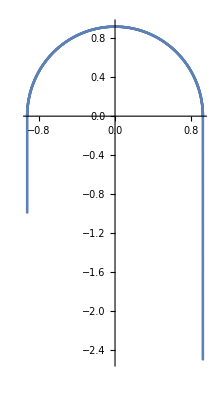

```mathematica
ListPlot[CoilCenter[[CentralLine,All,2;;3]],AspectRatio->Automatic]
```

```mathematica
ArcTan[-CoilCenter[[CentralLine,OutletStart,2]],CoilCenter[[CentralLine,OutletStart,3]]]/Pi*180.
```

7.01668×10^-15

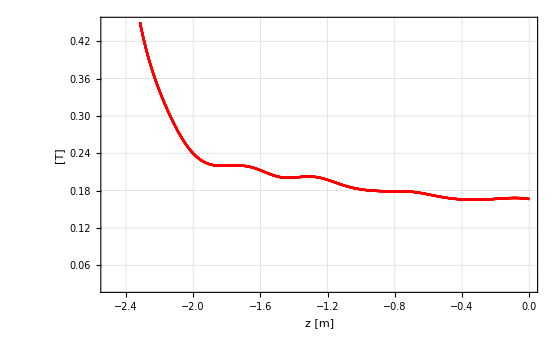

```mathematica
Inlet=ListLinePlot[Table[
Transpose[{CoilCenter[[ii,DataStart;;RxBStart-1,3]],CoilCenter[[ii,DataStart;;RxBStart-1,7]]}],
{ii,1,horilines*vertilines}],
ImageSize->560,PlotStyle->Red,PlotRange->Ranges,Frame->True,PlotRangePadding->{None,None},ImagePadding->{{60, 1}, {50,40}},FrameLabel->{{"[T]",None},{"z [m]","Inlet Bz"}},FrameStyle->15,GridLines->Automatic]
```

```mathematica
(*ListLinePlot[Table[
Transpose[{CoilCenter[[ii,DataStart;;RxBStart-1,3]],CoilCenter[[ii,DataStart;;RxBStart-1,7]]}],
{ii,{6,7,8}}],
ImageSize->1200,PlotRange->Ranges,Frame->True,PlotRangePadding->{None,None},ImagePadding->{{60, 1}, {50,40}},FrameLabel->{{"[T]",None},{"z [m]","Inlet Bz"}},FrameStyle->15,GridLines->Automatic]*)
```

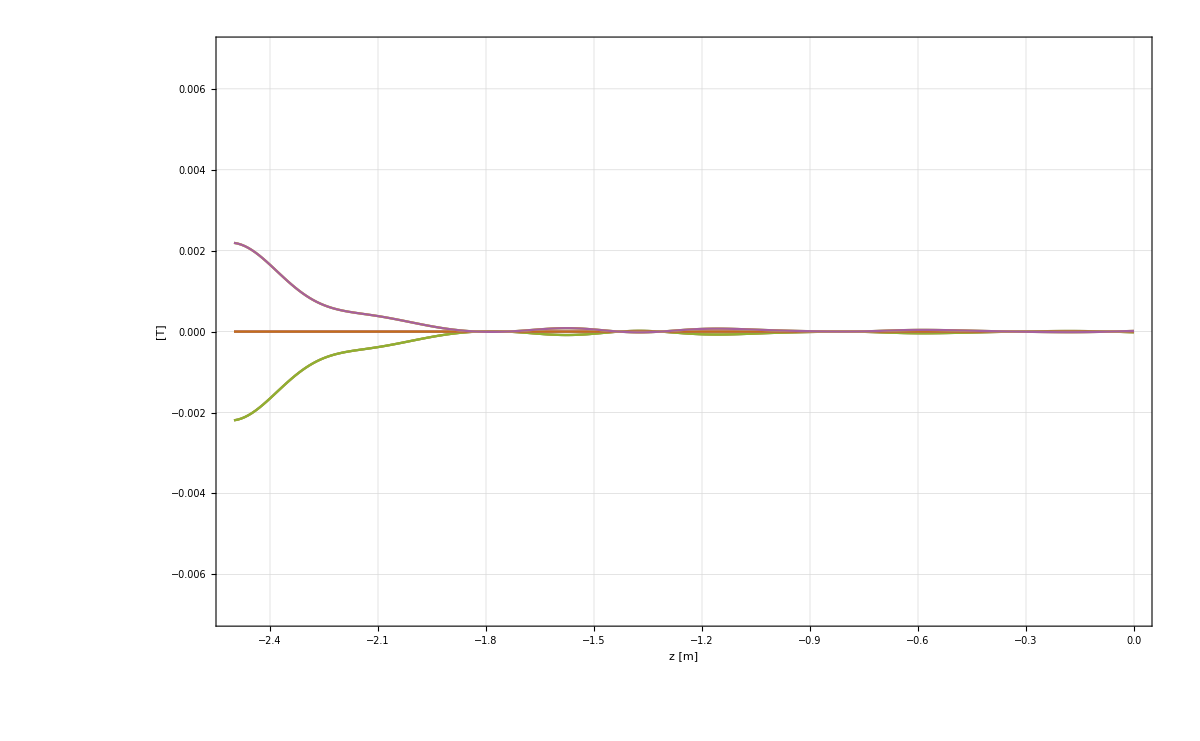

```mathematica
ListLinePlot[Table[
Transpose[{CoilCenter[[ii,DataStart;;RxBStart-1,3]],CoilCenter[[ii,DataStart;;RxBStart-1,5]]}],
{ii,1,horilines*vertilines}],
ImageSize->1200,PlotRange->{-0.007,0.007},Frame->True,PlotRangePadding->{None,None},ImagePadding->{{60, 1}, {50,40}},FrameLabel->{{"[T]",None},{"z [m]","Inlet Bx"}},FrameStyle->15,GridLines->Automatic]
```

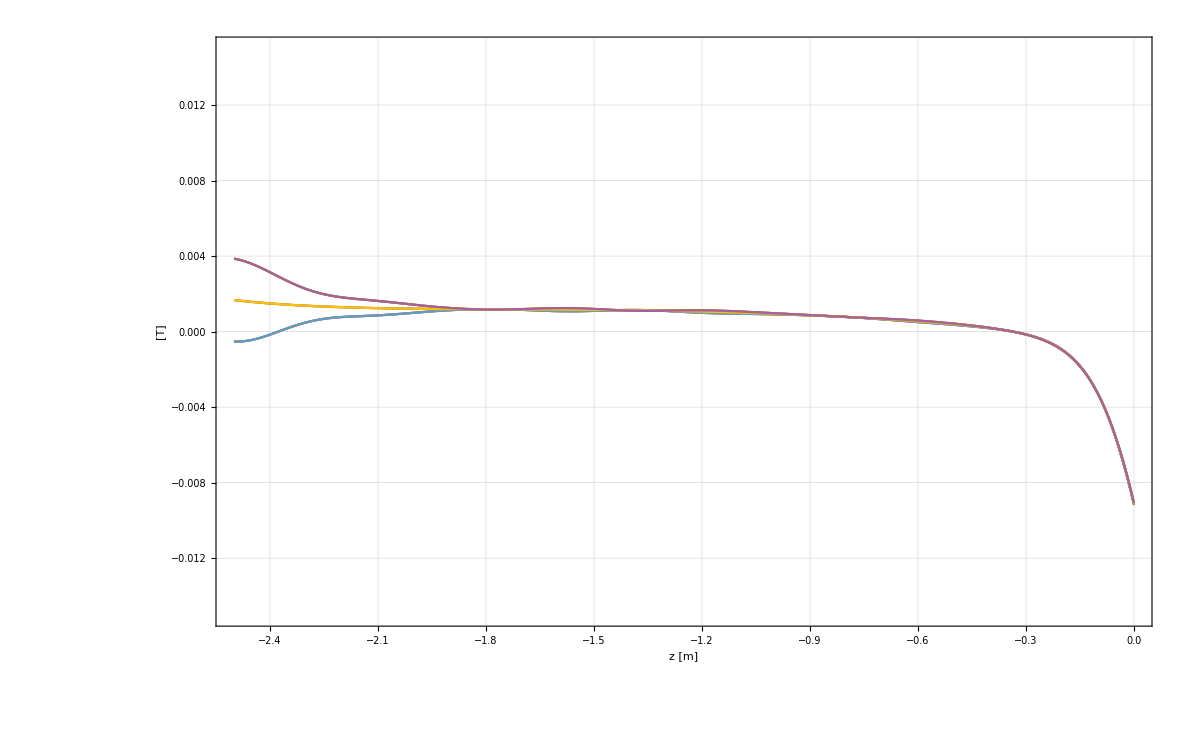

```mathematica
ListLinePlot[Table[
Transpose[{CoilCenter[[ii,DataStart;;RxBStart-1,3]],CoilCenter[[ii,DataStart;;RxBStart-1,6]]}],
{ii,1,horilines*vertilines}],
ImageSize->1200,PlotRange->{-0.015,0.015},Frame->True,PlotRangePadding->{None,None},ImagePadding->{{60, 1}, {50,40}},FrameLabel->{{"[T]",None},{"z [m]","Inlet By"}},FrameStyle->15,GridLines->Automatic]
```

```mathematica
RxBLength=OutletStart-RxBStart
```

1000

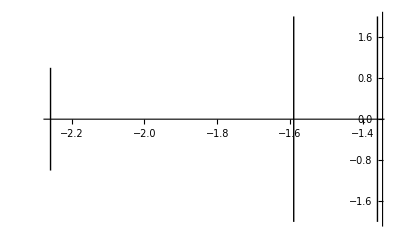

```mathematica
HelmHoltzPlot=ListLinePlot[{{{A1,-2},{A1,2}},{{B2,-2},{B2,2}},{{FirstNoMoSCoilZ,-1},{FirstNoMoSCoilZ,1}}},PlotStyle->Directive[Thick,Black](*,Epilog->Inset[Style[Text["Pumpport"],20],Scaled[{0.75,0.6}]]*),PlotRange->All]
```

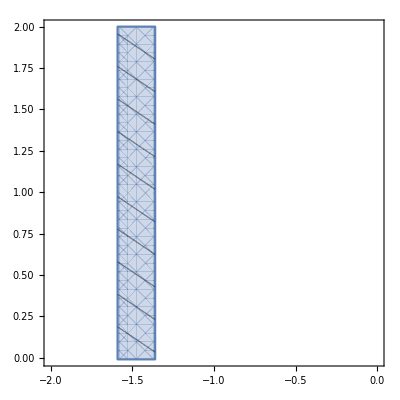

```mathematica
RegionHelm=RegionPlot[B2<x<A1,{x,-2,0},{y,-0.01,2},Mesh->10,MeshFunctions->{#2+1/1.5*#1&}]
```

### we need tangential B field actually, RXB + OUTLET

```mathematica
RxBAngle=Table[
If[CoilCenter[[1,ii,2]]>0,
ArcTan[CoilCenter[[1,ii,3]]/CoilCenter[[1,ii,2]]],
(ArcTan[-CoilCenter[[1,ii,2]]/CoilCenter[[1,ii,3]]]+Pi/2)
],{ii,RxBStart,OutletStart-1}];
```

```mathematica
TangVectorRxB=Table[{-Sin[RxBAngle[[ii-RxBStart+1]]],Cos[RxBAngle[[ii-RxBStart+1]]]},{ii,RxBStart,OutletStart-1}];
```

```mathematica
RxBTanB=Table[
Table[{CoilCenter[[j,ii,6]],CoilCenter[[j,ii,7]]}.TangVectorRxB[[ii-RxBStart+1]],
{ii,RxBStart,OutletStart-1}],
{j,1,horilines*vertilines}];
```

```mathematica
Mean[RxBTanB[[5]]]
```

0.15127

```mathematica
RxB=ListLinePlot[Table[
Table[{RxBAngle[[ii-RxBStart+1]]/Pi*180,RxBTanB[[j,ii-RxBStart+1]]},{ii,RxBStart,OutletStart-1}],
{j,1,horilines*vertilines}],
PlotStyle->Orange,ImageSize->500,PlotRange->Ranges,Frame->True,PlotRangePadding->{None,None},ImagePadding->{{0, 1},{50,40}},FrameLabel->{{None,None},{"θ [°]","RxB Bt"}},FrameStyle->15,GridLines->Automatic];
```

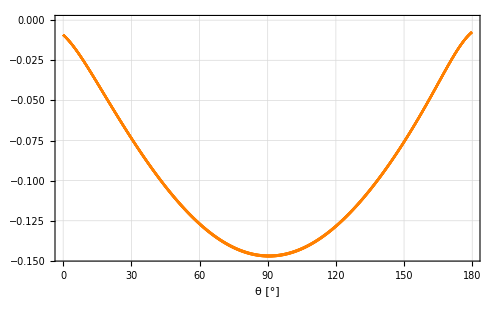

```mathematica
RxBBy=ListLinePlot[Table[
Table[{RxBAngle[[ii-RxBStart+1]]/Pi*180,CoilCenter[[j,ii,6]]},{ii,RxBStart,OutletStart-1}],
{j,1,horilines*vertilines}],
PlotStyle->Orange,ImageSize->500,PlotRange->Automatic,Frame->True,PlotRangePadding->{None,None},ImagePadding->{{0, 1},{50,40}},FrameLabel->{{None,None},{"θ [°]","RxB By"}},FrameStyle->15,GridLines->Automatic]
```

```mathematica
OutletXAxis=Table[
(
Norm[CoilCenter[[line,OutletStart,2;;3]]-#]
)&/@CoilCenter[[line,OutletStart;;-1,2;;3]],
{line,1,horilines*vertilines}];
```

```mathematica
OutletProjectedB=Table[
(#.{-Sin[Pi-alpha],-Cos[Pi-alpha]})&/@CoilCenter[[line,OutletStart;;-1,6;;7]],
{line,1,horilines*vertilines}];
```

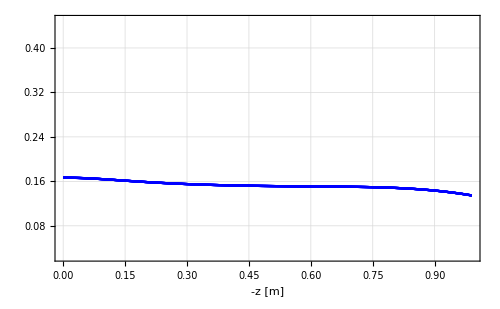

```mathematica
Outlet=ListLinePlot[Table[
Transpose[{OutletXAxis[[j]],OutletProjectedB[[j]]}],
{j,1,horilines*vertilines}],
PlotStyle->Blue,ImageSize->500,PlotRange->Ranges,Frame->True,PlotRangePadding->{None,None},ImagePadding->{{0, 1},{50,40}},FrameLabel->{{None,None},{"-z [m]","Outlet -Bz"}},FrameStyle->15,GridLines->Automatic]
```

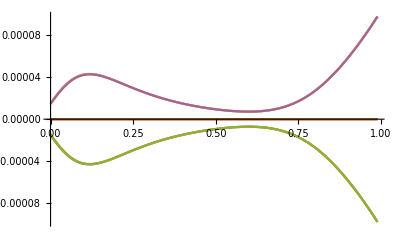

```mathematica
ListLinePlot[
Table[Transpose[{
-CoilCenter[[line,OutletStart;;-1,3]],
CoilCenter[[line,OutletStart;;-1,5]]
}],
{line,1,horilines*vertilines}]
]
```

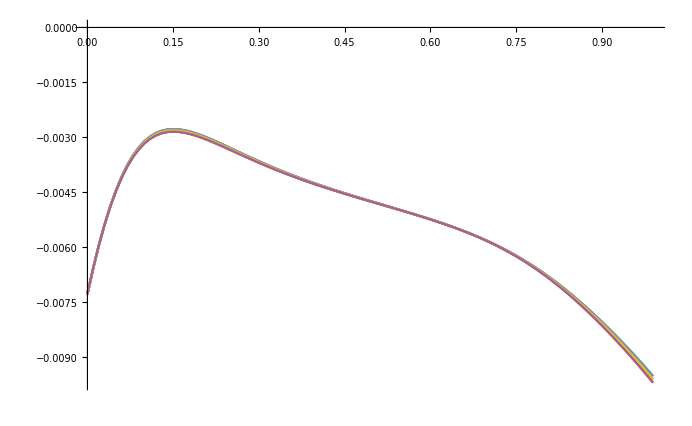

```mathematica
ListLinePlot[
Table[Transpose[{
-CoilCenter[[line,OutletStart;;-1,3]],
CoilCenter[[line,OutletStart;;-1,6]]
}],
{line,1,horilines*vertilines}]
]
```

### Bfield at Pumpport and resulting quadratic cross section

```mathematica
Starta=0.06;StartB=1.5;
```

```mathematica
ConnectorInnerR=CoilData[[1+39+8+8+2+2+1,8]]
```

0.2

```mathematica
If[ConnectorInnerR*2<HelmDiagonal,"ERROR: Beam doesnt fit in coil","Beam fits in coils"]
```

If[0.4<HelmDiagonal,ERROR: Beam doesnt fit in coil,Beam fits in coils]

```mathematica
BeamDiagonal[PERCB_,PERCa_,Blocal_]:=Module[
{localArea=PERCa*PERCa*PERCB/Blocal},
Sqrt[2]*Sqrt[localArea]
]
```

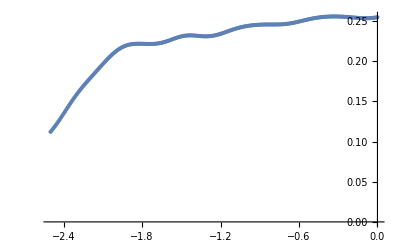

```mathematica
BeamDiagPlot=ListPlot[{#[[3]],BeamDiagonal[1.5,0.06,#[[7]]]}&/@CoilCenter[[5,1;;RxBStart-1]]]
```

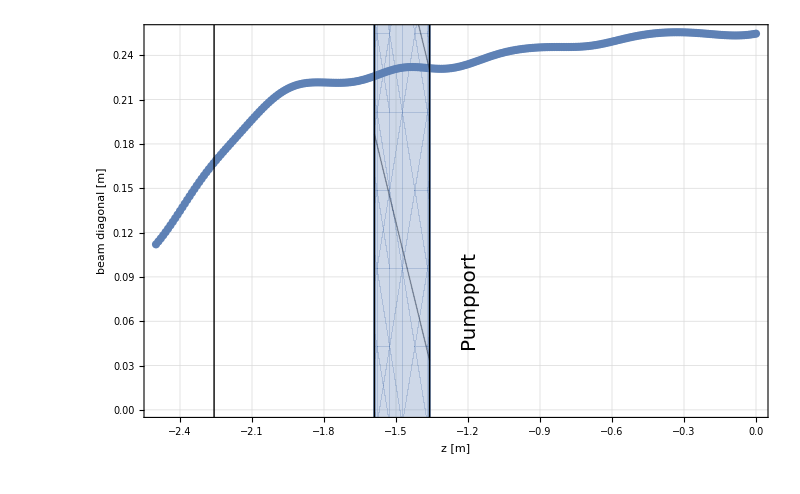

```mathematica
Show[BeamDiagPlot,RegionHelm,HelmHoltzPlot,Epilog->Inset[Rotate[Style[Text["Pumpport"],20],Pi/2],Scaled[{0.52,0.3}]],GridLines->Automatic,Frame->True,FrameLabel->{{"beam diagonal [m]",None},{"z [m]","beam diagonal at NoMoS start"}},FrameStyle->20,ImageSize->800]
```

### Plot

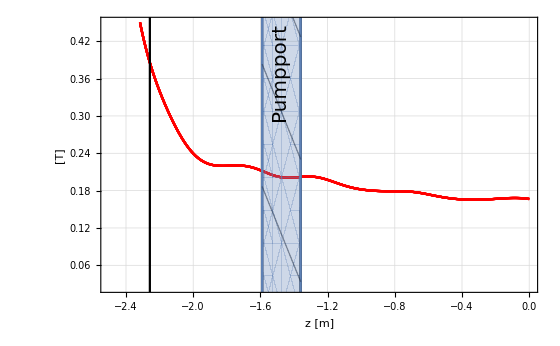
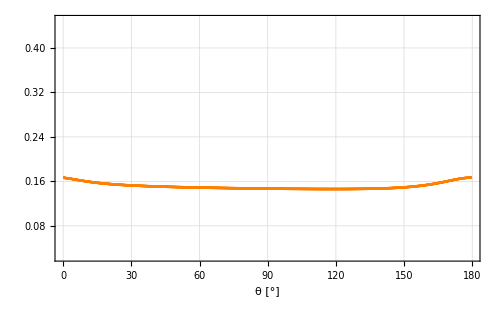
-Graphics--Graphics--Graphics-

```mathematica
CenterPlot=Row[{Show[Inlet,HelmHoltzPlot,RegionHelm,Epilog->Inset[Rotate[Style[Text["Pumpport"],20],Pi/2],Scaled[{(2.5+(B2+A1)/2)/2.5,0.8}]]],RxB,Outlet},ImageSize->{1*^6}]
```

```mathematica
(*Export["/home/dmoser/MagSimResults"<>SubFolder<>"coilcenter_plot.png",CenterPlot,ImageResolution->400]*)
```

```mathematica
(*ListLinePlot[CoilCenter[[All,All,2;;3]],AspectRatio->Automatic]*)
```

```mathematica
ArcSin[Sqrt[0.172/0.38]]/Pi*180
```

42.2819

## COMSOL Shielded PERC import

```mathematica
PercShieldComsolInlet=Import["/home/dmoser/InletData.txt","Table"];
PercShieldComsolRxB=Import["/home/dmoser/RxBData.txt","Table"];
PercShieldComsolOutlet=Import["/home/dmoser/OutletData.txt","Table"];
```

```mathematica
distancePERCOriginNOMOSOrigin=-3.78408;
```

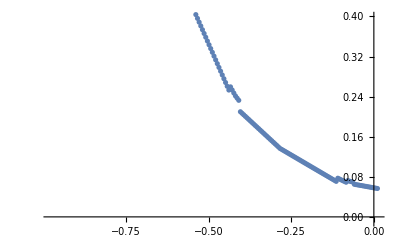

```mathematica
SHInlet=ListPlot[Transpose[{PercShieldComsolInlet[[All,3]]/1000+distancePERCOriginNOMOSOrigin,PercShieldComsolInlet[[All,6]]}],PlotRange->{-0.01,0.4}];
```

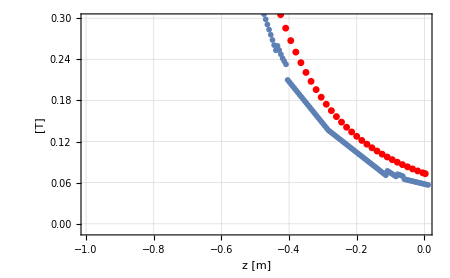

```mathematica
Show[Inlet,SHInlet]
```

```mathematica
PercShieldComsolRxB[[1]]
```

{0.,0.000136335,0.000606036,0.0579991}

```mathematica
BtangSH=Transpose[{PercShieldComsolRxB[[All,1]]/Pi*180,Map[{#[[3]],#[[4]]}.{Sin[#[[1]]],Cos[#[[1]]]}&,PercShieldComsolRxB]}];
```

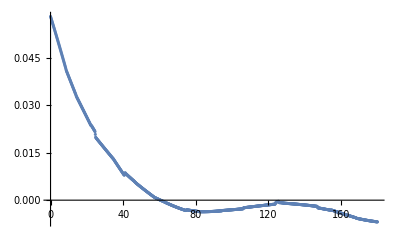

```mathematica
SHRxB=ListPlot[BtangSH]
```

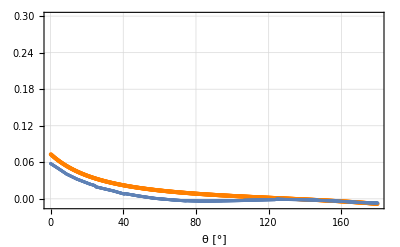

```mathematica
Show[RxB,SHRxB]
```

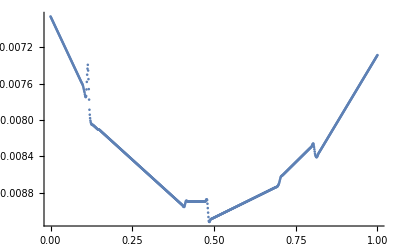

```mathematica
SHOutlet=ListPlot[Transpose[{-(PercShieldComsolOutlet[[All,1]]),-PercShieldComsolOutlet[[All,4]]}]];
```

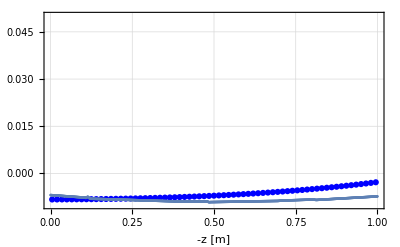

```mathematica
Show[Outlet,SHOutlet,PlotRange->{-0.01,0.05}]
```

```mathematica
Needs["PlotLegends`"]
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

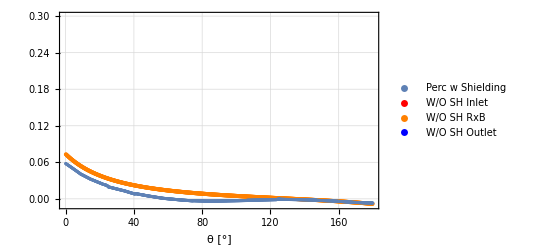
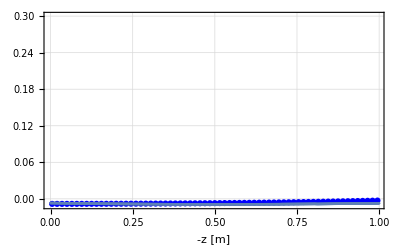
-Graphics--Graphics--Graphics-

```mathematica
WithSH=Row[{
Show[Inlet,SHInlet],
Legended[Show[RxB,SHRxB],Placed[PointLegend[{ColorData[97,"ColorList"][[1]],Red,Orange,Blue},{"Perc w Shielding","W/O SH Inlet","W/O SH RxB","W/O SH Outlet"},LegendMarkerSize->20,LabelStyle->20],{0.5,0.5}]],
Show[Outlet,SHOutlet]
},ImageSize->{1*^6}]
```

```mathematica
Export["/home/dmoser/Dropbox/PhD/EingriffPERCComparison.png",WithSH,ImageResolution->500];
```

```mathematica
(*Export["BzBt_central_PercOnly.png",Row[{Inlet,RxB,Outlet}],ImageResolution->600];*)
```

### Bx

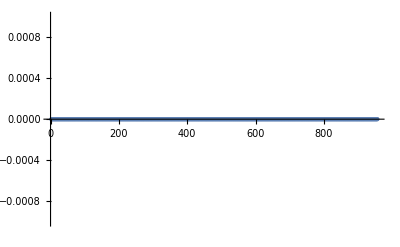

```mathematica
ListPlot[CoilCenter[[All,5]],PlotRange->{-0.001,0.001}]
```

### By

```mathematica
InletY=ListPlot[Transpose[{CoilCenter[[DataStart;;RxBStart,3]],CoilCenter[[DataStart;;RxBStart,6]]}],ImageSize->450,PlotStyle->Red,PlotRange->{-0.05,0.4},Frame->True,PlotRangePadding->{None,None},ImagePadding->{{50, 1}, {50,40}},FrameLabel->{{"[T]",None},{"z [m]","Inlet By"}},FrameStyle->15,GridLines->Automatic];
RxBY=ListPlot[Table[{RxBAngle[[ii-RxBStart+1]]/Pi*180,CoilCenter[[ii,6]]},{ii,RxBStart,OutletStart-1}],PlotStyle->Orange,ImageSize->400,PlotRange->{-0.05,0.4},Frame->True,PlotRangePadding->{None,None},ImagePadding->{{0, 1},{50,40}},FrameLabel->{{None,None},{"θ [°]","RxB By"}},FrameStyle->15,GridLines->Automatic];
OutletY=ListPlot[Transpose[{-CoilCenter[[OutletStart;;-1,3]],CoilCenter[[OutletStart;;-1,6]]}],PlotStyle->Blue,ImageSize->400,PlotRange->{-0.05,0.4},Frame->True,PlotRangePadding->{None,None},ImagePadding->{{0, 1},{50,40}},FrameLabel->{{None,None},{"-z [m]","Outlet By"}},FrameStyle->15,GridLines->Automatic];
```

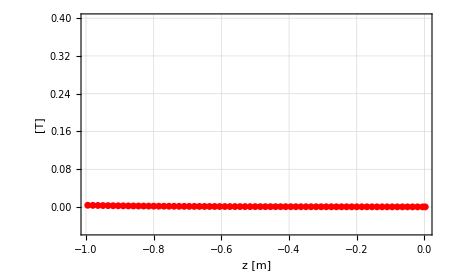
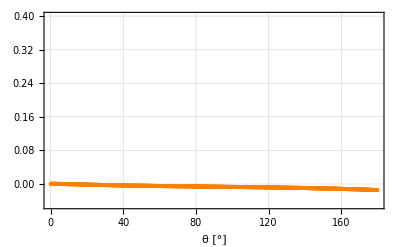
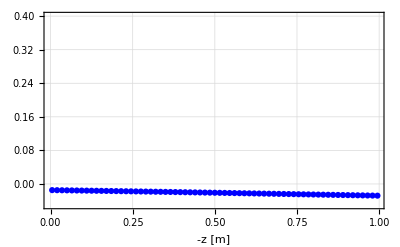

```mathematica
Row[{InletY,RxBY,OutletY}]
```

```mathematica
(*Export["By_central_PercOnly.png",Row[{InletY,RxBY,OutletY}],ImageResolution->600];*)
```

```mathematica
CoilCenter[[OutletStart]]
```

{0,-0.901622,-0.00488326,0.0168534,0,-0.0146867,0.00826666}

## Geometric line with/without analytical drift (assume, both are calculated in folder)

```mathematica
OS="Linux";SubFolder="/NoMoS_finalIter_allCalc/";
```

### import

```mathematica
Which[OS=="Linux",
SetDirectory["/home/dmoser/MagSimResults"<>SubFolder];,
OS=="Mac",
"meh"
]
```

```mathematica
InfoFileDOn=Import["geo_DOn_info.txt","Table"]
InfoFileDOff=Import["geo_DOff_info.txt","Table"]
```

{{R_1,horilines,vertilines,apertsizeX,apertsizeY},{0.901622,3,5,0.01,0.1}}

{{R_1,horilines,vertilines,apertsizeX,apertsizeY},{0.901622,3,5,0.01,0.1}}

```mathematica
R1=InfoFileDOn[[2,1]]
```

0.901622

```mathematica
horilines=InfoFileDOn[[2,2]];vertilines=InfoFileDOn[[2,3]];ApertX=InfoFileDOn[[2,4]];ApertY=InfoFileDOn[[2,5]];
```

```mathematica
XStep=ApertX/(horilines-1);YStep=ApertY/(vertilines-1);
```

```mathematica
XSteps=Table["X"<>ToString[If[-ApertX/2+XStep*x==0.,0,-ApertX/2+XStep*x]],{x,0,horilines-1}]
YSteps=Table["Y"<>ToString[If[-ApertY/2+YStep*x==0.,0,-ApertY/2+YStep*x]],{x,0,vertilines-1}]
```

{X-0.005,X0,X0.005}

{Y-0.05,Y-0.025,Y0,Y0.025,Y0.05}

```mathematica
GeoNames=Flatten[Table[Table[
XSteps[[x]]<>"_"<>YSteps[[y]],
{y,1,vertilines}],
{x,1,horilines}]]
```

{X-0.005_Y-0.05,X-0.005_Y-0.025,X-0.005_Y0,X-0.005_Y0.025,X-0.005_Y0.05,X0_Y-0.05,X0_Y-0.025,X0_Y0,X0_Y0.025,X0_Y0.05,X0.005_Y-0.05,X0.005_Y-0.025,X0.005_Y0,X0.005_Y0.025,X0.005_Y0.05}

```mathematica
GeoFileNamesDOn=Flatten[Table[Table[
"geo_DOn_"<>XSteps[[x]]<>"_"<>YSteps[[y]]<>".txt",
{y,1,vertilines}],
{x,1,horilines}]]
```

{geo_DOn_X-0.005_Y-0.05.txt,geo_DOn_X-0.005_Y-0.025.txt,geo_DOn_X-0.005_Y0.txt,geo_DOn_X-0.005_Y0.025.txt,geo_DOn_X-0.005_Y0.05.txt,geo_DOn_X0_Y-0.05.txt,geo_DOn_X0_Y-0.025.txt,geo_DOn_X0_Y0.txt,geo_DOn_X0_Y0.025.txt,geo_DOn_X0_Y0.05.txt,geo_DOn_X0.005_Y-0.05.txt,geo_DOn_X0.005_Y-0.025.txt,geo_DOn_X0.005_Y0.txt,geo_DOn_X0.005_Y0.025.txt,geo_DOn_X0.005_Y0.05.txt}

```mathematica
GeoFileNamesDOff=Flatten[Table[Table[
"geo_DOff_"<>XSteps[[x]]<>"_"<>YSteps[[y]]<>".txt",
{y,1,vertilines}],
{x,1,horilines}]]
```

{geo_DOff_X-0.005_Y-0.05.txt,geo_DOff_X-0.005_Y-0.025.txt,geo_DOff_X-0.005_Y0.txt,geo_DOff_X-0.005_Y0.025.txt,geo_DOff_X-0.005_Y0.05.txt,geo_DOff_X0_Y-0.05.txt,geo_DOff_X0_Y-0.025.txt,geo_DOff_X0_Y0.txt,geo_DOff_X0_Y0.025.txt,geo_DOff_X0_Y0.05.txt,geo_DOff_X0.005_Y-0.05.txt,geo_DOff_X0.005_Y-0.025.txt,geo_DOff_X0.005_Y0.txt,geo_DOff_X0.005_Y0.025.txt,geo_DOff_X0.005_Y0.05.txt}

### format = x,y,z,b,bx,by,bz,bt,br

```mathematica
GeoFilesOn=Table[Cases[Import[GeoFileNamesDOn[[i]],"Table"],{_,_,_,_,_,_,_,_,_}],{i,1,horilines*vertilines}];
GeoFilesOff=Table[Cases[Import[GeoFileNamesDOff[[i]],"Table"],{_,_,_,_,_,_,_,_,_}],{i,1,horilines*vertilines}];
```

### length of datasets and angles should be the same for each data set

```mathematica
GeoEnd=GeoFilesOn[[1]]//Length
```

1000

```mathematica
GeoAngle=Table[
If[GeoFilesOn[[1,ii,2]]>0,
ArcTan[GeoFilesOn[[1,ii,3]]/GeoFilesOn[[1,ii,2]]],
ArcTan[-GeoFilesOn[[1,ii,2]]/GeoFilesOn[[1,ii,3]]]+Pi/2
],{ii,1,GeoEnd}];
```

```mathematica
Table[GeoFilesOn[[i]]//Length,{i,1,15}]
```

{1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000}

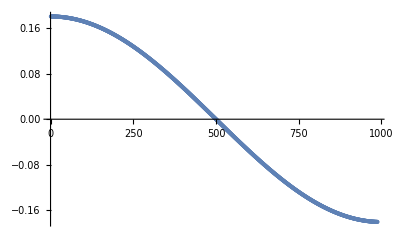

```mathematica
ListPlot[Table[ArcSin[(Norm[GeoFilesOn[[15,i+1,3]]]-Norm[GeoFilesOn[[15,i,3]]])/Norm[GeoFilesOn[[15,i+1,2;;3]]]]/Pi*180,{i,1,988}]]
```

```mathematica
GeoFilesOn[[15,-1]]
```

{-0.0790854,-0.951622,1.1654×10^-16,0.153657,0.000176477,-0.00852411,-0.15342,0.15342,0.00852411}

### tangential field

```mathematica
GeoOnPlot=ListLinePlot[Table[Transpose[{GeoAngle/Pi*180.,GeoFilesOn[[ii,All,8]]}],{ii,1,horilines*vertilines}],ImageSize->900,(*PlotRange->{0,0.4},*)Frame->True,FrameLabel->{{None,None},{"θ [°]","RxB Bt"}},FrameStyle->15,GridLines->Automatic(*,PlotLegends->GeoNames*),PlotStyle->Blue];
```

```mathematica
GeoOffPlot=ListLinePlot[Table[Transpose[{GeoAngle/Pi*180.,GeoFilesOff[[ii,All,8]]}],{ii,1,horilines*vertilines}],ImageSize->900,(*PlotRange->{0,0.4},*)Frame->True,FrameLabel->{{None,None},{"θ [°]","RxB Bt"}},FrameStyle->15,GridLines->Automatic(*,PlotLegends->GeoNames*),PlotStyle->Red];
```

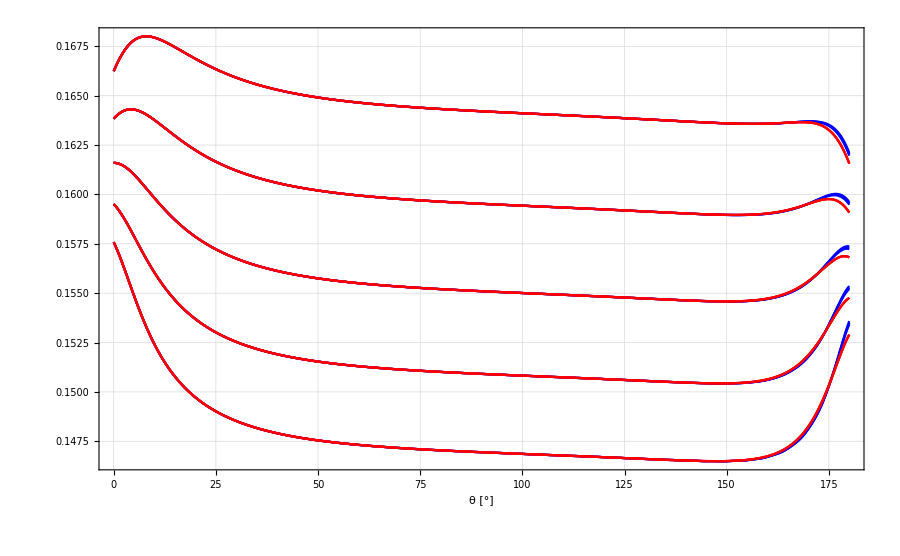

```mathematica
Show[GeoOnPlot,GeoOffPlot]
```

### now the relevant relative values (B-Bt)/B deviation from absolute field

```mathematica
GeoRelBtOnPlot=ListLinePlot[Table[Transpose[{GeoAngle,(GeoFilesOn[[ii,All,4]]-GeoFilesOn[[ii,All,8]])/GeoFilesOn[[ii,All,4]]}],{ii,1,horilines*vertilines}],ImageSize->800,Frame->True,FrameLabel->{{"ΔB/B",None},{"θ [rad]","RxB: (B - Bt)/B"}},FrameStyle->15,GridLines->Automatic,PlotRange->All(*,PlotLegends->GeoNames*),PlotStyle->Opacity[0.4,Blue]];
```

```mathematica
GeoRelBtOffPlot=ListLinePlot[Table[Transpose[{GeoAngle,(GeoFilesOff[[ii,All,4]]-GeoFilesOff[[ii,All,8]])/GeoFilesOff[[ii,All,4]]}],{ii,1,horilines*vertilines}],ImageSize->800,Frame->True,FrameLabel->{{"ΔB/B",None},{"θ [rad]","RxB: (B - Bt)/B"}},FrameStyle->15,GridLines->Automatic,PlotRange->All(*,PlotLegends->GeoNames*),PlotStyle->Opacity[0.4,Red]];
```

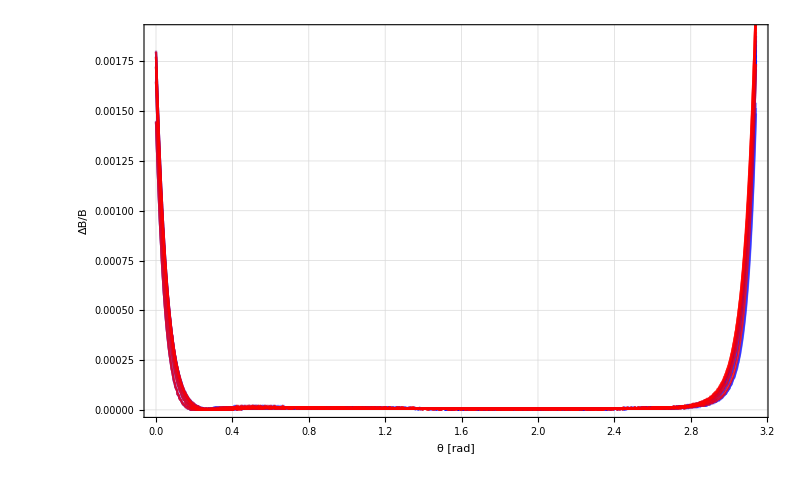

```mathematica
Show[GeoRelBtOnPlot,GeoRelBtOffPlot]
```

### Bx relative

```mathematica
BxRelOnPlot=ListLinePlot[Table[Transpose[{GeoAngle,(GeoFilesOn[[ii,All,5]])/GeoFilesOn[[ii,All,4]]}],{ii,1,horilines*vertilines}],ImageSize->800,Frame->True,FrameLabel->{{"Bx/B",None},{"θ [rad]","RxB: Bx/B"}},FrameStyle->15,GridLines->Automatic,PlotRange->All(*,PlotLegends->GeoNames*),PlotStyle->Blue];
BxRelOffPlot=ListLinePlot[Table[Transpose[{GeoAngle,(GeoFilesOff[[ii,All,5]])/GeoFilesOff[[ii,All,4]]}],{ii,1,horilines*vertilines}],ImageSize->800,Frame->True,FrameLabel->{{"Bx/B",None},{"θ [rad]","RxB: Bx/B"}},FrameStyle->15,GridLines->Automatic,PlotRange->All(*,PlotLegends->GeoNames*),PlotStyle->Red];
```

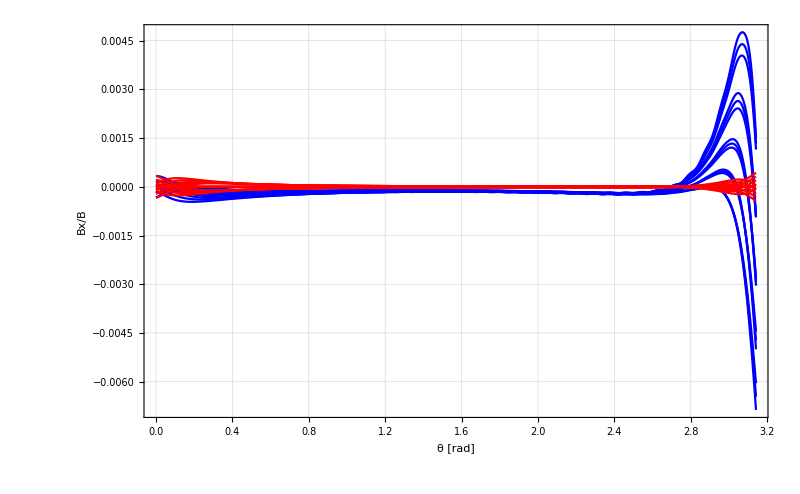

```mathematica
Show[BxRelOnPlot,BxRelOffPlot]
```

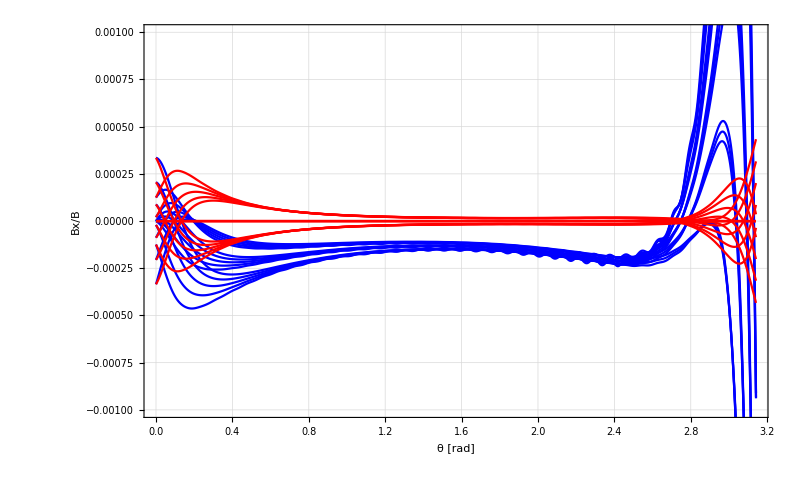

```mathematica
Show[BxRelOnPlot,BxRelOffPlot,PlotRange->{-0.001,0.001}]
```

### Brad/B

```mathematica
BradRelOnPlot=ListLinePlot[Table[Transpose[{GeoAngle,(GeoFilesOn[[ii,All,9]])/GeoFilesOn[[ii,All,4]]}],{ii,1,horilines*vertilines}],ImageSize->800,Frame->True,FrameLabel->{{"Brad/B",None},{"θ [rad]","RxB: Brad/B"}},FrameStyle->15,GridLines->Automatic,PlotRange->All(*,PlotLegends->GeoNames*),PlotStyle->Opacity[0.4,Blue]];
BradRelOffPlot=ListLinePlot[Table[Transpose[{GeoAngle,(GeoFilesOff[[ii,All,9]])/GeoFilesOff[[ii,All,4]]}],{ii,1,horilines*vertilines}],ImageSize->800,Frame->True,FrameLabel->{{"Brad/B",None},{"θ [rad]","RxB: Brad/B"}},FrameStyle->15,GridLines->Automatic,PlotRange->All(*,PlotLegends->GeoNames*),PlotStyle->Opacity[0.4,Red]];
```

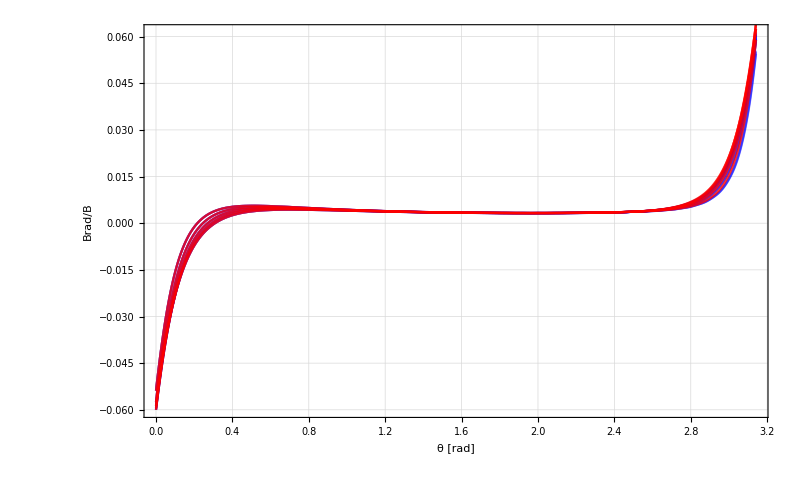

```mathematica
Show[BradRelOnPlot,BradRelOffPlot]
```

### End position of each line → should be exact, because geometric lines + clear drift

```mathematica
EndPosOn=ListPlot[Table[{GeoFilesOn[[ii,-1,2]]+R1,GeoFilesOn[[ii,-1,1]]},{ii,1,horilines*vertilines}],PlotStyle->Blue,GridLines->Automatic,AspectRatio->Automatic,Frame->True,ImageSize->700];
EndPosOff=ListPlot[Table[{GeoFilesOff[[ii,-1,2]]+R1,GeoFilesOff[[ii,-1,1]]},{ii,1,horilines*vertilines}],PlotStyle->Red,GridLines->Automatic,AspectRatio->Automatic,Frame->True,ImageSize->700];
```

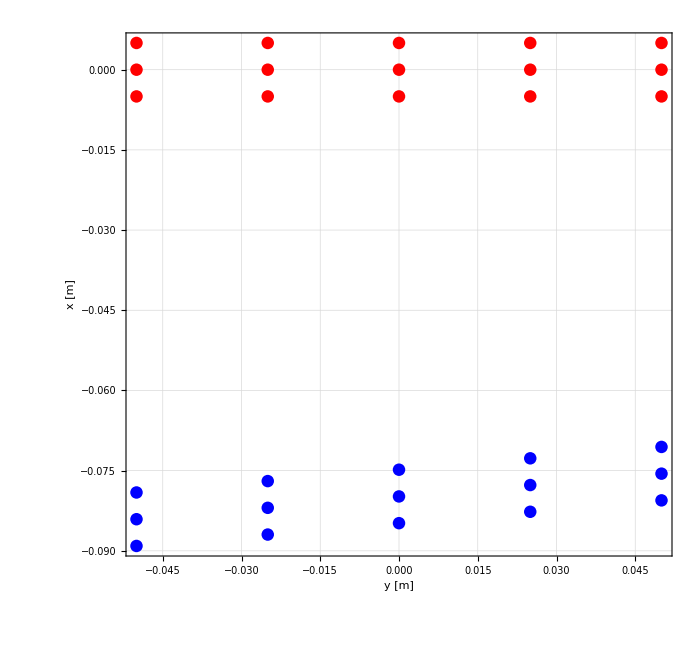

```mathematica
Show[EndPosOn,EndPosOff,PlotRange->All,FrameLabel->{{"x [m]",None},{"y [m]","EndPosition XY"}},FrameStyle->20]
```

## B-field lines with/without analytical drift added

```mathematica
OS="Linux";SubFolder="/NoMoS_2-10-17_opt_Outlet_lvb_InletAdapt/";
```

### info files, should also contain startP und endP?!

```mathematica
Which[OS=="Linux",
SetDirectory["/home/dmoser/MagSimResults"<>SubFolder];,
OS=="Mac",
"meh"
]
```

```mathematica
InfoFileNames=FileNames["bline*_info.txt"]
```

{bline_D1stOn_info.txt,bline_D2ndOn_info.txt,bline_Doff_info.txt}

```mathematica
If[(FileNames["bline*_info.txt"]//Length) > 1, Abort[]]
```

$Aborted

```mathematica
InfoFileDOnBxDOn=Import[InfoFileNames[[2]],"Table"]
```

{{R_1,horilines,vertilines,apertsizeX,apertsizeY,driftOn},{0.921622,2,3,0.01,0.1,2}}

```mathematica
R1=InfoFileDOnBxDOn[[2,1]]
```

0.921622

### filename creation. we assume that aperture data is same for all the different datasets

```mathematica
horilines=InfoFileDOnBxDOn[[2,2]];vertilines=InfoFileDOnBxDOn[[2,3]];ApertX=InfoFileDOnBxDOn[[2,4]];ApertY=InfoFileDOnBxDOn[[2,5]];DriftOn=If[InfoFileDOnBxDOn[[2,6]]==1,"On","Off"]
```

Off

```mathematica
XStep=ApertX/(horilines-1);YStep=ApertY/(vertilines-1);
```

```mathematica
XSteps=Table["X"<>ToString[If[-ApertX/2+XStep*x==0.,0,-ApertX/2+XStep*x]],{x,0,horilines-1}]
YSteps=Table["Y"<>ToString[If[-ApertY/2+YStep*x==0.,0,-ApertY/2+YStep*x]],{x,0,vertilines-1}]
```

{X-0.005,X0.005}

{Y-0.05,Y0,Y0.05}

```mathematica
BLineNames=Flatten[Table[Table[
XSteps[[x]]<>"_"<>YSteps[[y]],
{y,1,vertilines}],
{x,1,horilines}]]
```

{X-0.005_Y-0.05,X-0.005_Y0,X-0.005_Y0.05,X0.005_Y-0.05,X0.005_Y0,X0.005_Y0.05}

```mathematica
BLineFileNamesDOn=Flatten[Table[Table[
"bline_D1stOn_"<>XSteps[[x]]<>"_"<>YSteps[[y]]<>".txt",
{y,1,vertilines}],
{x,1,horilines}]]
```

{bline_D1stOn_X-0.005_Y-0.05.txt,bline_D1stOn_X-0.005_Y0.txt,bline_D1stOn_X-0.005_Y0.05.txt,bline_D1stOn_X0.005_Y-0.05.txt,bline_D1stOn_X0.005_Y0.txt,bline_D1stOn_X0.005_Y0.05.txt}

```mathematica
BLineFileNamesDOff=Flatten[Table[Table[
"bline_Doff_"<>XSteps[[x]]<>"_"<>YSteps[[y]]<>".txt",
{y,1,vertilines}],
{x,1,horilines}]]
```

{bline_Doff_X-0.005_Y-0.05.txt,bline_Doff_X-0.005_Y0.txt,bline_Doff_X-0.005_Y0.05.txt,bline_Doff_X0.005_Y-0.05.txt,bline_Doff_X0.005_Y0.txt,bline_Doff_X0.005_Y0.05.txt}

```mathematica
BLineFileNamesD2nd=Flatten[Table[Table[
"bline_D2ndOn_"<>XSteps[[x]]<>"_"<>YSteps[[y]]<>".txt",
{y,1,vertilines}],
{x,1,horilines}]]
```

{bline_D2ndOn_X-0.005_Y-0.05.txt,bline_D2ndOn_X-0.005_Y0.txt,bline_D2ndOn_X-0.005_Y0.05.txt,bline_D2ndOn_X0.005_Y-0.05.txt,bline_D2ndOn_X0.005_Y0.txt,bline_D2ndOn_X0.005_Y0.05.txt}

### import. format = x,y,z,b,bx,by,bz,btang,brad

```mathematica
BLineFilesDOn=Table[Cases[Import[BLineFileNamesDOn[[i]],"Table"],{_,_,_,_,_,_,_,_,_}],{i,1,horilines*vertilines}];
BLineFilesD2nd=Table[Cases[Import[BLineFileNamesD2nd[[i]],"Table"],{_,_,_,_,_,_,_,_,_}],{i,1,horilines*vertilines}];
BLineFilesDOff=Table[Cases[Import[BLineFileNamesDOff[[i]],"Table"],{_,_,_,_,_,_,_,_,_}],{i,1,horilines*vertilines}];
```

### length of datasets and areas

```mathematica
DataRxBStartDOn=Table[First[Position[BLineFilesDOn[[ii]],{_,_,_?(#≥0.&),_,_,_,_,_,_}]][[1]],{ii,1,horilines*vertilines}]
DataRxBStartD2nd=Table[First[Position[BLineFilesD2nd[[ii]],{_,_,_?(#≥0.&),_,_,_,_,_,_}]][[1]],{ii,1,horilines*vertilines}]
DataRxBStartDOff=Table[First[Position[BLineFilesDOff[[ii]],{_,_,_?(#≥0.&),_,_,_,_,_,_}]][[1]],{ii,1,horilines*vertilines}]
```

{270,270,270,270,270,270}

{270,270,270,270,270,270}

{270,270,270,270,270,270}

```mathematica
DataOutletStartDOn=Table[First[Position[BLineFilesDOn[[ii]],{_,_?(#<0&),_?(#<=0.&),_,_,_,_,_,_}]][[1]],{ii,1,horilines*vertilines}]
DataOutletStartD2nd=Table[First[Position[BLineFilesD2nd[[ii]],{_,_?(#<0&),_?(#<=0.&),_,_,_,_,_,_}]][[1]],{ii,1,horilines*vertilines}]
DataOutletStartDOff=Table[First[Position[BLineFilesDOff[[ii]],{_,_?(#<0&),_?(#<=0.&),_,_,_,_,_,_}]][[1]],{ii,1,horilines*vertilines}]
```

{772,802,833,772,802,833}

{773,802,834,773,803,834}

{772,802,833,772,802,833}

```mathematica
DataDetDOn=Table[First[Position[BLineFilesDOn[[ii]],{_,_?(#<0&),_?(#≤-0.3&),_,_,_,_,_,_}]][[1]],{ii,1,horilines*vertilines}]
DataDetD2nd=Table[First[Position[BLineFilesD2nd[[ii]],{_,_?(#<0&),_?(#≤-0.3&),_,_,_,_,_,_}]][[1]],{ii,1,horilines*vertilines}]
DataDetDOff=Table[First[Position[BLineFilesDOff[[ii]],{_,_?(#<0&),_?(#≤-0.3&),_,_,_,_,_,_}]][[1]],{ii,1,horilines*vertilines}]
```

{827,856,888,827,857,888}

{827,857,888,827,857,888}

{827,856,888,827,857,888}

```mathematica
BLineAngleDOn=
Table[
Table[
Which[BLineFilesDOn[[i,ii,2]]>0,
ArcTan[BLineFilesDOn[[i,ii,3]]/BLineFilesDOn[[i,ii,2]]],
BLineFilesDOn[[i,ii,2]]<0&&BLineFilesDOn[[i,ii,3]]>0,
ArcTan[-BLineFilesDOn[[i,ii,2]]/BLineFilesDOn[[i,ii,3]]]+Pi/2,
BLineFilesDOn[[i,ii,2]]<0&&BLineFilesDOn[[i,ii,3]]<0,
ArcTan[BLineFilesDOn[[i,ii,3]]/BLineFilesDOn[[i,ii,2]]]+Pi
],{ii,DataRxBStartDOn[[i]],DataOutletStartDOn[[i]]-1}],
{i,1,horilines*vertilines}];
BLineAngleD2nd=
Table[
Table[
Which[BLineFilesD2nd[[i,ii,2]]>0,
ArcTan[BLineFilesD2nd[[i,ii,3]]/BLineFilesD2nd[[i,ii,2]]],
BLineFilesD2nd[[i,ii,2]]<0&&BLineFilesD2nd[[i,ii,3]]>0,
ArcTan[-BLineFilesD2nd[[i,ii,2]]/BLineFilesD2nd[[i,ii,3]]]+Pi/2,
BLineFilesD2nd[[i,ii,2]]<0&&BLineFilesD2nd[[i,ii,3]]<0,
ArcTan[BLineFilesD2nd[[i,ii,3]]/BLineFilesD2nd[[i,ii,2]]]+Pi
],{ii,DataRxBStartD2nd[[i]],DataOutletStartD2nd[[i]]-1}],
{i,1,horilines*vertilines}];
BLineAngleDOff=
Table[
Table[
Which[BLineFilesDOff[[i,ii,2]]>0,
ArcTan[BLineFilesDOff[[i,ii,3]]/BLineFilesDOff[[i,ii,2]]],
BLineFilesDOff[[i,ii,2]]<0&&BLineFilesDOff[[i,ii,3]]>0,
ArcTan[-BLineFilesDOff[[i,ii,2]]/BLineFilesDOff[[i,ii,3]]]+Pi/2,
BLineFilesDOff[[i,ii,2]]<0&&BLineFilesDOff[[i,ii,3]]<0,
ArcTan[BLineFilesDOff[[i,ii,3]]/BLineFilesDOff[[i,ii,2]]]+Pi
],{ii,DataRxBStartDOff[[i]],DataOutletStartDOff[[i]]-1}],
{i,1,horilines*vertilines}];
```

### 3D Lines

```mathematica
ListPointPlot3D[Table[BLineFilesDOn[[i,All,1;;3]],{i,1,horilines*vertilines}],AspectRatio->Automatic,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

### X Position in RxB

```mathematica
XPlotDOn=ListPlot[Table[Transpose[{BLineAngleDOn[[i]],BLineFilesDOn[[i,DataRxBStartDOn[[i]];;DataOutletStartDOn[[i]]-1,1]]}],{i,1,horilines*vertilines}],ImageSize->700,PlotStyle->Blue];
```

```mathematica
XPlotD2nd=ListPlot[Table[Transpose[{BLineAngleD2nd[[i]],BLineFilesD2nd[[i,DataRxBStartD2nd[[i]];;DataOutletStartD2nd[[i]]-1,1]]}],{i,1,horilines*vertilines}],ImageSize->700,PlotStyle->Red];
XPlotDOff=ListPlot[Table[Transpose[{BLineAngleDOff[[i]],BLineFilesDOff[[i,DataRxBStartDOff[[i]];;DataOutletStartDOff[[i]]-1,1]]}],{i,1,horilines*vertilines}],ImageSize->700,PlotStyle->Green];
```

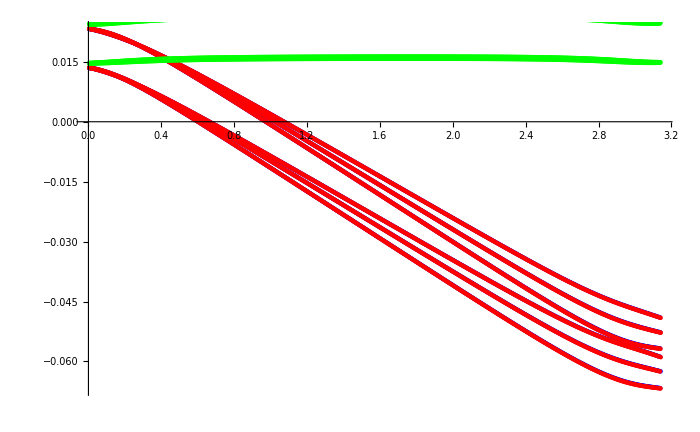

```mathematica
Show[XPlotDOn,XPlotD2nd,XPlotDOff]
```

### X Position dependent on Z for full data

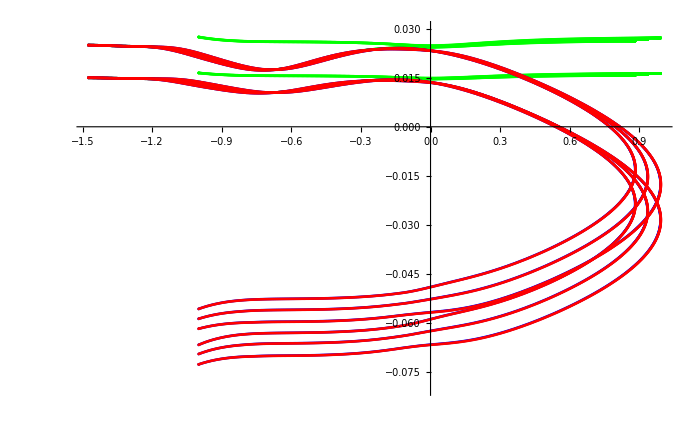

```mathematica
Show[
ListPlot[Table[Transpose[{BLineFilesDOff[[i,All,3]],BLineFilesDOff[[i,All,1]]}],{i,1,horilines*vertilines}],ImageSize->700,PlotStyle->Green,PlotRange->{-0.08,0.03}],
ListPlot[Table[Transpose[{BLineFilesDOn[[i,All,3]],BLineFilesDOn[[i,All,1]]}],{i,1,horilines*vertilines}],ImageSize->700,PlotStyle->Blue,PlotRange->{-0.08,0.03}],
ListPlot[Table[Transpose[{BLineFilesD2nd[[i,All,3]],BLineFilesD2nd[[i,All,1]]}],{i,1,horilines*vertilines}],ImageSize->700,PlotStyle->Red,PlotRange->{-0.08,0.03}]
]
```

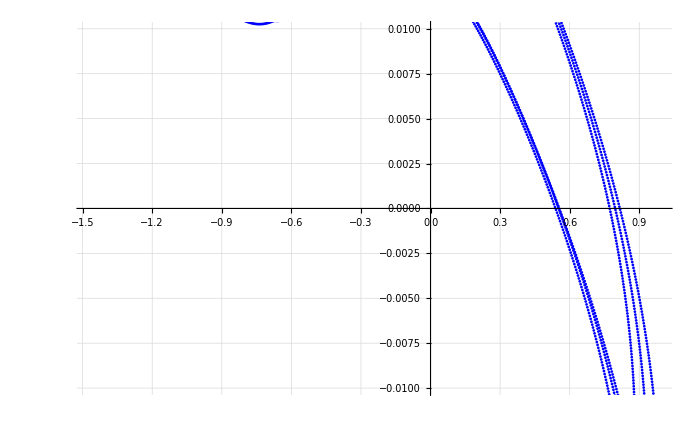

```mathematica
Show[
ListPlot[Table[Transpose[{BLineFilesDOff[[i,All,3]],BLineFilesDOff[[i,All,1]]}],{i,1,horilines*vertilines}],ImageSize->700,PlotStyle->Red,PlotRange->{-0.01,0.01}],
ListPlot[Table[Transpose[{BLineFilesDOn[[i,All,3]],BLineFilesDOn[[i,All,1]]}],{i,1,horilines*vertilines}],ImageSize->700,PlotStyle->Blue,PlotRange->{-0.01,0.01}]
,GridLines->Automatic]
```

### YZ Position

```mathematica
PipeDiag=350/1000;Pipea=PipeDiag/Sqrt[2];
RConst=ListLinePlot[Table[{-Cos[th]*R1,Sin[th]*R1},{th,0,Pi,Pi/100.}],PlotStyle->Directive[Thickness[0.005],Orange]];
PipePlot=ListLinePlot[{Table[{-Cos[th]*(R1+Pipea/2),Sin[th]*(R1+Pipea/2)},{th,0,Pi,Pi/100.}],Table[{-Cos[th]*(R1-Pipea/2),Sin[th]*(R1-Pipea/2)},{th,0,Pi,Pi/100.}]},PlotStyle->Directive[Thickness[0.005],Black]];
```

```mathematica
YZPlotDOn=ListPlot[Table[BLineFilesDOn[[i,All,2;;3]],{i,1horilines*vertilines}],ImageSize->700,PlotStyle->Opacity[0.4,Blue]];
YZPlotD2nd=ListPlot[Table[BLineFilesD2nd[[i,All,2;;3]],{i,1horilines*vertilines}],ImageSize->700,PlotStyle->Opacity[0.4,Red]];
YZPlotDOff=ListPlot[Table[BLineFilesDOff[[i,All,2;;3]],{i,1horilines*vertilines}],ImageSize->700,PlotStyle->Opacity[0.4,Green]];
```

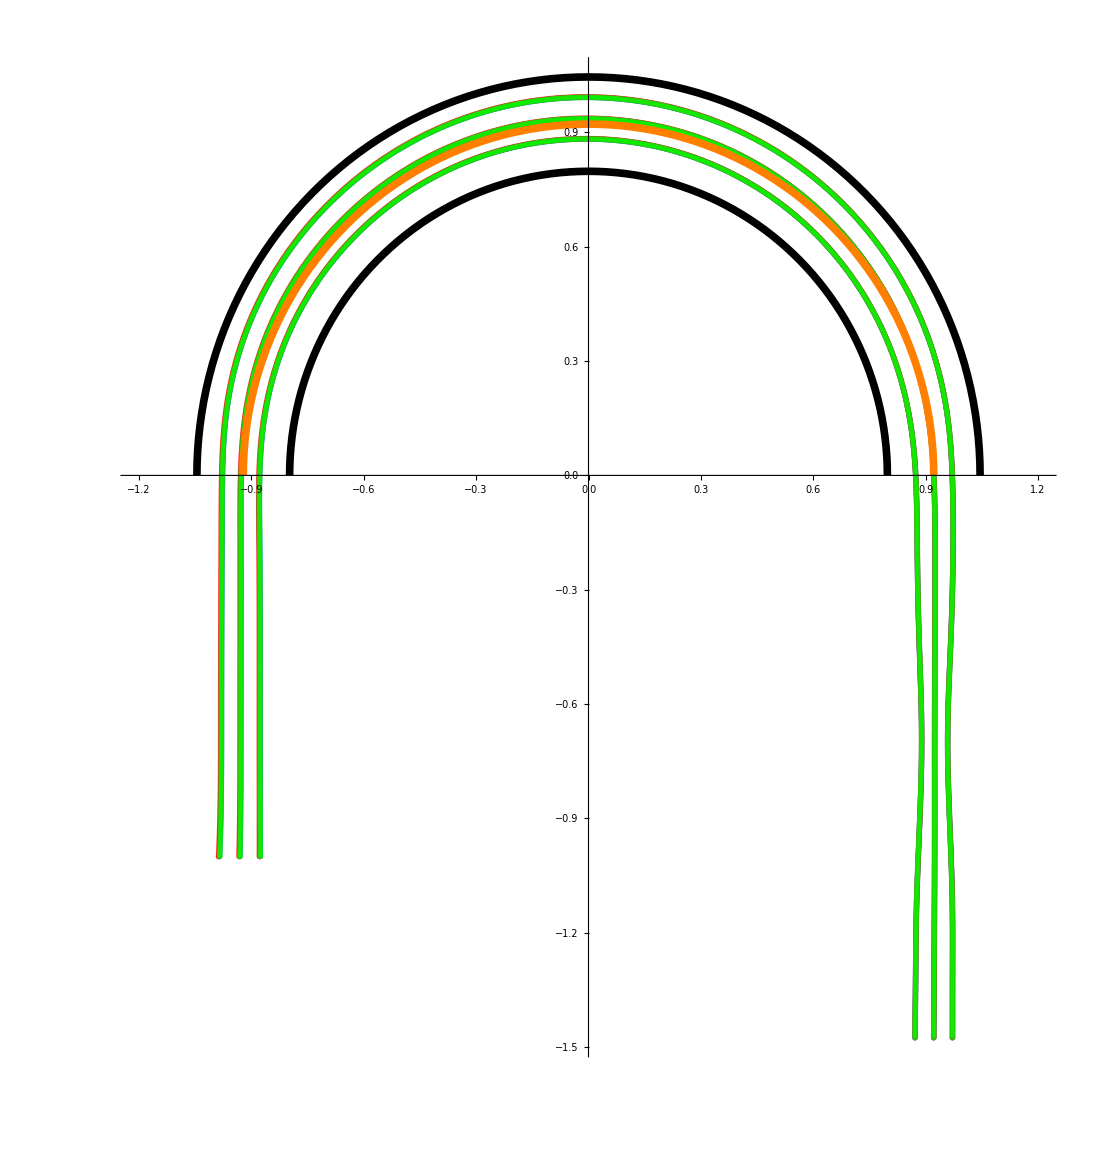

```mathematica
Show[YZPlotDOn,YZPlotD2nd,YZPlotDOff,PipePlot,RConst,ImageSize->1100,AspectRatio->Automatic,PlotRange->{{-1.2,1.2},Automatic}]
```

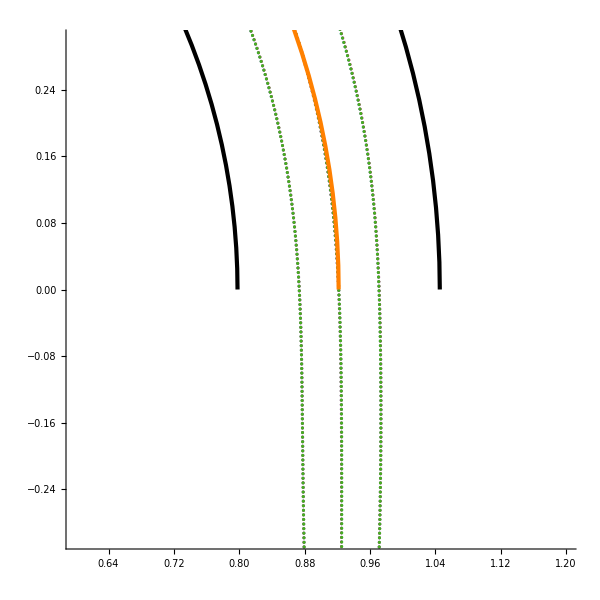

```mathematica
Show[YZPlotDOn,YZPlotD2nd,YZPlotDOff,PipePlot,RConst,ImageSize->600,AspectRatio->Automatic,PlotRange->{{0.6,1.2},{-0.3,0.3}}]
```

### |B| along the field lines including Inlet and Outlet

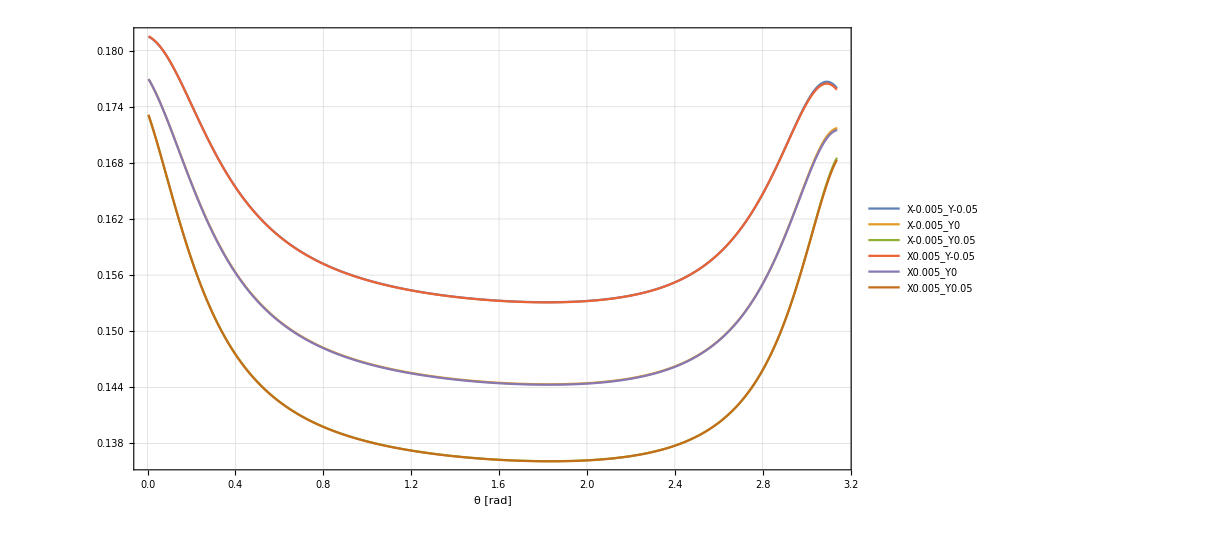

```mathematica
ListLinePlot[Table[Transpose[{BLineAngleDOn[[ii]],BLineFilesDOn[[ii,DataRxBStartDOn[[ii]];;DataOutletStartDOn[[ii]]-1,4]]}],{ii,1,horilines*vertilines}],ImageSize->900,(*PlotRange->{0,0.4},*)Frame->True,FrameLabel->{{None,None},{"θ [rad]","RxB |B|"}},FrameStyle->15,GridLines->Automatic,PlotLegends->BLineNames]
```

```mathematica
InletBlineDOn=ListLinePlot[Table[Transpose[{BLineFilesDOn[[ii,1;;DataRxBStartDOn[[ii]]-1,3]],BLineFilesDOn[[ii,1;;DataRxBStartDOn[[ii]]-1,4]]}],{ii,1,horilines*vertilines}],ImageSize->900,(*PlotRange->{0,0.4},*)Frame->True,FrameLabel->{{None,None},{"z [m]","Inlet |B|"}},FrameStyle->15,GridLines->Automatic,PlotRange->{-0.01,0.35},PlotStyle->Directive[Blue,Opacity[0.5]],PlotRangePadding->{None,None},ImagePadding->{{60, 1},{50,40}}];
InletBlineD2nd=ListLinePlot[Table[Transpose[{BLineFilesD2nd[[ii,1;;DataRxBStartD2nd[[ii]]-1,3]],BLineFilesD2nd[[ii,1;;DataRxBStartD2nd[[ii]]-1,4]]}],{ii,1,horilines*vertilines}],ImageSize->900,(*PlotRange->{0,0.4},*)Frame->True,FrameLabel->{{None,None},{"z [m]","Inlet |B|"}},FrameStyle->15,GridLines->Automatic,PlotRange->{-0.01,0.35},PlotStyle->Directive[Red,Opacity[0.5]],PlotRangePadding->{None,None},ImagePadding->{{60, 1},{50,40}}];
InletBlineDOff=ListLinePlot[Table[Transpose[{BLineFilesDOff[[ii,1;;DataRxBStartDOff[[ii]]-1,3]],BLineFilesDOff[[ii,1;;DataRxBStartDOff[[ii]]-1,4]]}],{ii,1,horilines*vertilines}],ImageSize->900,(*PlotRange->{0,0.4},*)Frame->True,FrameLabel->{{None,None},{"z [m]","Inlet |B|"}},FrameStyle->15,GridLines->Automatic,PlotRange->{-0.01,0.35},PlotStyle->Directive[Green,Opacity[0.5]],PlotRangePadding->{None,None},ImagePadding->{{60, 1},{50,40}}];
InletBlines=Show[InletBlineDOn,(*InletBlineDOnBxDOff,*)InletBlineDOff,ImageSize->510];
```

```mathematica
RxBBLineDOn=ListLinePlot[Table[Transpose[{BLineAngleDOn[[ii]],BLineFilesDOn[[ii,DataRxBStartDOn[[ii]];;DataOutletStartDOn[[ii]]-1,4]]}],{ii,1,horilines*vertilines}],ImageSize->900,(*PlotRange->{0,0.4},*)Frame->True,FrameLabel->{{None,None},{"θ [rad]","RxB |B|"}},FrameStyle->15,GridLines->Automatic,PlotStyle->Opacity[0.5,Blue],PlotRange->{-0.01,0.35},PlotRangePadding->{None,None},ImagePadding->{{0, 1},{50,40}}];
RxBBLineD2nd=ListLinePlot[Table[Transpose[{BLineAngleD2nd[[ii]],BLineFilesD2nd[[ii,DataRxBStartD2nd[[ii]];;DataOutletStartD2nd[[ii]]-1,4]]}],{ii,1,horilines*vertilines}],ImageSize->900,(*PlotRange->{0,0.4},*)Frame->True,FrameLabel->{{None,None},{"θ [rad]","RxB |B|"}},FrameStyle->15,GridLines->Automatic,PlotStyle->Opacity[0.5,Red],PlotRange->{-0.01,0.35},PlotRangePadding->{None,None},ImagePadding->{{0, 1},{50,40}}];
RxBBLineDOff=ListLinePlot[Table[Transpose[{BLineAngleDOff[[ii]],BLineFilesDOff[[ii,DataRxBStartDOff[[ii]];;DataOutletStartDOff[[ii]]-1,4]]}],{ii,1,horilines*vertilines}],ImageSize->900,(*PlotRange->{0,0.4},*)Frame->True,FrameLabel->{{None,None},{"θ [rad]","RxB |B|"}},FrameStyle->15,GridLines->Automatic,PlotStyle->Opacity[0.5,Green],PlotRange->{-0.01,0.35},PlotRangePadding->{None,None},ImagePadding->{{0, 1},{50,40}}];
```

```mathematica
RxBBlines=Show[RxBBLineDOn,RxBBLineD2nd,RxBBLineDOff,ImageSize->450];
```

```mathematica
OutletBlineDOn=ListLinePlot[Table[Transpose[{-BLineFilesDOn[[ii,DataOutletStartDOn[[ii]];;-1,3]],BLineFilesDOn[[ii,DataOutletStartDOn[[ii]];;-1,4]]}],{ii,1,horilines*vertilines}],ImageSize->900,(*PlotRange->{0,0.4},*)Frame->True,FrameLabel->{{None,None},{"-z [m]","Outlet |B|"}},FrameStyle->15,GridLines->Automatic,PlotRange->{-0.01,0.35},PlotStyle->Directive[Blue,Opacity[0.5]],PlotRangePadding->{None,None},ImagePadding->{{0, 1},{50,40}}];
OutletBlineD2nd=ListLinePlot[Table[Transpose[{-BLineFilesD2nd[[ii,DataOutletStartD2nd[[ii]];;-1,3]],BLineFilesD2nd[[ii,DataOutletStartD2nd[[ii]];;-1,4]]}],{ii,1,horilines*vertilines}],ImageSize->900,(*PlotRange->{0,0.4},*)Frame->True,FrameLabel->{{None,None},{"-z [m]","Outlet |B|"}},FrameStyle->15,GridLines->Automatic,PlotRange->{-0.01,0.35},PlotStyle->Directive[Red,Opacity[0.5]],PlotRangePadding->{None,None},ImagePadding->{{0, 1},{50,40}}];
OutletBlineDOff=ListLinePlot[Table[Transpose[{-BLineFilesDOff[[ii,DataOutletStartDOff[[ii]];;-1,3]],BLineFilesDOff[[ii,DataOutletStartDOff[[ii]];;-1,4]]}],{ii,1,horilines*vertilines}],ImageSize->900,(*PlotRange->{0,0.4},*)Frame->True,FrameLabel->{{None,None},{"-z [m]","Outlet |B|"}},FrameStyle->15,GridLines->Automatic,PlotRange->{-0.01,0.35},PlotStyle->Directive[Green,Opacity[0.5]],PlotRangePadding->{None,None},ImagePadding->{{0, 1},{50,40}}];
OutletBlines=Show[OutletBlineDOn,(*OutletBlineDOnBxDOff,*)OutletBlineDOff,ImageSize->450];
```

```mathematica
alpha2=ArcTan[0.5/900.]
```

0.000555555

```mathematica
-Cos[alpha2]*(-Sin[2*alpha2])+Cos[2*alpha2]*(-Sin[alpha2])
```

0.000555555

```mathematica
Sqrt[0.001^2+(1*10^-7)^2]
```

0.001

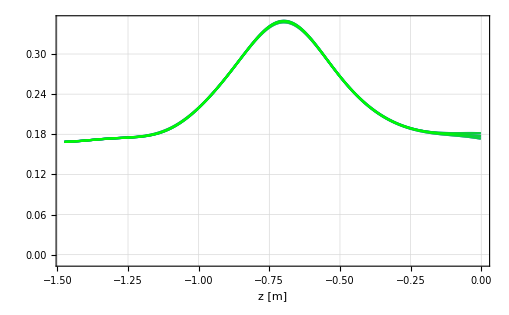
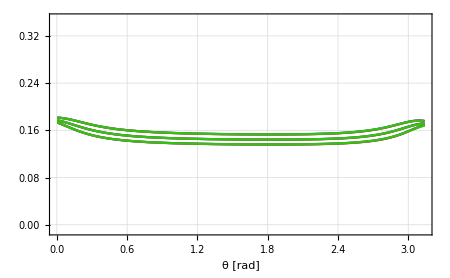
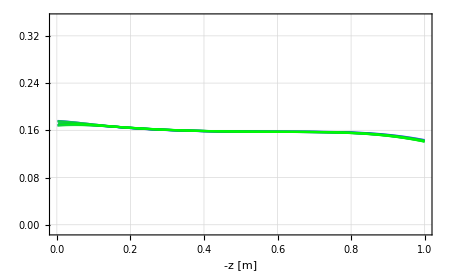

```mathematica
Row[{InletBlines,RxBBlines,OutletBlines}]
```

### XY positions at RxB end. If “artificial” drift is added, again removed at results for comparison

```mathematica
DetPosPlotDOn=ListPlot[Table[{BLineFilesDOn[[i,DataOutletStartDOn[[i]]-1,2]]+R1,BLineFilesDOn[[i,DataOutletStartDOn[[i]]-1,1]]},{i,1,horilines*vertilines}],AspectRatio->Automatic,PlotStyle->Blue];
DetPosPlotD2nd=ListPlot[Table[{BLineFilesD2nd[[i,DataOutletStartD2nd[[i]]-1,2]]+R1,BLineFilesD2nd[[i,DataOutletStartD2nd[[i]]-1,1]]},{i,1,horilines*vertilines}],AspectRatio->Automatic,PlotStyle->Red];
DetPosPlotDOff=ListPlot[Table[{BLineFilesDOff[[i,DataOutletStartDOff[[i]]-1,2]]+R1,BLineFilesDOff[[i,DataOutletStartDOff[[i]]-1,1]]},{i,1,horilines*vertilines}],AspectRatio->Automatic,PlotStyle->Green];
```

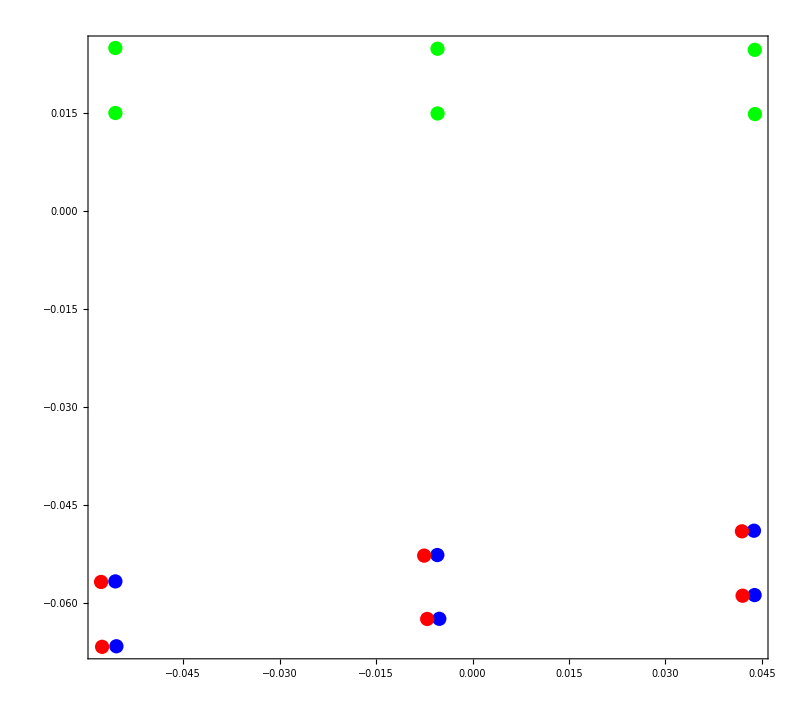

```mathematica
Show[DetPosPlotDOn,DetPosPlotD2nd,DetPosPlotDOff,ImageSize->800,Frame->True,PlotRange->All]
```

```mathematica
0.26/7.5
```

0.0346667

### XY at Detector position

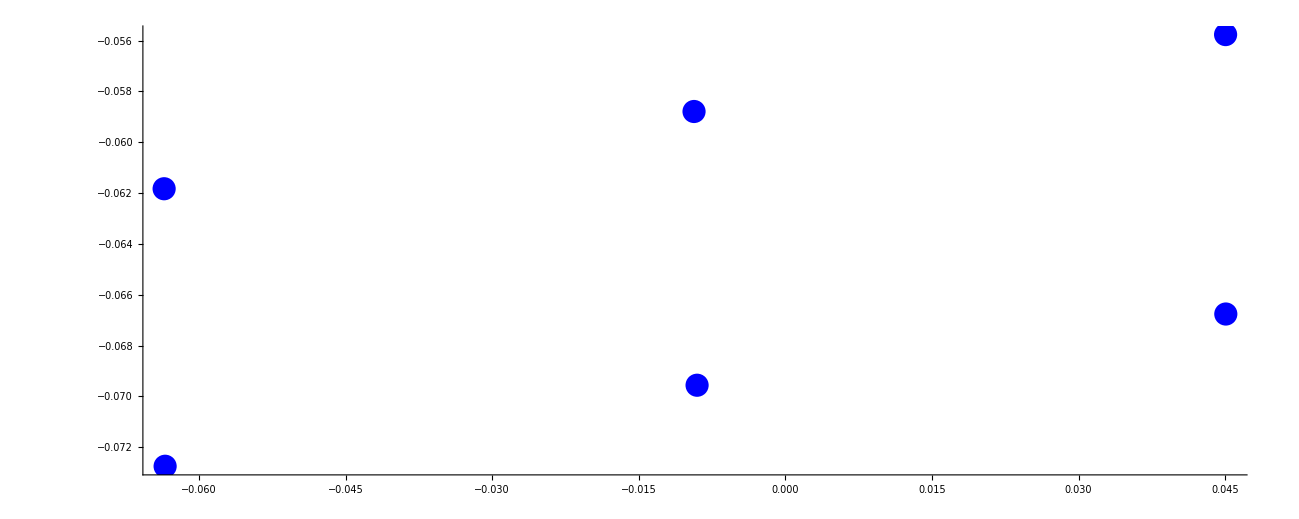

```mathematica
DetPlotDOn=ListPlot[Table[{BLineFilesDOn[[i,-1,2]]+R1,BLineFilesDOn[[i,-1,1]]},{i,1,horilines*vertilines}],AspectRatio->Automatic,PlotStyle->Blue]
```

### last z coordinate: → program gives out last data-point inside RxB

```mathematica
(*ListPlot[Table[{BLineFilesDOnBxDOn[[i,-1,2]]+R1,BLineFilesDOnBxDOn[[i,-1,1]]},{i,1,horilines*vertilines}],Frame->True,FrameLabel->{{"x [m]",None},{"y - R [m]","LastPos XY"}},ImageSize->800,FrameStyle->20]*)
```

## Trajectories (also Compare with B lines)

Import

```mathematica
OS="Linux";Folder="/home/dmoser/MagSimResults";SubFolder="/NoMoS_newTRAJtest_Bcompare/";
```

### Info File

```mathematica
TrajInfoFile=Import[Folder<>SubFolder<>"info.txt","Table"]
```

{{R1,0.921622},{blineStartZ,-1.475}}

```mathematica
ConfigFile=Flatten[Import[Folder<>SubFolder<>"*.config","Table"],1];
```

```mathematica
ParticleN=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="ParticleN"&),_,_}],1],3]][[1]];
EStep=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="ESTEP"&),_,_}],1],3]][[1]];EMin=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="EMIN"&),_,_}],1],3]][[1]];EMax=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="EMAX"&),_,_}],1],3]][[1]];ThetaStep=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="thetastep"&),_,_}],1],3]][[1]]/180*Pi;ThetaMin=0.;ThetaMax=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="thetamax"&),_,_}],1],3]][[1]]/180*Pi;
PhiMin=0;
PhiMax=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="phimax"&),_,_}],1],3]][[1]]/180*Pi;
PhiStep=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="phistep"&),_,_}],1],3]][[1]]/180*Pi;
horilines=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="horilines"&),_,_}],1],3]][[1]];vertilines=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="vertilines"&),_,_}],1],3]][[1]];apertX=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="ApertX"&),_,_}],1],3]][[1]];apertY=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="ApertY"&),_,_}],1],3]][[1]];R1=TrajInfoFile[[1,2]];
EdgeLinesWMiddleList={1,vertilines,(horilines*vertilines+1)/2,(horilines-1)*vertilines+1,horilines*vertilines}
```

{1,3,5,7,9}

```mathematica
XStep=apertX/(horilines-1);YStep=apertY/(vertilines-1);
```

```mathematica
XSteps=Table["X"<>ToString[If[-apertX/2+XStep*x==0.,0,-apertX/2+XStep*x]],{x,0,horilines-1}]
YSteps=Table["Y"<>ToString[If[-apertY/2+YStep*x==0.,0,-apertY/2+YStep*x]],{x,0,vertilines-1}]
```

{X-0.005,X0,X0.005}

{Y-0.05,Y0,Y0.05}

```mathematica
CenterXY=Flatten[Table[Table[
XSteps[[x]]<>"_"<>YSteps[[y]],
{y,1,vertilines}],
{x,1,horilines}]]
```

{X-0.005_Y-0.05,X-0.005_Y0,X-0.005_Y0.05,X0_Y-0.05,X0_Y0,X0_Y0.05,X0.005_Y-0.05,X0.005_Y0,X0.005_Y0.05}

```mathematica
ThetaMax/Pi*180
```

20.

```mathematica
ThetaStep/Pi*180
```

20.

### import. Format: x,y,z, vx,vy,vz, Bx,By,Bz, Gx,Gy,Gz, Gbx,Gby,Gbz, Ekin, Eerr, time, Btheta, theta

```mathematica
testtraj=
Table[
Table[
Table[
Table[
Import[
Folder<>SubFolder<>"trajectories/"<>
CenterXY[[line]]<>"_th"<>If[theta==0,"0",ToString[N[theta]]]<>
"_Ekin"<>ToString[IntegerPart[Ekin]]<>"keV_"<>
"phi"<>If[phi==0,"0",ToString[N[phi]]]<>"_1.txt","Table"
],
{phi,PhiMin,PhiMax,PhiStep}],
{Ekin,EMin,EMax,EStep}],
{theta,ThetaMin,ThetaMax,ThetaStep}],
{line,1,horilines*vertilines}];
```

First checks of the Trajectories

### Plot start Position + guiding center position

```mathematica
Theta=2;Ekin=2;
```

```mathematica
FirstXYAll=Flatten[Table[Transpose[
{
testtraj[[All,Theta,Ekin,phi,1,2]]-R1,
testtraj[[All,Theta,Ekin,phi,1,1]]
}],{phi,1,PhiMax/PhiStep+1}],1];
FirstGuidXYAll=Flatten[Table[Transpose[
{
testtraj[[All,Theta,Ekin,phi,1,11]]-R1,
testtraj[[All,Theta,Ekin,phi,1,10]]
}],{phi,1,PhiMax/PhiStep+1}],1];
```

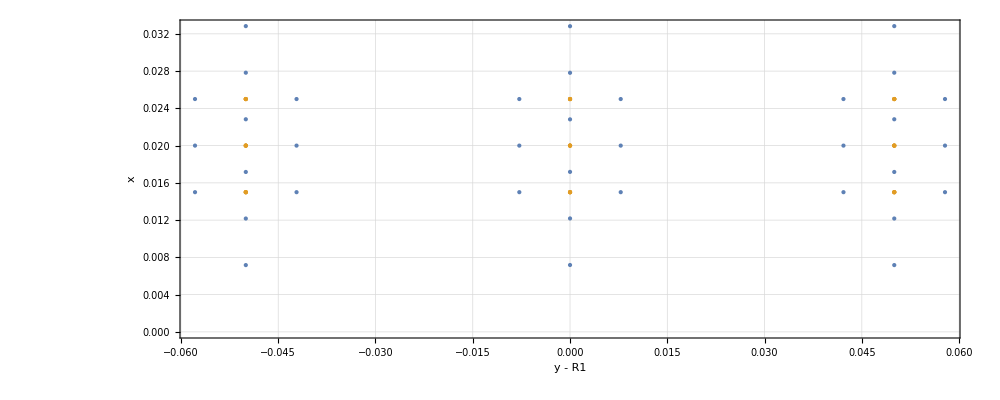

```mathematica
ListPlot[{FirstXYAll,FirstGuidXYAll},ImageSize->1000,FrameLabel->{{"x",None},{"y - R1",Row[{"startP of ",Style["traj",ColorData[97,"ColorList"][[1]]]," + ",Style["GuidC",ColorData[97,"ColorList"][[2]]] ," for different ϕ"}]}},AspectRatio->Automatic,PlotStyle->PointSize->Medium,GridLines->Automatic,Frame->True,GridLines->Automatic,FrameStyle->15,AspectRatio->Automatic,PlotStyle->PointSize->Medium,PlotRange->All]
```

```mathematica
ColorData[97,"ColorList"][[2]]
```

RGBColor[0.880722, 0.611041, 0.142051]

### XY at start of RXB!

```mathematica
FirstRxBPos=Table[Table[
First[Flatten[Position[testtraj[[line,Theta,Ekin,phi,All,11;;12]],{_?(#>0&),_?(#>=0&)}]]],
{phi,1,PhiMax/PhiStep+1}],
{line,1,horilines*vertilines}];
```

```mathematica
FirstRxBPos[[1,All]]
```

{576,577,578,577}

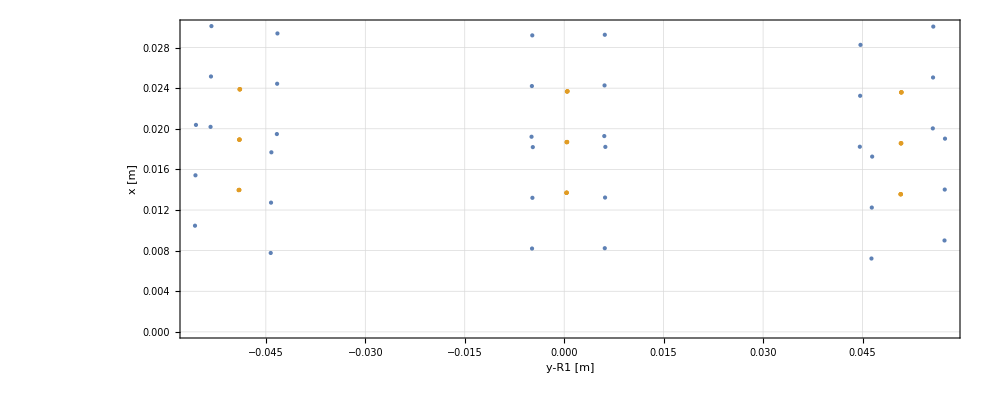

```mathematica
ListPlot[
{
Flatten[
Table[
Table[
{
testtraj[[line,Theta,Ekin,phi,FirstRxBPos[[line,phi]],2]]-R1,
testtraj[[line,Theta,Ekin,phi,FirstRxBPos[[line,phi]],1]]
},
{line,1,horilines*vertilines}],
{phi,1,PhiMax/PhiStep+1}],1],
Flatten[Table[
Table[
{
testtraj[[line,Theta,Ekin,phi,FirstRxBPos[[line,phi]],11]]-R1,
testtraj[[line,Theta,Ekin,phi,FirstRxBPos[[line,phi]],10]]
},
{line,1,horilines*vertilines}],
{phi,1,PhiMax/PhiStep+1}],1]
},
ImageSize->1000,Frame->True,FrameLabel->{{"x [m]",None},{"y-R1 [m]","XY at start of RxB for each line and phi"}},GridLines->Automatic,FrameStyle->15,AspectRatio->Automatic,PlotStyle->PointSize->Medium,PlotRange->All
]
```

### one specific line

```mathematica
specline=6;
```

```mathematica
CenterXY[[specline]]
```

X0_Y0.05

```mathematica
FirstRxBPos[[specline,1]]
```

575

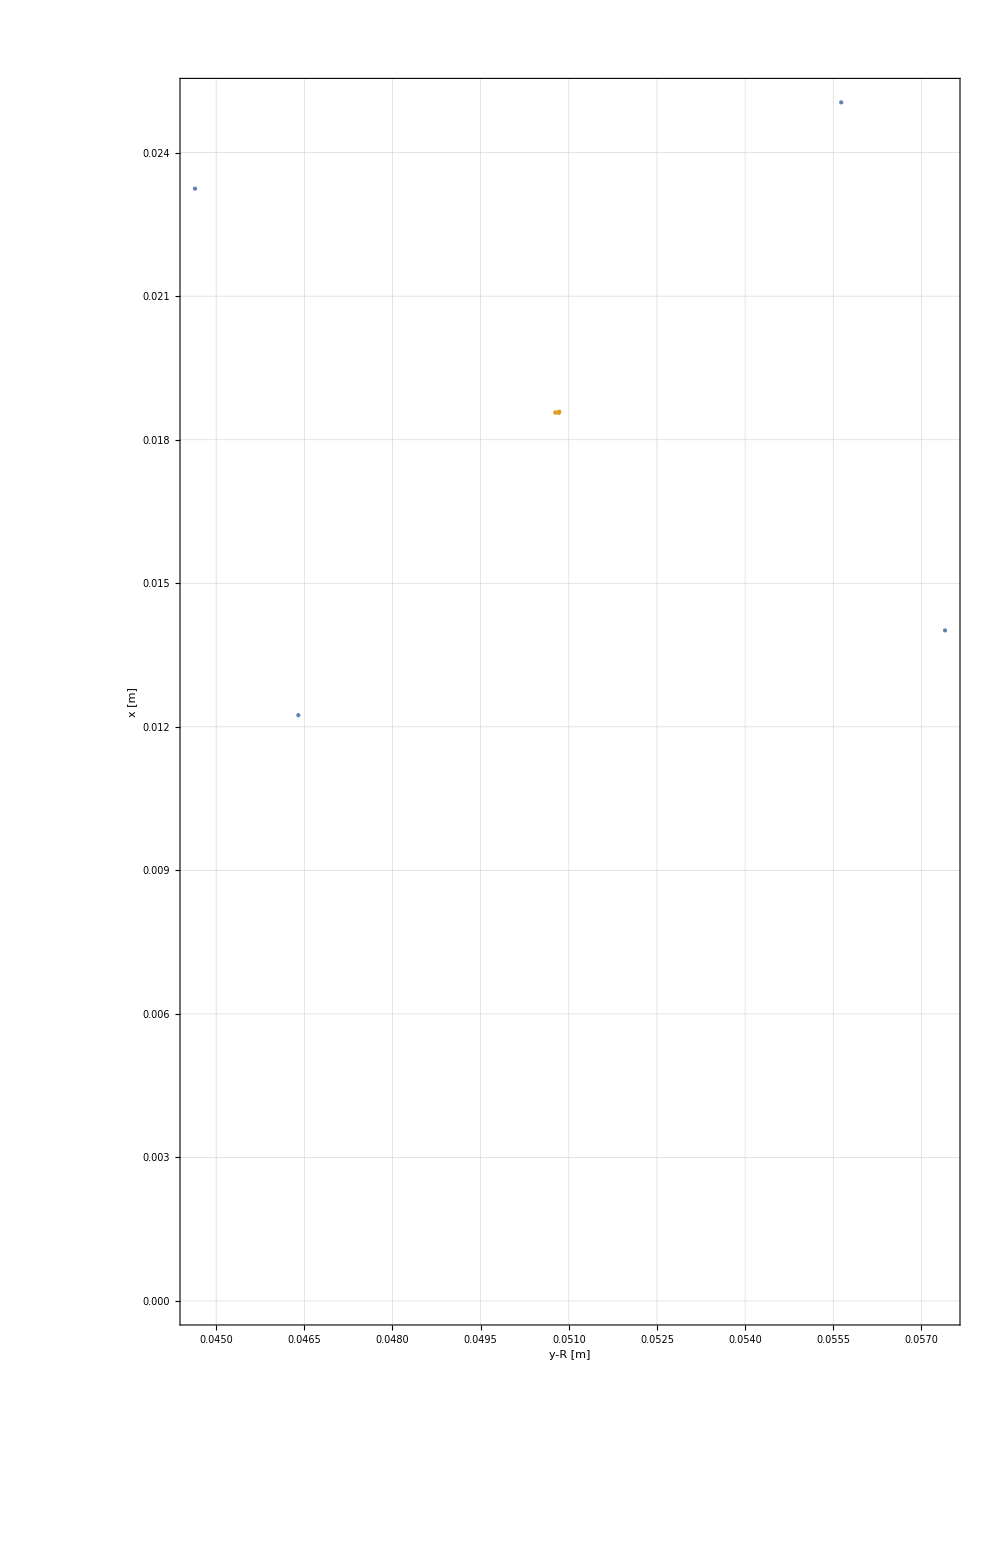

```mathematica
ListPlot[
{
Flatten[
Table[
Table[
{
testtraj[[line,Theta,Ekin,phi,FirstRxBPos[[line,phi]],2]]-R1,
testtraj[[line,Theta,Ekin,phi,FirstRxBPos[[line,phi]],1]]
},
{line,{specline}}],
{phi,1,PhiMax/PhiStep+1}],1],
Flatten[Table[
Table[
{
testtraj[[line,Theta,Ekin,phi,FirstRxBPos[[line,phi]],11]]-R1,
testtraj[[line,Theta,Ekin,phi,FirstRxBPos[[line,phi]],10]]
},
{line,{specline}}],
{phi,1,PhiMax/PhiStep+1}],1]
},
ImageSize->1000,Frame->True,FrameLabel->{{"x [m]",None},{"y-R [m]","XY at start of RxB for line "<>ToString[CenterXY[[specline]]]}},GridLines->Automatic,FrameStyle->15,AspectRatio->Automatic,PlotStyle->PointSize->Medium,PlotRange->All
]
```

### only GC of specific line for detailed check

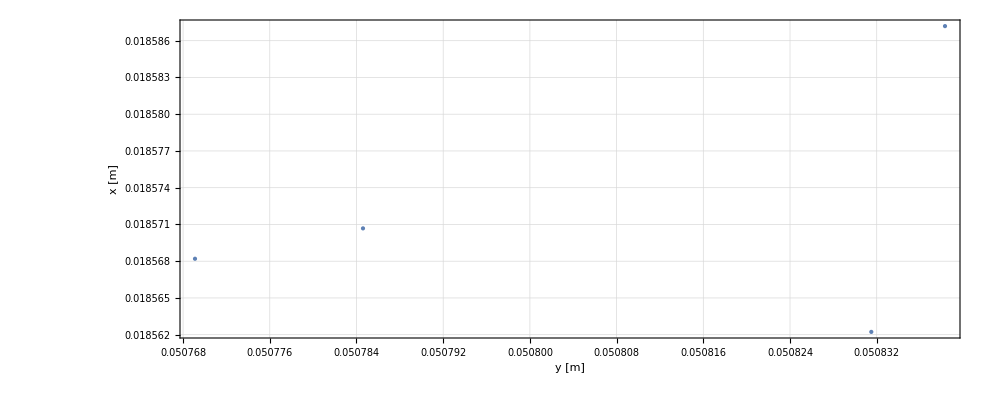

```mathematica
ListPlot[
Flatten[Table[
Table[
{
testtraj[[line,Theta,Ekin,phi,FirstRxBPos[[line,phi]],11]]-R1,
testtraj[[line,Theta,Ekin,phi,FirstRxBPos[[line,phi]],10]]
},
{line,{specline}}],
{phi,1,PhiMax/PhiStep+1}],1],
ImageSize->1000,Frame->True,FrameLabel->{{"x [m]",None},{"y [m]","StartXY of RxB of GuidCenter for each line and phi (y - R1)"}},GridLines->Automatic,FrameStyle->15,AspectRatio->Automatic,PlotStyle->PointSize->Medium,PlotRange->All
]
```

### follow traj along the data points with different ϕ

```mathematica
(*Manipulate[
ListPlot[
{
Flatten[
Table[
Table[
{
testtraj[[line,Theta,Ekin,phi,point,2]],
testtraj[[line,Theta,Ekin,phi,point,1]]
},
{line,{specline}}],
{phi,1,PhiMax/PhiStep+1}],1],
Flatten[Table[
Table[
{
testtraj[[line,Theta,Ekin,phi,point,11]],
testtraj[[line,Theta,Ekin,phi,point,10]]
},
{line,{specline}}],
{phi,1,PhiMax/PhiStep+1}],1]
},
ImageSize->800,Frame->True,FrameLabel->{{"x [m]",None},{"y [m]","StartXY of RxB of GuidCenter for each line and phi (y - R1)"}},GridLines->Automatic,FrameStyle->15,AspectRatio->Automatic,PlotStyle->PointSize->Medium,PlotRange->All
],{point,1,1047,20}]*)
```

### XY Position at end of RxB dependent on different starting parameters (all phi, choose ekin und theta)

```mathematica
LastRxBPos=Table[Table[
Last[Flatten[Position[testtraj[[line,Theta,Ekin,phi,All,11;;12]],{_?(#<0&),_?(#>=0&)}]]],
{phi,1,PhiMax/PhiStep+1}],
{line,1,horilines*vertilines}];
```

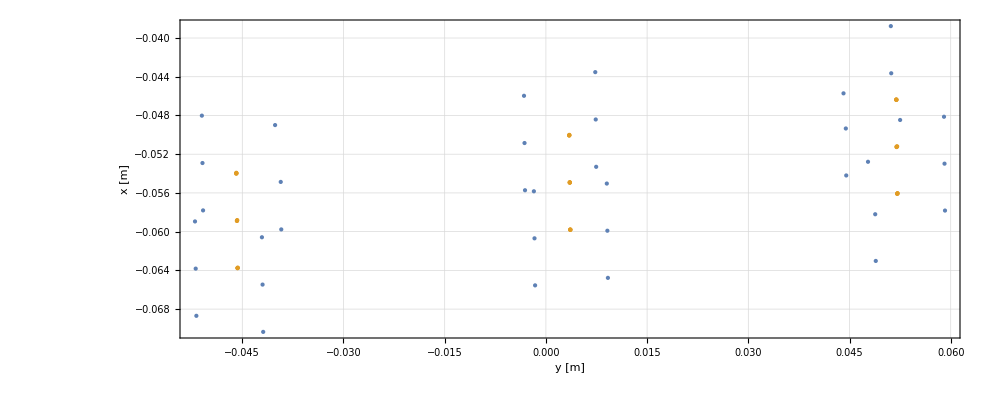

```mathematica
ListPlot[
{
Flatten[Table[
Table[
{testtraj[[line,Theta,Ekin,phi,LastRxBPos[[line,phi]],2]]+R1,testtraj[[line,Theta,Ekin,phi,LastRxBPos[[line,phi]],1]]},
{line,1,horilines*vertilines}],
{phi,1,PhiMax/PhiStep+1}],1],
Flatten[Table[
Table[
{testtraj[[line,Theta,Ekin,phi,LastRxBPos[[line,phi]],11]]+R1,testtraj[[line,Theta,Ekin,phi,LastRxBPos[[line,phi]],10]]},
{line,1,horilines*vertilines}],
{phi,1,PhiMax/PhiStep+1}],1]
},
ImageSize->1000,Frame->True,FrameLabel->{{"x [m]",None},{"y [m]","EndXY of GuidCenter for each line and phi (y - R1)"}},GridLines->Automatic,FrameStyle->15,AspectRatio->Automatic,PlotStyle->PointSize->Medium(*,PlotRange->All*)
]
```

### Detector positions

```mathematica
testtraj[[5,2,2,2,1]]
```

{0.0278193,0.921622,-1.47496,33654.2,9.5265×10^7,2.5703×10^8,0.000021946,0.000988815,0.168329,0.02,0.921622,-1.47495,0.0000148627,0.000988998,0.168358,751373.,0.,1.90258×10^-8,0.,0.}

```mathematica
xy=Sqrt[testtraj[[5,2,2,2,1,4]]^2+testtraj[[5,2,2,2,1,5]]^2]
```

9.5265×10^7

```mathematica
ArcTan[xy/testtraj[[5,2,2,2,1,6]]]/Pi*180.
```

20.3366

```mathematica
ArcTan[testtraj[[5,2,2,2,1,4]],testtraj[[5,2,2,2,1,5]]]/Pi*180
```

89.9798

```mathematica
testtraj[[5,2,2,2,-1,1;;3]]
```

{-0.0619286,-0.92489,-0.496545}

```mathematica
testtraj[[5,2,2,2,-1]]
```

{-0.0619286,-0.92489,-0.496545,-7.96119×10^7,4.69957×10^7,-2.58057×10^8,-0.000220323,-0.0000400542,-0.163131,-0.057878,-0.918068,-0.496553,-0.000206311,-0.0000216318,-0.163137,751000.,4.68142×10^-14,1.90066×10^-8,179.921,19.6505}

```mathematica
LastDataPoints=Table[testtraj[[line,Theta,Ekin,phi]]//Length,{line,1,horilines*vertilines},{phi,1,PhiMax/PhiStep+1}];
```

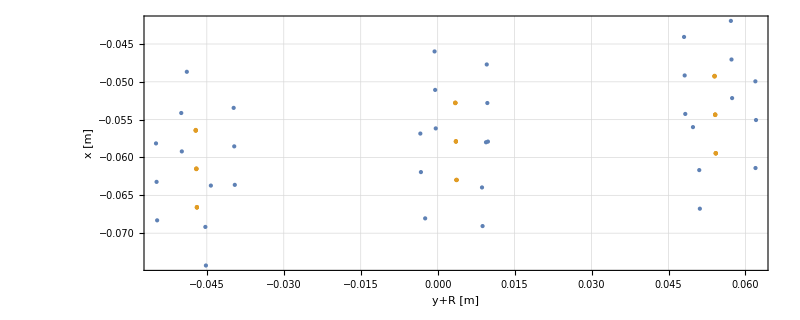

```mathematica
ListPlot[
{
Flatten[
Table[
Table[
{
testtraj[[line,Theta,Ekin,phi,LastDataPoints[[line,phi]],2]]+R1,
testtraj[[line,Theta,Ekin,phi,LastDataPoints[[line,phi]],1]]
},
{line,1,horilines*vertilines}],
{phi,1,PhiMax/PhiStep+1}],1],
Flatten[Table[
Table[
{
testtraj[[line,Theta,Ekin,phi,LastDataPoints[[line,phi]],11]]+R1,
testtraj[[line,Theta,Ekin,phi,LastDataPoints[[line,phi]],10]]
},
{line,1,horilines*vertilines}],
{phi,1,PhiMax/PhiStep+1}],1]
},
ImageSize->800,Frame->True,FrameLabel->{{"x [m]",None},{"y+R [m]","LastXY at Detector (z=-0.5m)"}},GridLines->Automatic,FrameStyle->15,AspectRatio->Automatic,PlotStyle->PointSize->Medium,PlotRange->All
]
```

### Plot for deviation in drifts dependent on starting X-compensation

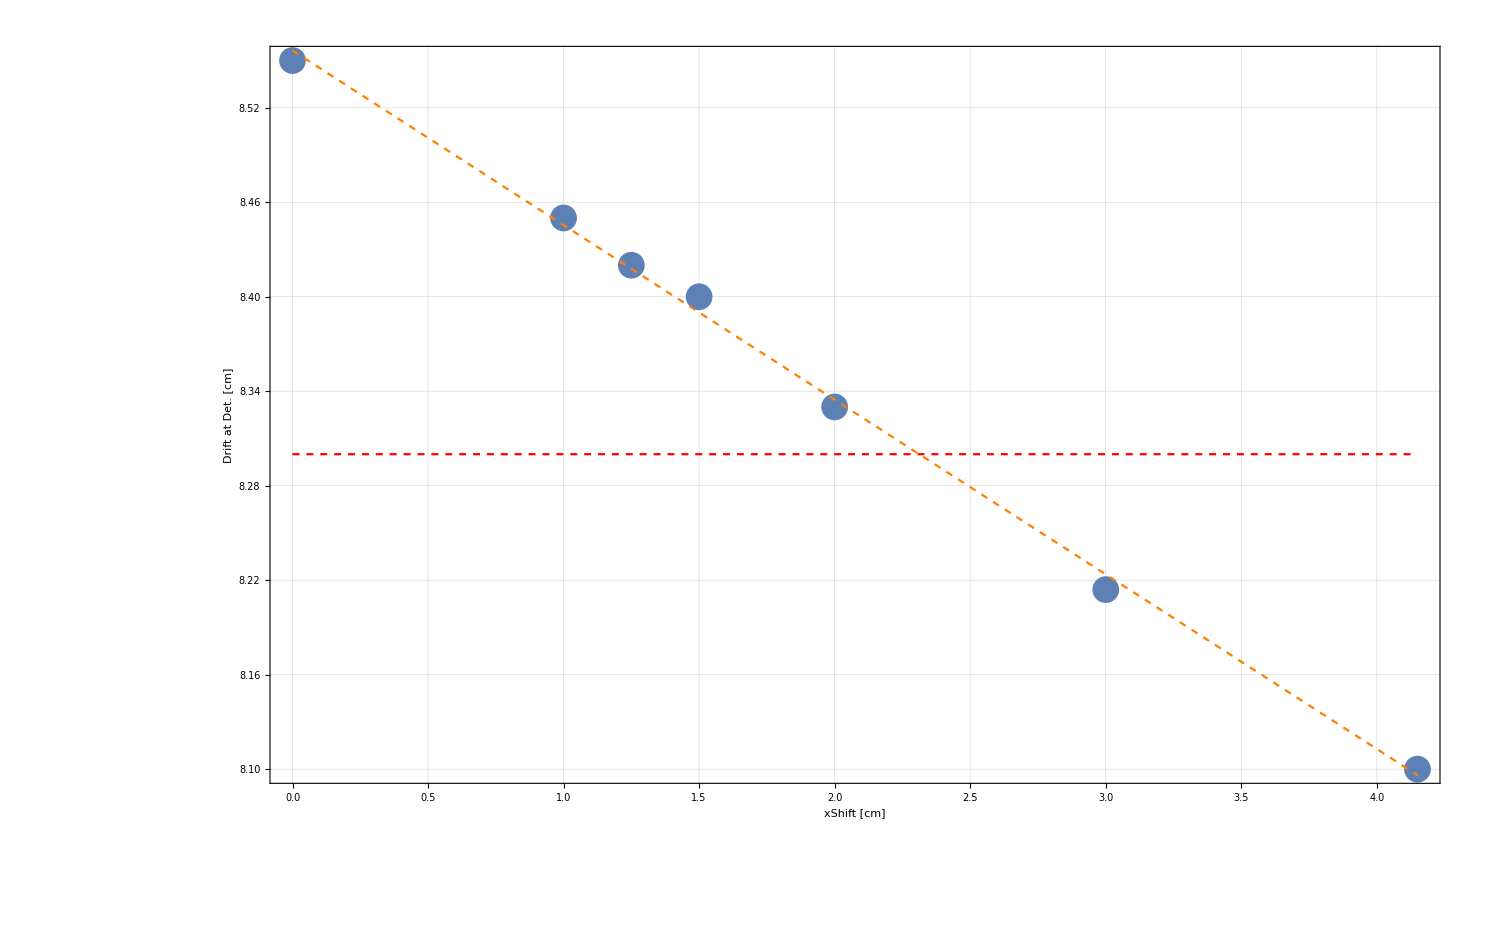

```mathematica
Legended[
Show[
ListPlot[
Transpose[{
{0,1,1.25,1.5,2,3,4.15},
{8.55,8.45,8.42,8.4,8.33,8.214,8.1}
}],ImageSize->1500,Frame->True,FrameLabel->{{"Drift at Det. [cm]",None},{"xShift [cm]","Drift distance for different Xshifts of aperture"}},GridLines->Automatic,FrameStyle->15
],
Plot[8.55634-0.110885*x,{x,0,4.15},PlotStyle->Directive[Orange,Dashed]],
Plot[8.3,{x,0,4.15},PlotStyle->Directive[Red,Dashed]]
],
Placed[Column[
{
PointLegend[{ColorData[97,"ColorList"][[1]]},{"X pos. of GuidC of central traj"},LegendMarkerSize->30,LabelStyle->20],
LineLegend[{Directive[Dashed,Orange]},{"Fitted line through points"},LegendMarkerSize->30,LabelStyle->20],
LineLegend[{Directive[Dashed,Red]},{"Drift of bline + analyt. drift (Xshift 0)"},LegendMarkerSize->30,LabelStyle->20]
},Frame->True,Background->White],{0.75,0.75}]
]
```

```mathematica
Fit[Transpose[{
{0,1,1.25,1.5,2,3,4.15},
{8.55,8.45,8.42,8.4,8.33,8.214,8.1}
}],{1,x},x]
```

8.55634-0.110885 x

### GuidC for one specific line

```mathematica
specline=6;
```

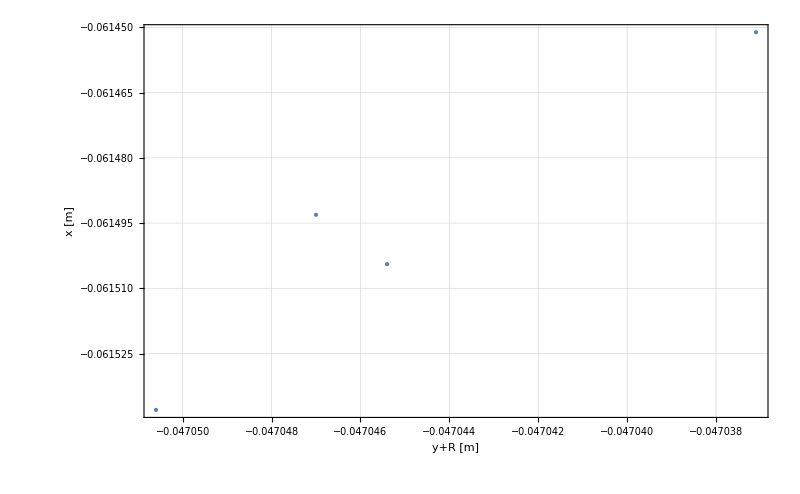

```mathematica
ListPlot[
Flatten[Table[
Table[
{
testtraj[[line,Theta,Ekin,phi,LastDataPoints[[line,phi]],11]]+R1,
testtraj[[line,Theta,Ekin,phi,LastDataPoints[[line,phi]],10]]
},
{line,{specline}}],
{phi,1,PhiMax/PhiStep+1}],1],
ImageSize->800,Frame->True,FrameLabel->{{"x [m]",None},{"y+R [m]","Last GuidC at Detector (z=-0.3m) for line " <>ToString[CenterXY[[specline]]]}},GridLines->Automatic,FrameStyle->15,PlotStyle->PointSize->Medium,PlotRange->All
]
```

### Deviation calculations IN PROGRESS

```mathematica
LastRxBXY=Table[
Table[
{testtraj[[line,Theta,Ekin,phi,LastRxBPos[[line,phi]],11]],testtraj[[line,Theta,Ekin,phi,LastRxBPos[[line,phi]],10]]},
{line,1,horilines*vertilines}],
{phi,1,PhiMax/PhiStep+1}];
```

```mathematica
MaxDeviation[lineList_List]:=
Max[Table[Norm[#]&/@(lineList[[start]]-#&/@lineList),{start,1,PhiMax/PhiStep+1}]]
```

```mathematica
MaxDeviation[{{-1,0},{2,0},{2,0},{3,5}}]
```

√41

```mathematica
Table[MaxDeviation[LastRxBXY[[All,line]]],{line,1,15}]
```

Part::partw: Part 10 of {{-0.86957,-0.0560956},{-0.917999,-0.0597993},{-0.967327,-0.0637708},{-0.869653,-0.051265},{-0.918085,-0.0549352},{-0.967423,-0.0588911},{-0.869659,-0.0463815},{-0.918176,-0.0500711},{-0.967524,-0.0540115}} does not exist.

Part::partw: Part 11 of {{-0.86957,-0.0560956},{-0.917999,-0.0597993},{-0.967327,-0.0637708},{-0.869653,-0.051265},{-0.918085,-0.0549352},{-0.967423,-0.0588911},{-0.869659,-0.0463815},{-0.918176,-0.0500711},{-0.967524,-0.0540115}} does not exist.

Part::partw: Part 12 of {{-0.86957,-0.0560956},{-0.917999,-0.0597993},{-0.967327,-0.0637708},{-0.869653,-0.051265},{-0.918085,-0.0549352},{-0.967423,-0.0588911},{-0.869659,-0.0463815},{-0.918176,-0.0500711},{-0.967524,-0.0540115}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{0.0000886457,0.0000410981,0.0000641321,0.000118209,0.0000404925,0.000098176,0.0000528606,0.0000717586,0.0000920142,MaxDeviation[{{{-0.86957,-0.0560956},{-0.917999,-0.0597993},{-0.967327,-0.0637708},{-0.869653,-0.051265},{-0.918085,-0.0549352},{-0.967423,-0.0588911},{-0.869659,-0.0463815},{-0.918176,-0.0500711},{-0.967524,-0.0540115}},{{-0.869543,-0.0560767},{-0.917988,-0.0597912},{-0.967312,-0.0637487},{-0.869615,-0.0512292},{-0.918068,-0.0549175},{-0.967404,-0.0588582},{-0.869692,-0.0463805},{-0.918152,-0.0500428},{-0.967499,-0.0539671}},{{-0.869511,-0.0560295},{-0.918023,-0.0597839},{-0.967298,-0.0637137},{-0.869639,-0.0512141},{-0.918086,-0.0548948},{-0.967372,-0.0588072},{-0.869693,-0.0463406},{-0.918151,-0.0500038},{-0.967513,-0.0539202}},{{-0.869499,-0.0560491},{-0.918022,-0.0598141},{-0.96732,-0.0637624},{-0.869558,-0.0511937},{-0.918091,-0.0549349},{-0.967402,-0.058869},{-0.869701,-0.0463841},{-0.918163,-0.0500548},{-0.967488,-0.0539749}}}⟦All,10⟧],MaxDeviation[{{{-0.86957,-0.0560956},{-0.917999,-0.0597993},{-0.967327,-0.0637708},{-0.869653,-0.051265},{-0.918085,-0.0549352},{-0.967423,-0.0588911},{-0.869659,-0.0463815},{-0.918176,-0.0500711},{-0.967524,-0.0540115}},{{-0.869543,-0.0560767},{-0.917988,-0.0597912},{-0.967312,-0.0637487},{-0.869615,-0.0512292},{-0.918068,-0.0549175},{-0.967404,-0.0588582},{-0.869692,-0.0463805},{-0.918152,-0.0500428},{-0.967499,-0.0539671}},{{-0.869511,-0.0560295},{-0.918023,-0.0597839},{-0.967298,-0.0637137},{-0.869639,-0.0512141},{-0.918086,-0.0548948},{-0.967372,-0.0588072},{-0.869693,-0.0463406},{-0.918151,-0.0500038},{-0.967513,-0.0539202}},{{-0.869499,-0.0560491},{-0.918022,-0.0598141},{-0.96732,-0.0637624},{-0.869558,-0.0511937},{-0.918091,-0.0549349},{-0.967402,-0.058869},{-0.869701,-0.0463841},{-0.918163,-0.0500548},{-0.967488,-0.0539749}}}⟦All,11⟧],MaxDeviation[{{{-0.86957,-0.0560956},{-0.917999,-0.0597993},{-0.967327,-0.0637708},{-0.869653,-0.051265},{-0.918085,-0.0549352},{-0.967423,-0.0588911},{-0.869659,-0.0463815},{-0.918176,-0.0500711},{-0.967524,-0.0540115}},{{-0.869543,-0.0560767},{-0.917988,-0.0597912},{-0.967312,-0.0637487},{-0.869615,-0.0512292},{-0.918068,-0.0549175},{-0.967404,-0.0588582},{-0.869692,-0.0463805},{-0.918152,-0.0500428},{-0.967499,-0.0539671}},{{-0.869511,-0.0560295},{-0.918023,-0.0597839},{-0.967298,-0.0637137},{-0.869639,-0.0512141},{-0.918086,-0.0548948},{-0.967372,-0.0588072},{-0.869693,-0.0463406},{-0.918151,-0.0500038},{-0.967513,-0.0539202}},{{-0.869499,-0.0560491},{-0.918022,-0.0598141},{-0.96732,-0.0637624},{-0.869558,-0.0511937},{-0.918091,-0.0549349},{-0.967402,-0.058869},{-0.869701,-0.0463841},{-0.918163,-0.0500548},{-0.967488,-0.0539749}}}⟦All,12⟧],MaxDeviation[{{{-0.86957,-0.0560956},{-0.917999,-0.0597993},{-0.967327,-0.0637708},{-0.869653,-0.051265},{-0.918085,-0.0549352},{-0.967423,-0.0588911},{-0.869659,-0.0463815},{-0.918176,-0.0500711},{-0.967524,-0.0540115}},{{-0.869543,-0.0560767},{-0.917988,-0.0597912},{-0.967312,-0.0637487},{-0.869615,-0.0512292},{-0.918068,-0.0549175},{-0.967404,-0.0588582},{-0.869692,-0.0463805},{-0.918152,-0.0500428},{-0.967499,-0.0539671}},{{-0.869511,-0.0560295},{-0.918023,-0.0597839},{-0.967298,-0.0637137},{-0.869639,-0.0512141},{-0.918086,-0.0548948},{-0.967372,-0.0588072},{-0.869693,-0.0463406},{-0.918151,-0.0500038},{-0.967513,-0.0539202}},{{-0.869499,-0.0560491},{-0.918022,-0.0598141},{-0.96732,-0.0637624},{-0.869558,-0.0511937},{-0.918091,-0.0549349},{-0.967402,-0.058869},{-0.869701,-0.0463841},{-0.918163,-0.0500548},{-0.967488,-0.0539749}}}⟦All,13⟧],MaxDeviation[{{{-0.86957,-0.0560956},{-0.917999,-0.0597993},{-0.967327,-0.0637708},{-0.869653,-0.051265},{-0.918085,-0.0549352},{-0.967423,-0.0588911},{-0.869659,-0.0463815},{-0.918176,-0.0500711},{-0.967524,-0.0540115}},{{-0.869543,-0.0560767},{-0.917988,-0.0597912},{-0.967312,-0.0637487},{-0.869615,-0.0512292},{-0.918068,-0.0549175},{-0.967404,-0.0588582},{-0.869692,-0.0463805},{-0.918152,-0.0500428},{-0.967499,-0.0539671}},{{-0.869511,-0.0560295},{-0.918023,-0.0597839},{-0.967298,-0.0637137},{-0.869639,-0.0512141},{-0.918086,-0.0548948},{-0.967372,-0.0588072},{-0.869693,-0.0463406},{-0.918151,-0.0500038},{-0.967513,-0.0539202}},{{-0.869499,-0.0560491},{-0.918022,-0.0598141},{-0.96732,-0.0637624},{-0.869558,-0.0511937},{-0.918091,-0.0549349},{-0.967402,-0.058869},{-0.869701,-0.0463841},{-0.918163,-0.0500548},{-0.967488,-0.0539749}}}⟦All,14⟧],MaxDeviation[{{{-0.86957,-0.0560956},{-0.917999,-0.0597993},{-0.967327,-0.0637708},{-0.869653,-0.051265},{-0.918085,-0.0549352},{-0.967423,-0.0588911},{-0.869659,-0.0463815},{-0.918176,-0.0500711},{-0.967524,-0.0540115}},{{-0.869543,-0.0560767},{-0.917988,-0.0597912},{-0.967312,-0.0637487},{-0.869615,-0.0512292},{-0.918068,-0.0549175},{-0.967404,-0.0588582},{-0.869692,-0.0463805},{-0.918152,-0.0500428},{-0.967499,-0.0539671}},{{-0.869511,-0.0560295},{-0.918023,-0.0597839},{-0.967298,-0.0637137},{-0.869639,-0.0512141},{-0.918086,-0.0548948},{-0.967372,-0.0588072},{-0.869693,-0.0463406},{-0.918151,-0.0500038},{-0.967513,-0.0539202}},{{-0.869499,-0.0560491},{-0.918022,-0.0598141},{-0.96732,-0.0637624},{-0.869558,-0.0511937},{-0.918091,-0.0549349},{-0.967402,-0.058869},{-0.869701,-0.0463841},{-0.918163,-0.0500548},{-0.967488,-0.0539749}}}⟦All,15⟧]}

```mathematica
Table[MaxDeviation[LastRxBXY[[All,line]]],{line,1,15}]//Max
```

Part::partw: Part 10 of {{-0.86957,-0.0560956},{-0.917999,-0.0597993},{-0.967327,-0.0637708},{-0.869653,-0.051265},{-0.918085,-0.0549352},{-0.967423,-0.0588911},{-0.869659,-0.0463815},{-0.918176,-0.0500711},{-0.967524,-0.0540115}} does not exist.

Part::partw: Part 11 of {{-0.86957,-0.0560956},{-0.917999,-0.0597993},{-0.967327,-0.0637708},{-0.869653,-0.051265},{-0.918085,-0.0549352},{-0.967423,-0.0588911},{-0.869659,-0.0463815},{-0.918176,-0.0500711},{-0.967524,-0.0540115}} does not exist.

Part::partw: Part 12 of {{-0.86957,-0.0560956},{-0.917999,-0.0597993},{-0.967327,-0.0637708},{-0.869653,-0.051265},{-0.918085,-0.0549352},{-0.967423,-0.0588911},{-0.869659,-0.0463815},{-0.918176,-0.0500711},{-0.967524,-0.0540115}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Max[0.000118209,MaxDeviation[{{{-0.86957,-0.0560956},{-0.917999,-0.0597993},{-0.967327,-0.0637708},{-0.869653,-0.051265},{-0.918085,-0.0549352},{-0.967423,-0.0588911},{-0.869659,-0.0463815},{-0.918176,-0.0500711},{-0.967524,-0.0540115}},{{-0.869543,-0.0560767},{-0.917988,-0.0597912},{-0.967312,-0.0637487},{-0.869615,-0.0512292},{-0.918068,-0.0549175},{-0.967404,-0.0588582},{-0.869692,-0.0463805},{-0.918152,-0.0500428},{-0.967499,-0.0539671}},{{-0.869511,-0.0560295},{-0.918023,-0.0597839},{-0.967298,-0.0637137},{-0.869639,-0.0512141},{-0.918086,-0.0548948},{-0.967372,-0.0588072},{-0.869693,-0.0463406},{-0.918151,-0.0500038},{-0.967513,-0.0539202}},{{-0.869499,-0.0560491},{-0.918022,-0.0598141},{-0.96732,-0.0637624},{-0.869558,-0.0511937},{-0.918091,-0.0549349},{-0.967402,-0.058869},{-0.869701,-0.0463841},{-0.918163,-0.0500548},{-0.967488,-0.0539749}}}⟦All,10⟧],MaxDeviation[{{{-0.86957,-0.0560956},{-0.917999,-0.0597993},{-0.967327,-0.0637708},{-0.869653,-0.051265},{-0.918085,-0.0549352},{-0.967423,-0.0588911},{-0.869659,-0.0463815},{-0.918176,-0.0500711},{-0.967524,-0.0540115}},{{-0.869543,-0.0560767},{-0.917988,-0.0597912},{-0.967312,-0.0637487},{-0.869615,-0.0512292},{-0.918068,-0.0549175},{-0.967404,-0.0588582},{-0.869692,-0.0463805},{-0.918152,-0.0500428},{-0.967499,-0.0539671}},{{-0.869511,-0.0560295},{-0.918023,-0.0597839},{-0.967298,-0.0637137},{-0.869639,-0.0512141},{-0.918086,-0.0548948},{-0.967372,-0.0588072},{-0.869693,-0.0463406},{-0.918151,-0.0500038},{-0.967513,-0.0539202}},{{-0.869499,-0.0560491},{-0.918022,-0.0598141},{-0.96732,-0.0637624},{-0.869558,-0.0511937},{-0.918091,-0.0549349},{-0.967402,-0.058869},{-0.869701,-0.0463841},{-0.918163,-0.0500548},{-0.967488,-0.0539749}}}⟦All,11⟧],MaxDeviation[{{{-0.86957,-0.0560956},{-0.917999,-0.0597993},{-0.967327,-0.0637708},{-0.869653,-0.051265},{-0.918085,-0.0549352},{-0.967423,-0.0588911},{-0.869659,-0.0463815},{-0.918176,-0.0500711},{-0.967524,-0.0540115}},{{-0.869543,-0.0560767},{-0.917988,-0.0597912},{-0.967312,-0.0637487},{-0.869615,-0.0512292},{-0.918068,-0.0549175},{-0.967404,-0.0588582},{-0.869692,-0.0463805},{-0.918152,-0.0500428},{-0.967499,-0.0539671}},{{-0.869511,-0.0560295},{-0.918023,-0.0597839},{-0.967298,-0.0637137},{-0.869639,-0.0512141},{-0.918086,-0.0548948},{-0.967372,-0.0588072},{-0.869693,-0.0463406},{-0.918151,-0.0500038},{-0.967513,-0.0539202}},{{-0.869499,-0.0560491},{-0.918022,-0.0598141},{-0.96732,-0.0637624},{-0.869558,-0.0511937},{-0.918091,-0.0549349},{-0.967402,-0.058869},{-0.869701,-0.0463841},{-0.918163,-0.0500548},{-0.967488,-0.0539749}}}⟦All,12⟧],MaxDeviation[{{{-0.86957,-0.0560956},{-0.917999,-0.0597993},{-0.967327,-0.0637708},{-0.869653,-0.051265},{-0.918085,-0.0549352},{-0.967423,-0.0588911},{-0.869659,-0.0463815},{-0.918176,-0.0500711},{-0.967524,-0.0540115}},{{-0.869543,-0.0560767},{-0.917988,-0.0597912},{-0.967312,-0.0637487},{-0.869615,-0.0512292},{-0.918068,-0.0549175},{-0.967404,-0.0588582},{-0.869692,-0.0463805},{-0.918152,-0.0500428},{-0.967499,-0.0539671}},{{-0.869511,-0.0560295},{-0.918023,-0.0597839},{-0.967298,-0.0637137},{-0.869639,-0.0512141},{-0.918086,-0.0548948},{-0.967372,-0.0588072},{-0.869693,-0.0463406},{-0.918151,-0.0500038},{-0.967513,-0.0539202}},{{-0.869499,-0.0560491},{-0.918022,-0.0598141},{-0.96732,-0.0637624},{-0.869558,-0.0511937},{-0.918091,-0.0549349},{-0.967402,-0.058869},{-0.869701,-0.0463841},{-0.918163,-0.0500548},{-0.967488,-0.0539749}}}⟦All,13⟧],MaxDeviation[{{{-0.86957,-0.0560956},{-0.917999,-0.0597993},{-0.967327,-0.0637708},{-0.869653,-0.051265},{-0.918085,-0.0549352},{-0.967423,-0.0588911},{-0.869659,-0.0463815},{-0.918176,-0.0500711},{-0.967524,-0.0540115}},{{-0.869543,-0.0560767},{-0.917988,-0.0597912},{-0.967312,-0.0637487},{-0.869615,-0.0512292},{-0.918068,-0.0549175},{-0.967404,-0.0588582},{-0.869692,-0.0463805},{-0.918152,-0.0500428},{-0.967499,-0.0539671}},{{-0.869511,-0.0560295},{-0.918023,-0.0597839},{-0.967298,-0.0637137},{-0.869639,-0.0512141},{-0.918086,-0.0548948},{-0.967372,-0.0588072},{-0.869693,-0.0463406},{-0.918151,-0.0500038},{-0.967513,-0.0539202}},{{-0.869499,-0.0560491},{-0.918022,-0.0598141},{-0.96732,-0.0637624},{-0.869558,-0.0511937},{-0.918091,-0.0549349},{-0.967402,-0.058869},{-0.869701,-0.0463841},{-0.918163,-0.0500548},{-0.967488,-0.0539749}}}⟦All,14⟧],MaxDeviation[{{{-0.86957,-0.0560956},{-0.917999,-0.0597993},{-0.967327,-0.0637708},{-0.869653,-0.051265},{-0.918085,-0.0549352},{-0.967423,-0.0588911},{-0.869659,-0.0463815},{-0.918176,-0.0500711},{-0.967524,-0.0540115}},{{-0.869543,-0.0560767},{-0.917988,-0.0597912},{-0.967312,-0.0637487},{-0.869615,-0.0512292},{-0.918068,-0.0549175},{-0.967404,-0.0588582},{-0.869692,-0.0463805},{-0.918152,-0.0500428},{-0.967499,-0.0539671}},{{-0.869511,-0.0560295},{-0.918023,-0.0597839},{-0.967298,-0.0637137},{-0.869639,-0.0512141},{-0.918086,-0.0548948},{-0.967372,-0.0588072},{-0.869693,-0.0463406},{-0.918151,-0.0500038},{-0.967513,-0.0539202}},{{-0.869499,-0.0560491},{-0.918022,-0.0598141},{-0.96732,-0.0637624},{-0.869558,-0.0511937},{-0.918091,-0.0549349},{-0.967402,-0.058869},{-0.869701,-0.0463841},{-0.918163,-0.0500548},{-0.967488,-0.0539749}}}⟦All,15⟧]]

### first gyrations of edge lines

```mathematica
Graphics3D[
{
Table[
Table[
Table[
Table[
{Thickness[0.005],Line[#]}&@testtraj[[line,theta,ekin,phi,500;;550,1;;3]],
{phi,PhiMax/PhiStep+1}],
{ekin,{Ekin}}],
{theta,{Theta}}],
{line,1,horilines*vertilines}],
Table[
Table[
Table[
Table[
{Thickness[0.005],Red,Line[#]}&@testtraj[[line,theta,ekin,phi,500;;550,10;;12]],
{phi,1,PhiMax/PhiStep+1}],
{ekin,{Ekin}}],
{theta,{Theta}}],
{line,1,horilines*vertilines}]
},
Axes->True,AxesLabel->{"x","y","z"},ImageSize->900,ViewVertical->{0,-1,0},ViewPoint->{10,-1,-5}]
```

-Graphics3D-

```mathematica
(*Graphics3D[
{
Table[
Table[
Table[
Table[
{Thickness[0.005],Line[#]}&@testtraj[[line,theta,ekin,phi,1;;50,1;;3]],
{phi,PhiMax/PhiStep+1}],
{ekin,{Ekin}}],
{theta,{Theta}}],
{line,1,horilines*vertilines}],
Table[
Table[
Table[
Table[
{Thickness[0.005],Red,Line[#]}&@testtraj[[line,theta,ekin,phi,1;;50,10;;12]],
{phi,1,PhiMax/PhiStep+1}],
{ekin,{Ekin}}],
{theta,{Theta}}],
{line,1,horilines*vertilines}]
},
Axes->True,AxesLabel->{"x","y","z"},ImageSize->900,ViewVertical->{0,-1,0},ViewPoint->{10,-1,-5}]*)
```

### Full lines

```mathematica
Graphics3D[
{
Table[
Table[
Table[
Table[
{Thickness[0.005],Line[#]}&@testtraj[[line,theta,ekin,phi,All,1;;3]],
{phi,{1,2}}],
{ekin,{Ekin}}],
{theta,{Theta}}],
{line,1,horilines*vertilines}],
Table[
Table[
Table[
Table[
{Thickness[0.005],Red,Line[#]}&@testtraj[[line,theta,ekin,phi,All,10;;12]],
{phi,{1,2}}],
{ekin,{Ekin}}],
{theta,{Theta}}],
{line,1,horilines*vertilines}]
},
Axes->True,AxesLabel->{"x","y","z"},ImageSize->900,ViewVertical->{0,-1,0},ViewPoint->{2,0,-1}]
```

-Graphics3D-

### Check X coord of GC along z

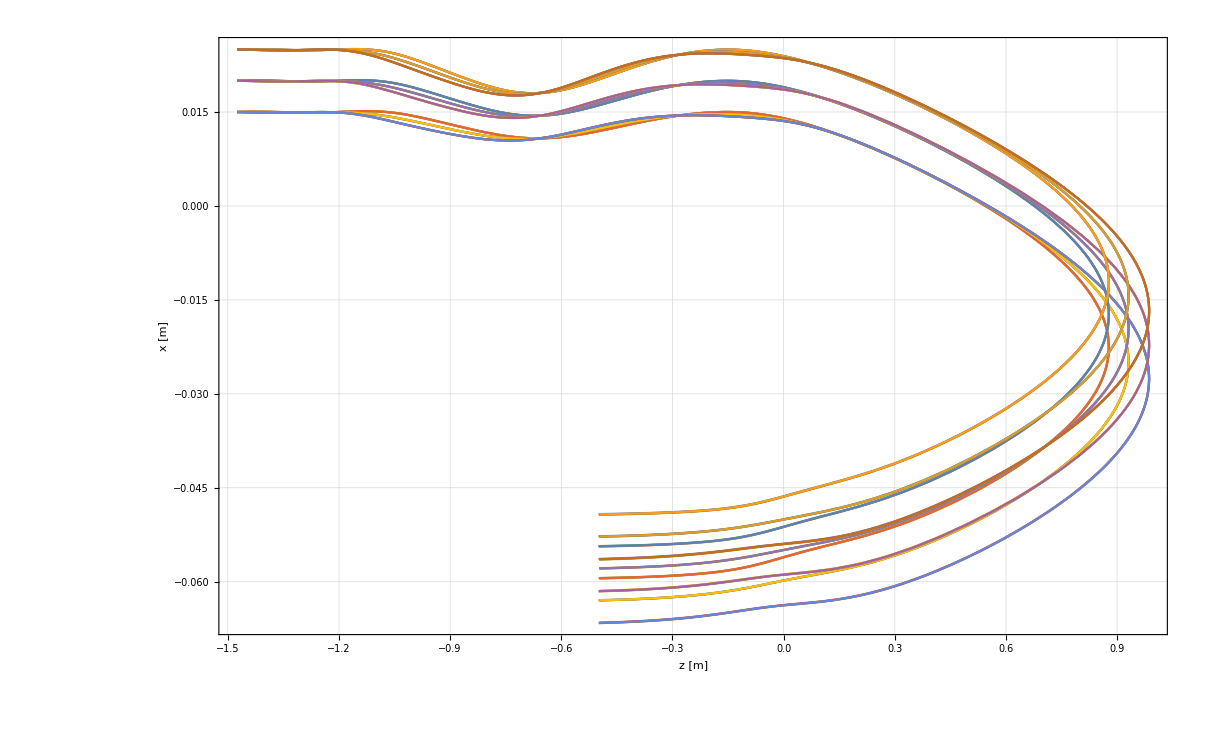

```mathematica
ListLinePlot[
Flatten[
Table[
Table[
Table[
Table[
Transpose[{testtraj[[line,theta,ekin,phi,All,12]],testtraj[[line,theta,ekin,phi,All,10]]}],
{phi,1,PhiMax/PhiStep+1}],
{ekin,{Ekin}}],
{theta,{Theta}}],
{line,1,horilines*vertilines}],3],GridLines->Automatic,Frame->True,FrameLabel->{{"x [m]",None},{"z [m]","GuidC. of Trajectories"}},FrameStyle->20,PlotRange->All
]
```

### YZ plot along guidcenter

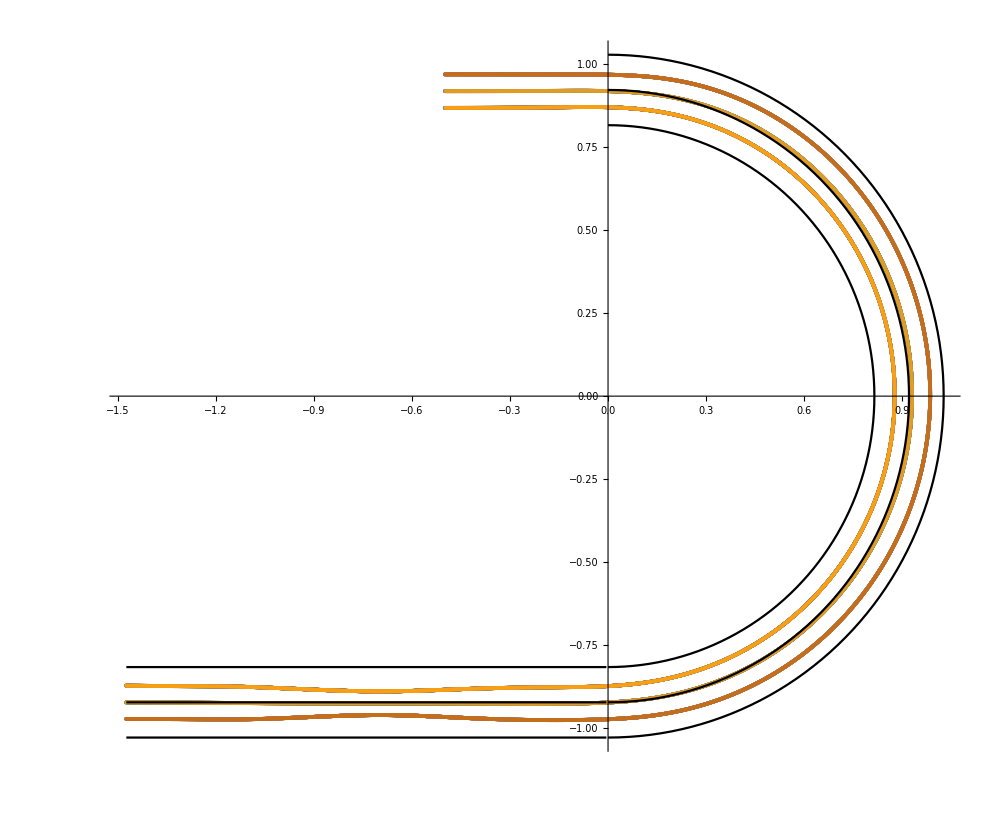

```mathematica
Show[
ListPlot[
Flatten[
Table[
Table[
Table[
Table[
Transpose[{testtraj[[line,theta,ekin,phi,All,12]],-testtraj[[line,theta,ekin,phi,All,11]]}],
{phi,1,PhiMax/PhiStep+1}],
{ekin,{Ekin}}],
{theta,{Theta}}],
{line,1,horilines*vertilines}],3],AspectRatio->Automatic
],
ListLinePlot[
{
Table[{(R1-0.15/Sqrt[2])*Sin[th],-(R1-0.15/Sqrt[2])*Cos[th]},{th,0,Pi,Pi/100}],
Table[{(R1+0.15/Sqrt[2])*Sin[th],-(R1+0.15/Sqrt[2])*Cos[th]},{th,0,Pi,Pi/100}],
Table[{(R1)*Sin[th],-(R1)*Cos[th]},{th,0,Pi,Pi/100}],
Table[{z,-R1},{z,-1.475,0,0.01}],
Table[{z,-R1-0.15/Sqrt[2]},{z,-1.475,0,0.01}],
Table[{z,-R1+0.15/Sqrt[2]},{z,-1.475,0,0.01}]
},PlotStyle->Black],PlotRange->{{-1.3,1.1},{1,-1}},ImageSize->1000
]
```

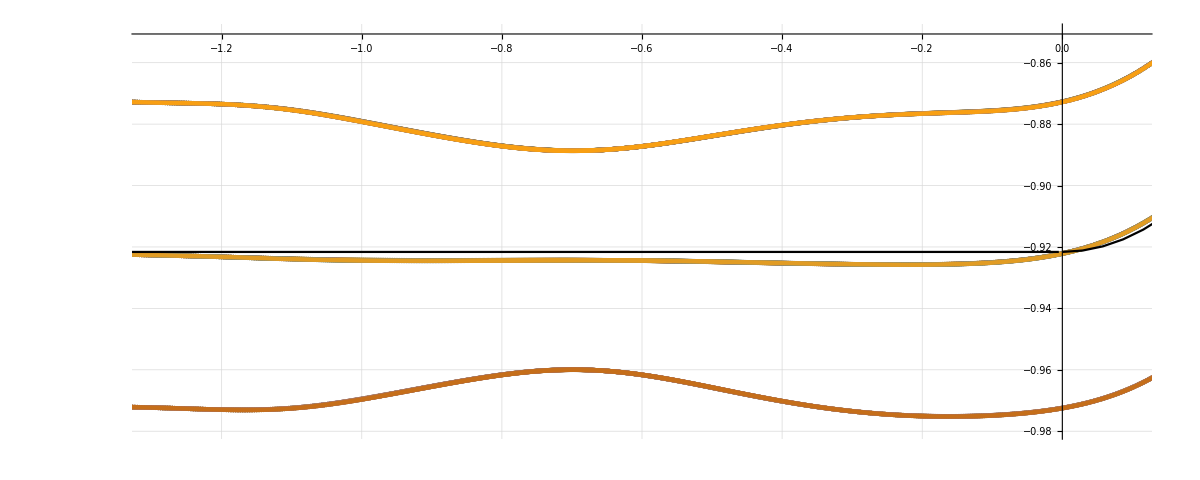

```mathematica
Show[
ListPlot[
Flatten[
Table[
Table[
Table[
Table[
Transpose[{testtraj[[line,theta,ekin,phi,All,12]],-testtraj[[line,theta,ekin,phi,All,11]]}],
{phi,1,PhiMax/PhiStep+1}],
{ekin,{Ekin}}],
{theta,{Theta}}],
{line,1,horilines*vertilines}],3],AspectRatio->Automatic,PlotRange->{{-1.3,0.1},{-0.98,-0.85}}
],
ListLinePlot[
{
Table[{(R1-0.15/Sqrt[2])*Sin[th],-(R1-0.15/Sqrt[2])*Cos[th]},{th,0,Pi,Pi/100}],
Table[{(R1+0.15/Sqrt[2])*Sin[th],-(R1+0.15/Sqrt[2])*Cos[th]},{th,0,Pi,Pi/100}],
Table[{(R1)*Sin[th],-(R1)*Cos[th]},{th,0,Pi,Pi/100}],
Table[{z,-R1},{z,-1.475,0,0.01}]
},PlotStyle->Black,PlotRange->{{-1.3,0.1},{-0.98,-0.85}}],ImageSize->1200,GridLines->Automatic
]
```

### Guiding Center separated calculation for testing, mathematica calc overlaps well with read-in data

```mathematica
me=9.109*10^-31;e=1.602*10^-19;c=299792458;
```

```mathematica
gamma[v_]:=1/Sqrt[1-v^2/c^2]
```

```mathematica
GuidingCenter[x_List,v_List,B_List]:=Module[
{V=Norm[v],Babs=Norm[B],gyrationR,ParaVtoB,NormalVtoB},
{
{"ParaVtoB",ParaVtoB=(v.B)/Babs},
{"NormalVtoB",NormalVtoB=Sqrt[V^2-ParaVtoB^2]},
{"gyrationR",gyrationR=gamma[V]*me*NormalVtoB/e/Babs},
x-Normalize[Cross[v,B]]*gyrationR
}]
```

```mathematica
Mean[Norm[{#[[1]],#[[2]],#[[3]]}]&/@testtraj[[8,2,2,1,All,4;;6]]]
```

2.74137×10^8

```mathematica
GuidingCenter[{0,0,0},{10^8,0,0},{0,0,0.2}]
```

{{ParaVtoB,0.},{NormalVtoB,1.×10^8},{gyrationR,0.00301573},{0.,0.00301573,0.}}

```mathematica
testtraj[[8,2,2,1,-1]]
```

{-0.0459825,-0.92223,-0.498,-4.71921×10^7,-7.94469×10^7,-2.58094×10^8,-0.000163823,-0.0000323334,-0.163144,-0.0528186,-0.918189,-0.497994,-0.000187114,-0.000021854,-0.163136,751483.,7.34293×10^-14,1.9015×10^-8,179.941,19.66}

```mathematica
((GuidingCenter[{#[[1]],#[[2]],#[[3]]},{#[[4]],#[[5]],#[[6]]},{#[[7]],#[[8]],#[[9]]}][[3,2]])&/@testtraj[[3,2,2,1,-2;;-1]])
```

{0.00797687,0.00797837}

```mathematica
Graphics3D[
{
Table[
Table[
Table[
Table[
{Thickness[0.005],Point[#]}&@testtraj[[line,theta,Ekin,phi,All,1;;3]],
{phi,{1}}],
{Ekin,{2}}],
{theta,{2}}],
{line,{3}}],
Table[
Table[
Table[
Table[
{Thickness[0.005],Red,Point[#]}&@((GuidingCenter[{#[[1]],#[[2]],#[[3]]},{#[[4]],#[[5]],#[[6]]},{#[[7]],#[[8]],#[[9]]}][[4]])&/@testtraj[[line,theta,Ekin,phi,All]]),
{phi,{1}}],
{Ekin,{2}}],
{theta,{2}}],
{line,{3}}]
},
Axes->True,AxesLabel->{"x","y","z"},ImageSize->900,ViewVertical->{0,-1,0},ViewPoint->{2,0,-1}]
```

-Graphics3D-

Inlet

```mathematica
WhichLine=(horilines*vertilines+1)/2;
```

### B along data points (interpolated) of Gc vs traj for examplary trajectory

```mathematica
InletTrajData=Table[Flatten[Position[testtraj[[line,Theta,Ekin,1]],{_,_?(#>0.&),_?(#<=0.&),_,_,_,_,_,_,_,_,_,_,_,_,_,_,_,_,_}],1],{line,1,horilines*vertilines}];
```

```mathematica
InletTrajData//Dimensions
```

{9}

```mathematica
LineStart=testtraj[[All,Theta,Ekin,1,1,3]]
```

{-1.475,-1.475,-1.475,-1.475,-1.475,-1.475,-1.475,-1.475,-1.475}

```mathematica
TrajBInletInter=Table[Interpolation[{#[[3]],1000*{#[[7]],#[[8]],#[[9]]}}&/@testtraj[[line,Theta,Ekin,1,InletTrajData[[line]]]]],{line,1,horilines*vertilines}];
GuidBInletInter=Table[Interpolation[{#[[3]],1000*{#[[13]],#[[14]],#[[15]]}}&/@testtraj[[line,Theta,Ekin,1,InletTrajData[[line]]]]],{line,1,horilines*vertilines}];
```

```mathematica
PlotLabels={"Bx [mT]","By [mT]","Bz [mT]"};
ResPlotLabels={"ΔBx [mT]","ΔBy [mT]","ΔBz [mT]"};
```

```mathematica
PlotRanges={{-8,8},{-15,15},{2.5,400}};
ResRanges={{-1,1},{-1,1},{-3,3}};
```

```mathematica
BInletPlots=Table[
Table[
Plot[
{
TrajBInletInter[[line]][z][[comp]],
GuidBInletInter[[line]][z][[comp]]
},{z,LineStart[[line]],0},
PlotRangePadding->None,ImagePadding->{{80,1},{1,50}},ImageSize->480,Frame->True,FrameLabel->{{PlotLabels[[comp]],None},{None,PlotLabels[[comp]]<>" along z for examplary line Inlet"}},GridLines->Automatic,FrameStyle->Directive[Thick,20],PlotRange->PlotRanges[[comp]],PlotStyle->Thick],
{comp,1,3,1}],
{line,1,horilines*vertilines}];
```

### Residuals

```mathematica
BInletRes=Table[
Table[
Plot[TrajBInletInter[[line]][z][[comp]]-GuidBInletInter[[line]][z][[comp]],{z,LineStart[[line]],0},
PlotRangePadding->None,ImagePadding->{{80,1},{65,0}},ImageSize->480,Frame->True,FrameLabel->{{"ΔB [mT]",None},{"z [m]",None}},GridLines->Automatic,FrameStyle->Directive[Thick,20],AspectRatio->1/4,PlotRange->ResRanges[[comp]]],
{comp,1,3}],
{line,1,horilines*vertilines}];
```

### plot

```mathematica
InletPlotAll=
Table[
Table[
Column[
{
BInletPlots[[line,comp]],
BInletRes[[line,comp]]
},Spacings->0
],
{comp,3,1,-1}
],
{line,1,horilines*vertilines}];
```

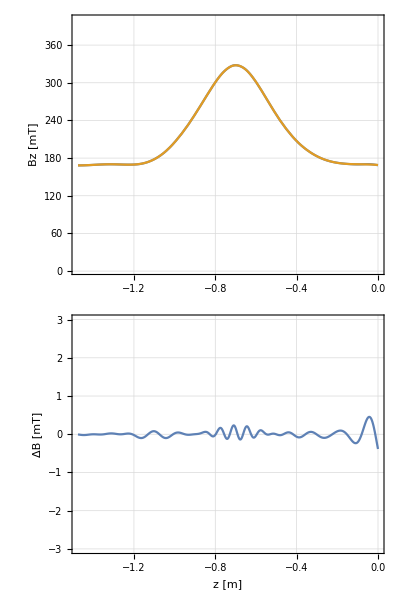
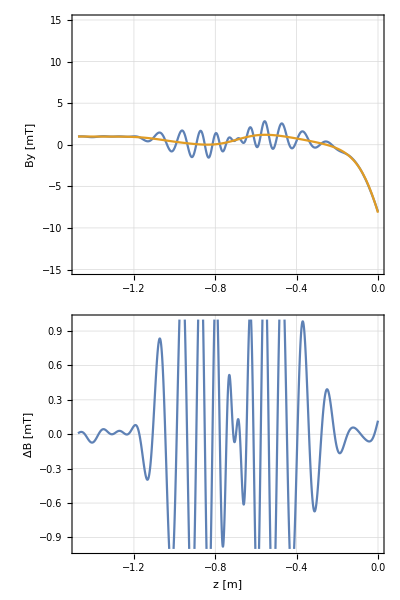
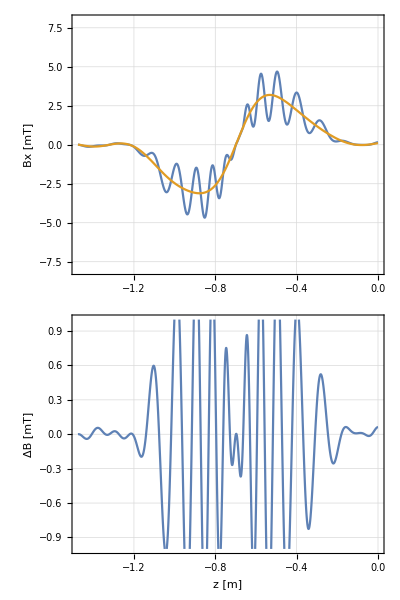

```mathematica
Row[InletPlotAll[[2]]]
```

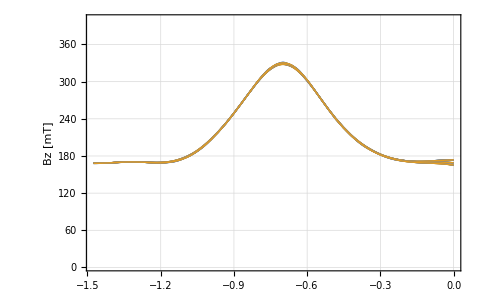

```mathematica
Show[Table[BInletPlots[[line,3]],{line,1,horilines*vertilines}]]
```

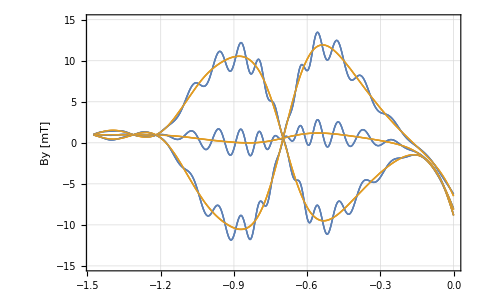

```mathematica
Show[Table[BInletPlots[[line,2]],{line,1,horilines*vertilines}]]
```

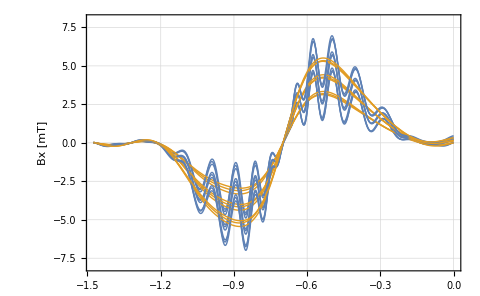

```mathematica
Show[Table[BInletPlots[[line,1]],{line,1,horilines*vertilines}]]
```

Field comparison in RxB

### Data + Angle

```mathematica
RxBTrajData=Table[Flatten[Position[testtraj[[line,Theta,Ekin,1]],{_,_,_?(#>=0.&),_,_,_,_,_,_,_,_,_,_,_,_,_,_,_,_,_}],1],{line,1,horilines*vertilines}];
RxBGuidData=Table[Flatten[Position[testtraj[[line,Theta,Ekin,1]],{_,_,_,_,_,_,_,_,_,_,_,_?(#>=0.&),_,_,_,_,_,_,_,_}],1],{line,1,horilines*vertilines}];
```

```mathematica
AngleCalc[yz_]:=If[
yz[[1]]>0,
ArcTan[yz[[2]]/yz[[1]]],
ArcTan[-yz[[1]]/yz[[2]]]+Pi/2
]
```

```mathematica
RxBTrajAngle=Table[Table[AngleCalc[testtraj[[line,Theta,Ekin,1,ii,2;;3]]],{ii,RxBTrajData[[line]]}],{line,1,horilines*vertilines}];
RxBGuidAngle=Table[Table[AngleCalc[testtraj[[line,Theta,Ekin,1,ii,11;;12]]],{ii,RxBGuidData[[line]]}],{line,1,horilines*vertilines}];
```

```mathematica
RxBTrajInter=Table[Interpolation[Transpose[{RxBTrajAngle[[line]]/Pi*180,1000*testtraj[[line,Theta,Ekin,1,RxBTrajData[[line]],7;;9]]}]],{line,1,horilines*vertilines}];
RxBGuidInter=Table[Interpolation[Transpose[{RxBGuidAngle[[line]]/Pi*180,1000*testtraj[[line,Theta,Ekin,1,RxBGuidData[[line]],13;;15]]}]],{line,1,horilines*vertilines}];
```

### tangential field (projected in YZ plane)

```mathematica
TangVectorRxBTraj=Table[{-Sin[#],Cos[#]}&/@RxBTrajAngle[[line]],{line,1,horilines*vertilines}];
TangVectorRxBGuid=Table[{-Sin[#],Cos[#]}&/@RxBGuidAngle[[line]],{line,1,horilines*vertilines}];
```

```mathematica
RxBTrajTanB=
Table[
Transpose[
{
RxBTrajAngle[[line]]/Pi*180.,
Table[
1000*testtraj[[line,Theta,Ekin,1,ii+RxBTrajData[[line,1]]-1,8;;9]].TangVectorRxBTraj[[line,ii]],{ii,1,Length[RxBTrajAngle[[line]]]}]
}
],{line,1,horilines*vertilines}];
RxBGuidTanB=
Table[
Transpose[
{
RxBGuidAngle[[line]]/Pi*180.,
Table[
1000*testtraj[[line,Theta,Ekin,1,ii+RxBTrajData[[line,1]]-1,14;;15]].TangVectorRxBGuid[[line,ii]],{ii,1,Length[RxBGuidAngle[[line]]]}]
}
],{line,1,horilines*vertilines}];
```

```mathematica
RxBTrajTanBInter=Table[Interpolation[RxBTrajTanB[[line]]],{line,1,horilines*vertilines}];
RxBGuidTanBInter=Table[Interpolation[RxBGuidTanB[[line]]],{line,1,horilines*vertilines}];
```

```mathematica
RxBTanBPlot=Table[
ListLinePlot[{RxBTrajTanB[[line]],RxBGuidTanB[[line]]},PlotRangePadding->None,ImagePadding->{{0,1},{1,50}},ImageSize->400,Frame->True,FrameLabel->{{None,None},{None,"B_tang [mT] of trajectory in RxB"}},GridLines->Automatic,FrameStyle->Directive[Thick,20],PlotRange->{2.5,400},PlotStyle->Thick],{line,1,horilines*vertilines}];
```

```mathematica
RxBTanBRes=Table[
Plot[
RxBTrajTanBInter[[line]][th]-RxBGuidTanBInter[[line]][th]
,{th,0.2,180},PlotRangePadding->None,ImagePadding->{{0,1},{65,0}},ImageSize->400,Frame->True,FrameLabel->{{None,None},{"Angle [°]",None}},GridLines->Automatic,FrameStyle->Directive[Thick,20],AspectRatio->1/4,PlotRange->{-1,1}
],{line,1,horilines*vertilines}];
```

InterpolatingFunction::dmval: Input value {0.203673} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

### Plot

```mathematica
RxBTangPlotAll=Table[Column[{RxBTanBPlot[[line]],RxBTanBRes[[line]]},Spacings->0],{line,1,horilines*vertilines}];
```

### abs

```mathematica
RxBAbsPlot=Table[Plot[
{
Norm[RxBTrajInter[[line]][th]],
Norm[RxBGuidInter[[line]][th]]
},{th,0.2,180},PlotRangePadding->None,ImagePadding->{{75,10},{1,50}},ImageSize->400,Frame->True,FrameLabel->{{"B [mT]",None},{None,"B along RxB"}},GridLines->Automatic,FrameStyle->15,PlotRange->{Automatic,{25,350}}
],{line,1,horilines*vertilines}];
```

InterpolatingFunction::dmval: Input value {0.203673} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

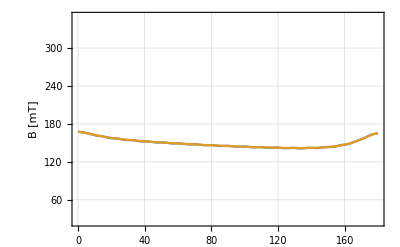

```mathematica
RxBAbsPlot[[1]]
```

```mathematica
RxBAbsRes=Table[Plot[
Norm[RxBTrajInter[[line]][th]]-Norm[RxBGuidInter[[line]][th]]
,{th,0.2,180},PlotRangePadding->None,ImagePadding->{{75,10},{50,0}},ImageSize->400,Frame->True,FrameLabel->{{"Δ"<>"B [mT]",None},{"Angle [°]",None}},GridLines->Automatic,FrameStyle->15,AspectRatio->1/4,PlotRange->All
],{line,1,horilines*vertilines}];
```

InterpolatingFunction::dmval: Input value {0.203673} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

### abs plot

```mathematica
(*Column[{RxBAbsPlot,RxBAbsRes},Spacings->0]*)
```

### Bx

```mathematica
RxBBxPlot=Table[Plot[
{
RxBTrajInter[[line]][th][[1]],
RxBGuidInter[[line]][th][[1]]
},{th,0.2,180},PlotRangePadding->None,ImagePadding->{{75,10},{1,50}},ImageSize->400,Frame->True,FrameLabel->{{"Bx [mT]",None},{None,"Bx along RxB for examplary line"}},GridLines->Automatic,FrameStyle->15,PlotRange->{-3,3}
],{line,1,horilines*vertilines}];
```

InterpolatingFunction::dmval: Input value {0.203673} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
RxBBxRes=Table[Plot[
RxBTrajInter[[line]][th][[1]]-RxBGuidInter[[line]][th][[1]]
,{th,0.2,180},PlotRangePadding->None,ImagePadding->{{75,10},{50,0}},ImageSize->400,Frame->True,FrameLabel->{{"Δ"<>"Bx [mT]",None},{"Angle [°]",None}},GridLines->Automatic,FrameStyle->15,AspectRatio->1/4,PlotRange->All
],{line,1,horilines*vertilines}];
```

InterpolatingFunction::dmval: Input value {0.203673} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

### Bx plot

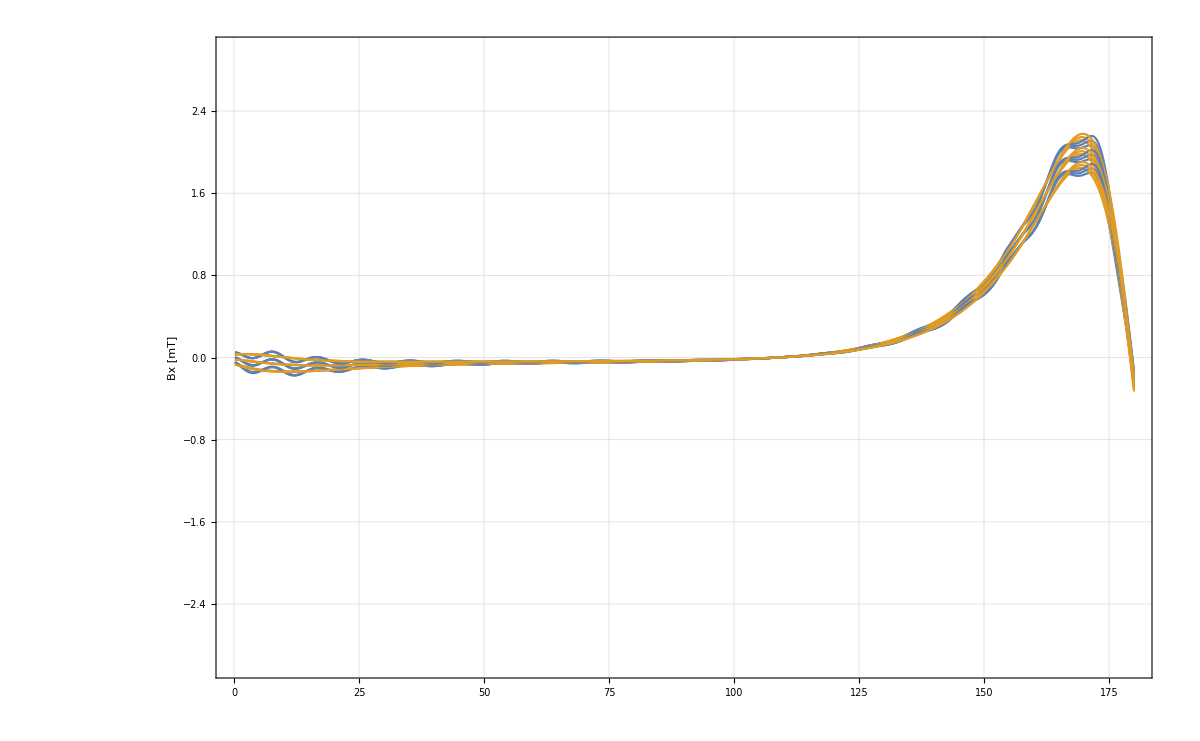

```mathematica
Show[Table[RxBBxPlot[[line]],{line,1,horilines*vertilines}],ImageSize->1200]
```

### By

```mathematica
RxBByPlot=Table[Plot[
{
RxBTrajInter[[line]][th][[2]],
RxBGuidInter[[line]][th][[2]]
},{th,0.2,180},PlotRangePadding->None,ImagePadding->{{75,10},{1,50}},ImageSize->400,Frame->True,FrameLabel->{{"By [mT]",None},{None,"By along RxB for examplary line"}},GridLines->Automatic,FrameStyle->15,PlotRange->{-160,0}
],{line,1,horilines*vertilines}];
```

InterpolatingFunction::dmval: Input value {0.203673} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
RxBByRes=Table[Plot[
RxBTrajInter[[line]][th][[2]]-RxBGuidInter[[line]][th][[2]]
,{th,0.2,180},PlotRangePadding->None,ImagePadding->{{75,10},{50,0}},ImageSize->400,Frame->True,FrameLabel->{{"Δ"<>"By [mT]",None},{"Angle [°]",None}},GridLines->Automatic,FrameStyle->15,AspectRatio->1/4,PlotRange->All
],{line,1,horilines*vertilines}];
```

InterpolatingFunction::dmval: Input value {0.203673} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

### By plot

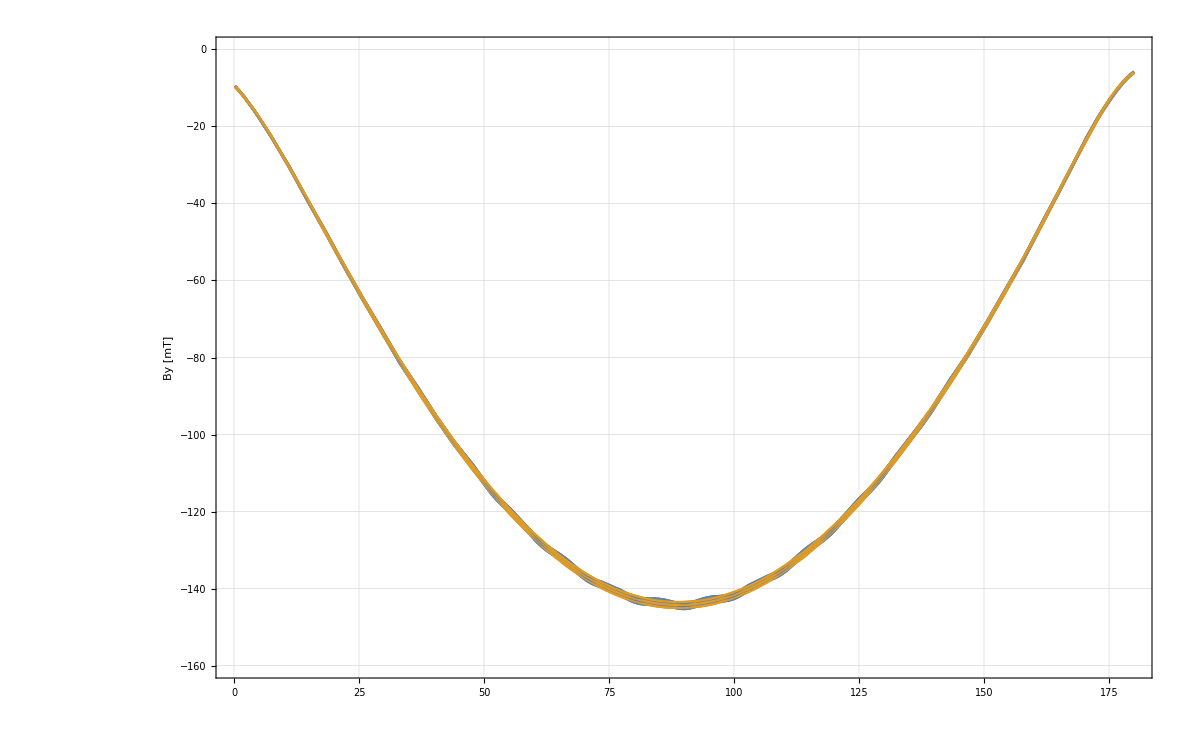

```mathematica
Show[Table[RxBByPlot[[line]],{line,1,horilines*vertilines}],ImageSize->1200]
```

### Bz

```mathematica
RxBBzPlot=Table[Plot[
{
RxBTrajInter[[line]][th][[3]],
RxBGuidInter[[line]][th][[3]]
},{th,0.2,180},PlotRangePadding->None,ImagePadding->{{75,10},{1,50}},ImageSize->400,Frame->True,FrameLabel->{{"Bz [mT]",None},{None,"Bz along RxB for examplary line"}},GridLines->Automatic,FrameStyle->15,PlotRange->{-185,185}
],{line,1,horilines*vertilines}];
```

InterpolatingFunction::dmval: Input value {0.203673} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
RxBBzRes=Table[Plot[
RxBTrajInter[[line]][th][[3]]-RxBGuidInter[[line]][th][[3]]
,{th,0.2,180},PlotRangePadding->None,ImagePadding->{{75,10},{50,0}},ImageSize->400,Frame->True,FrameLabel->{{"Δ"<>"By [mT]",None},{"Angle [°]",None}},GridLines->Automatic,FrameStyle->15,AspectRatio->1/4,PlotRange->All
],{line,1,horilines*vertilines}];
```

InterpolatingFunction::dmval: Input value {0.203673} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

### Bz plot

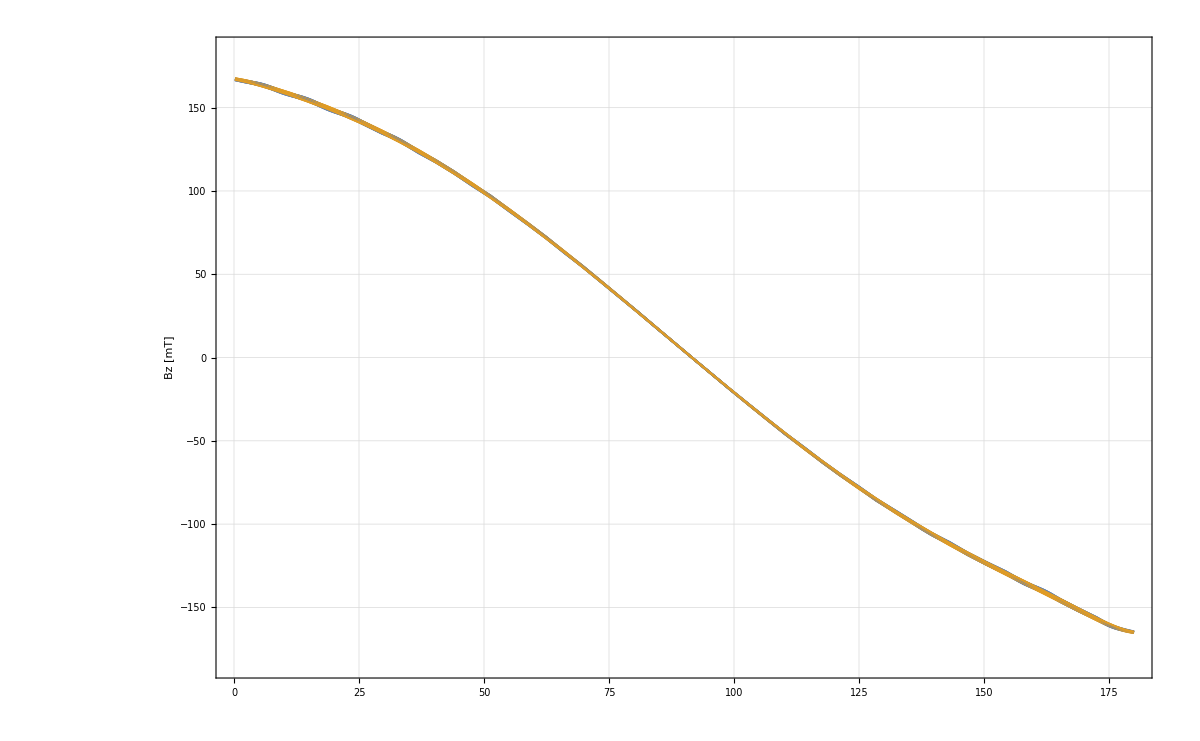

```mathematica
Show[Table[RxBBzPlot[[line]],{line,1,horilines*vertilines}],ImageSize->1200]
```

Outlet

### Field plots

```mathematica
OutletTrajData=Table[Flatten[Position[testtraj[[line,Theta,Ekin,1]],{_,_?(#<0.&),_?(#<=0.&),_,_,_,_,_,_,_,_,_,_,_,_,_,_,_,_,_}],1],{line,1,horilines*vertilines}];
```

```mathematica
OutletTrajData//Length
```

9

```mathematica
TrajBOutletInter=Table[Interpolation[{-#[[3]],1000*{#[[7]],#[[8]],-#[[9]]}}&/@testtraj[[line,Theta,Ekin,1,OutletTrajData[[line]]]]],{line,1,horilines*vertilines}];
GuidBOutletInter=Table[Interpolation[{-#[[3]],1000*{#[[13]],#[[14]],-#[[15]]}}&/@testtraj[[line,Theta,Ekin,1,OutletTrajData[[line]]]]],{line,1,horilines*vertilines}];
```

```mathematica
PlotLabels={"Bx [mT]","By [mT]","Bz [mT]"};
```

```mathematica
PlotRanges={{-4,2},{-14,14},{2.5,400}}
```

{{-4,2},{-14,14},{2.5,400}}

```mathematica
BOutletPlots=Table[
Table[
Plot[
{
TrajBOutletInter[[line]][z][[comp]],
GuidBOutletInter[[line]][z][[comp]]
},{z,0.005,0.495},
PlotRangePadding->None,ImagePadding->{{0,1},{1,50}},ImageSize->400,Frame->True,FrameLabel->{{None,None},{None,PlotLabels[[comp]]<>" along z in Outlet"}},GridLines->Automatic,FrameStyle->Directive[Thick,20],PlotRange->PlotRanges[[comp]],PlotStyle->Thick],
{comp,1,3,1}],{line,1,horilines*vertilines}];
```

### Residuals

```mathematica
BOutletRes=Table[Table[
Plot[TrajBOutletInter[[line]][z][[comp]]-GuidBOutletInter[[line]][z][[comp]],{z,0.005,0.495},
PlotRangePadding->None,ImagePadding->{{0,1},{65,0}},ImageSize->400,Frame->True,FrameLabel->{{"Δ"<>PlotLabels[[comp]],None},{"-z [m]",None}},GridLines->Automatic,FrameStyle->Directive[Thick,20],AspectRatio->1/4,PlotRange->ResRanges[[comp]]],
{comp,1,3}],{line,1,horilines*vertilines}];
```

### plot

```mathematica
OutletPlotAll=Table[Table[
Column[
{
BOutletPlots[[line,comp]],
BOutletRes[[line,comp]]
},Spacings->0
],
{comp,3,1,-1}
],{line,1,horilines*vertilines}];
```

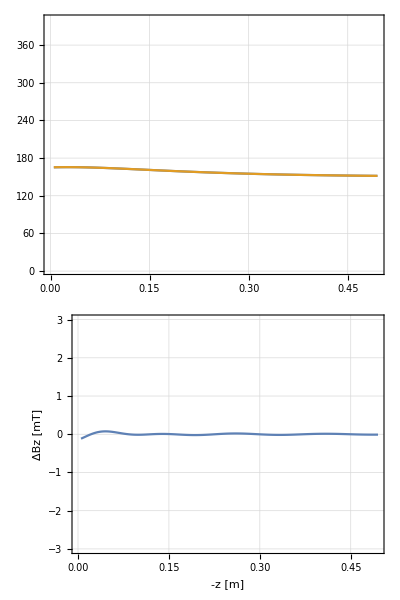
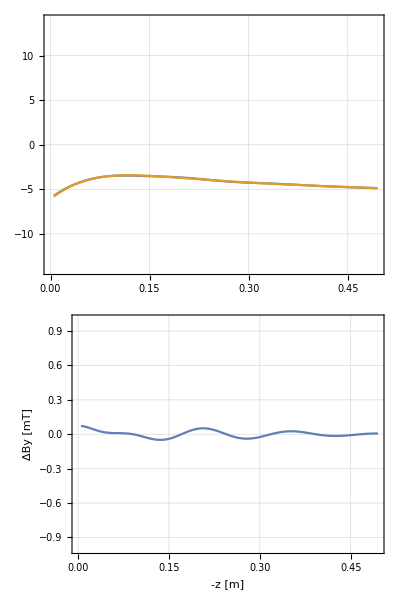
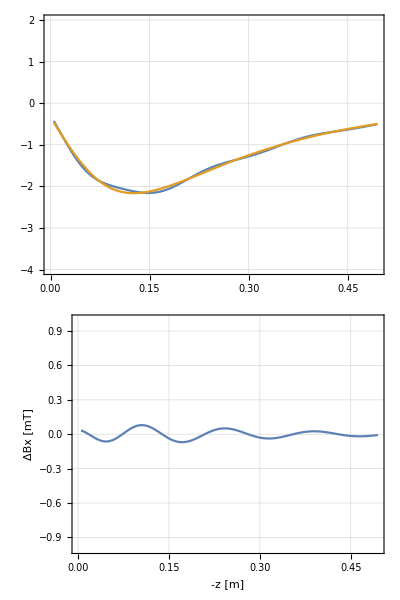

```mathematica
Row[OutletPlotAll[[1]]]
```

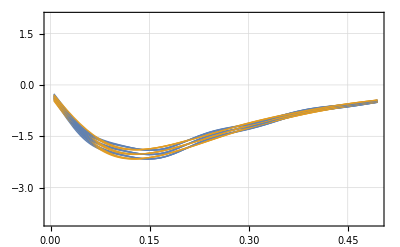

```mathematica
Show[Table[BOutletPlots[[line,1]],{line,1,horilines*vertilines}]]
```

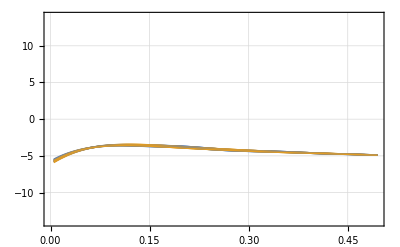

```mathematica
Show[Table[BOutletPlots[[line,2]],{line,1,horilines*vertilines}]]
```

Plot along the full NoMoS area

```mathematica
horilines*vertilines
```

9

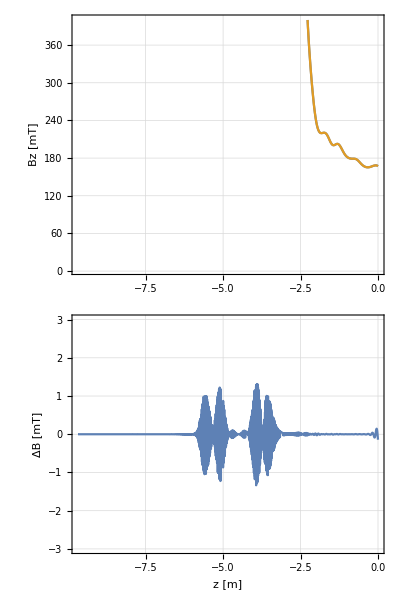
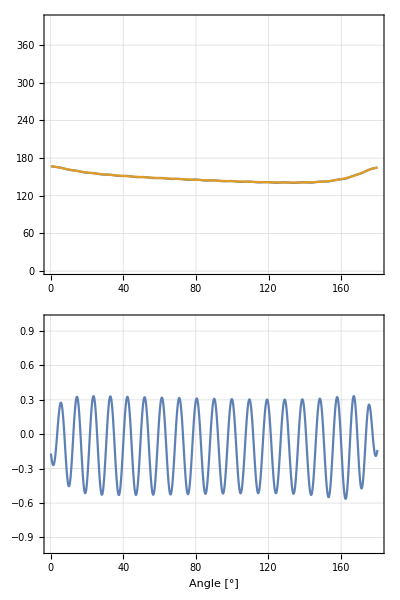
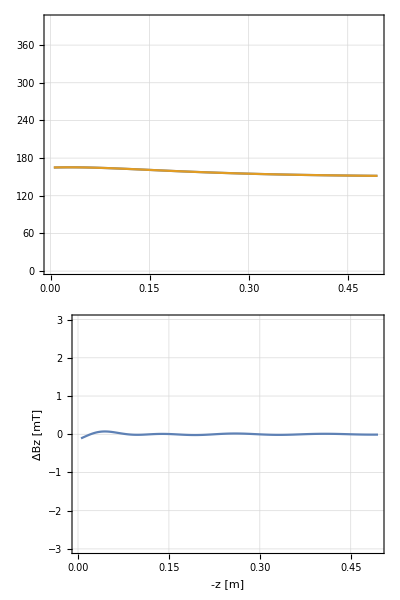

```mathematica
miau=Row[
{
InletPlotAll[[5,1]],
RxBTangPlotAll[[5]],
OutletPlotAll[[5,1]]
},ImageSize->2*10^3
]
```

```mathematica
(*Export["/home/dmoser/Dropbox/PhD/Balongtraj.png",miau,ImageResolution->500]*)
```

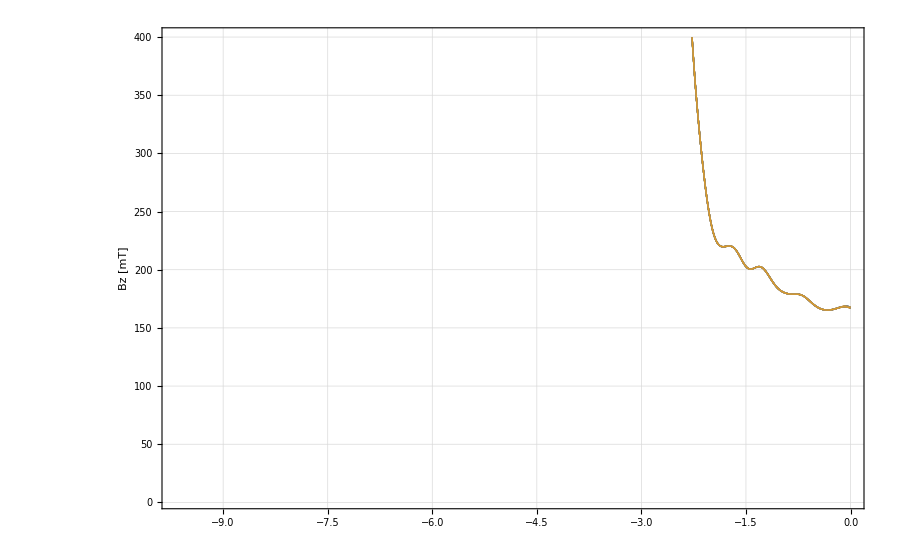

```mathematica
Show[Table[BInletPlots[[line,3]],{line,1,horilines*vertilines}],ImageSize->900]
```

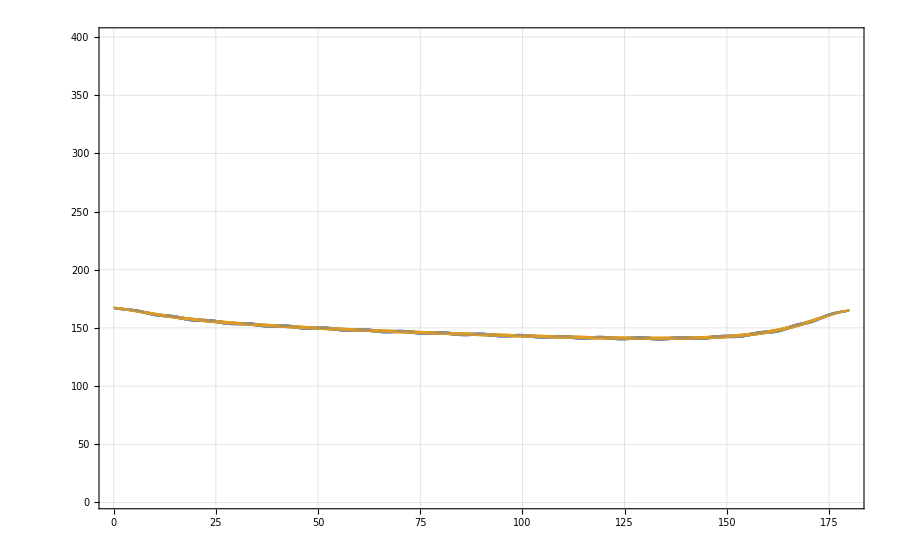

```mathematica
Show[Table[RxBTanBPlot[[line]],{line,1,horilines*vertilines}],ImageSize->900]
```

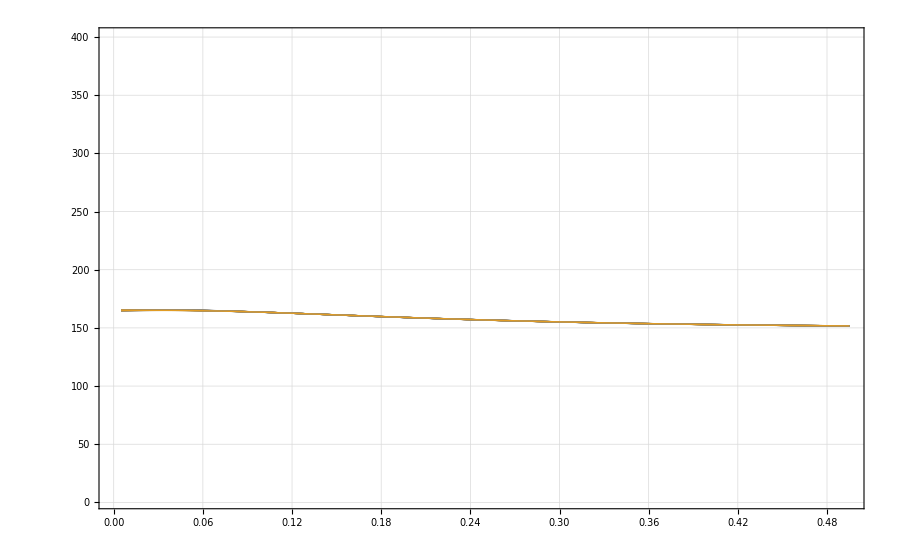

```mathematica
Show[Table[BOutletPlots[[line,3]],{line,1,horilines*vertilines}],ImageSize->900]
```

Field vectors of traj/GC at entrance/exit of RxB

### YZ RxB Start

```mathematica
RxBStartData=Table[
testtraj[[line,Theta,Ekin,1,InletTrajData[[line,-1]]]],{line,1,horilines*vertilines}];
```

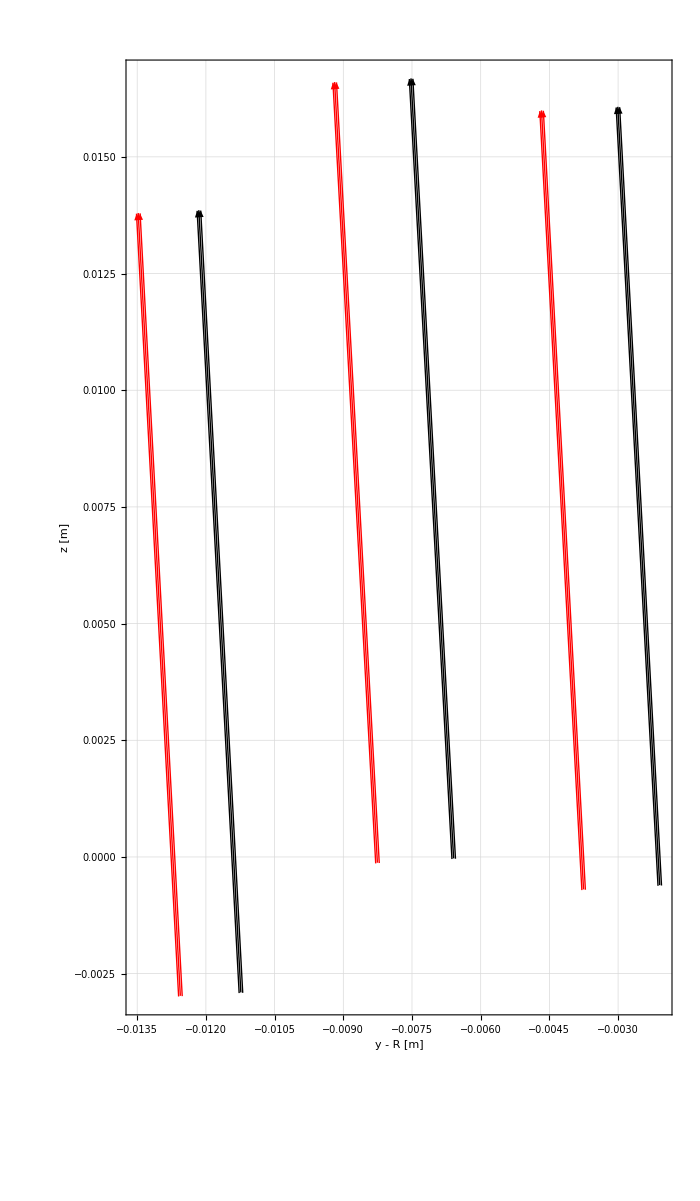

```mathematica
StartVector=Show[Table[
Graphics[
{
Black,
Arrow[
{
{RxBStartData[[i,2]]-R1,RxBStartData[[i,3]]},
{RxBStartData[[i,2]]-R1,RxBStartData[[i,3]]}+0.1*RxBStartData[[i,8;;9]]
}
]
}],{i,1,horilines*vertilines}],
Table[
Graphics[
{
Red,
Arrow[
{
{RxBStartData[[i,11]]-R1,RxBStartData[[i,12]]},
{RxBStartData[[i,11]]-R1,RxBStartData[[i,12]]}+0.1*RxBStartData[[i,14;;15]]
}
]
}],{i,1,horilines*vertilines}],Axes->True,Frame->True,GridLines->Automatic,FrameLabel->{{"z [m]",None},{"y - R [m]","Byz Vector at RxBStart"}},FrameStyle->20,ImageSize->700]
```

```mathematica
StartAngles=Table[ArcTan[-RxBStartData[[i,8]]/RxBStartData[[i,9]]]/Pi*180.,{i,1,horilines*vertilines}]
```

{3.13377,3.18685,3.13733,3.13429,3.1874,3.13787,3.13319,3.18632,3.13677}

```mathematica
StartAnglesGuid=Table[ArcTan[-RxBStartData[[i,14]]/RxBStartData[[i,15]]]/Pi*180.,{i,1,horilines*vertilines}]
```

{3.13916,3.19513,3.14659,3.14018,3.19616,3.1476,3.13959,3.19554,3.14697}

### XZ StartRxB

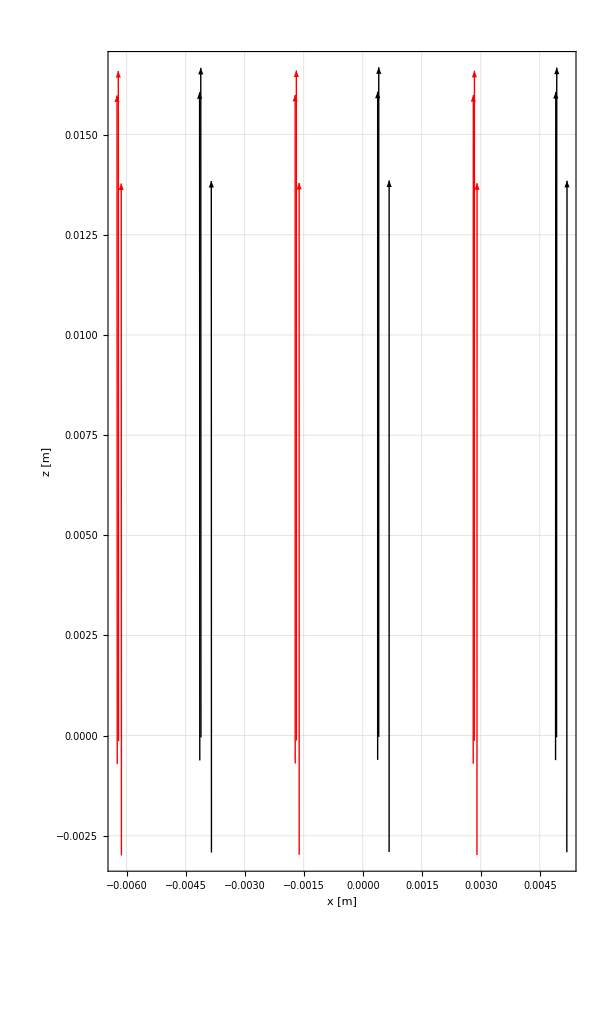

```mathematica
StartVector=Show[Table[
Graphics[
{
Black,
Arrow[
{
{RxBStartData[[i,1]],RxBStartData[[i,3]]},
{RxBStartData[[i,1]],RxBStartData[[i,3]]}+0.1*RxBStartData[[i,{7,9}]]
}
]
}],{i,1,horilines*vertilines}],
Table[
Graphics[
{
Red,
Arrow[
{
{RxBStartData[[i,10]],RxBStartData[[i,12]]},
{RxBStartData[[i,10]],RxBStartData[[i,12]]}+0.1*RxBStartData[[i,{13,15}]]
}
]
}],{i,1,horilines*vertilines}],Axes->True,Frame->True,GridLines->Automatic,FrameLabel->{{"z [m]",None},{"x [m]","Bxz Vector at RxBStart"}},FrameStyle->20,ImageSize->600]
```

### YZ RxB End

```mathematica
RxBEndData=Table[
testtraj[[line,Theta,Ekin,1,OutletTrajData[[line,1]]]],{line,1,horilines*vertilines}];
```

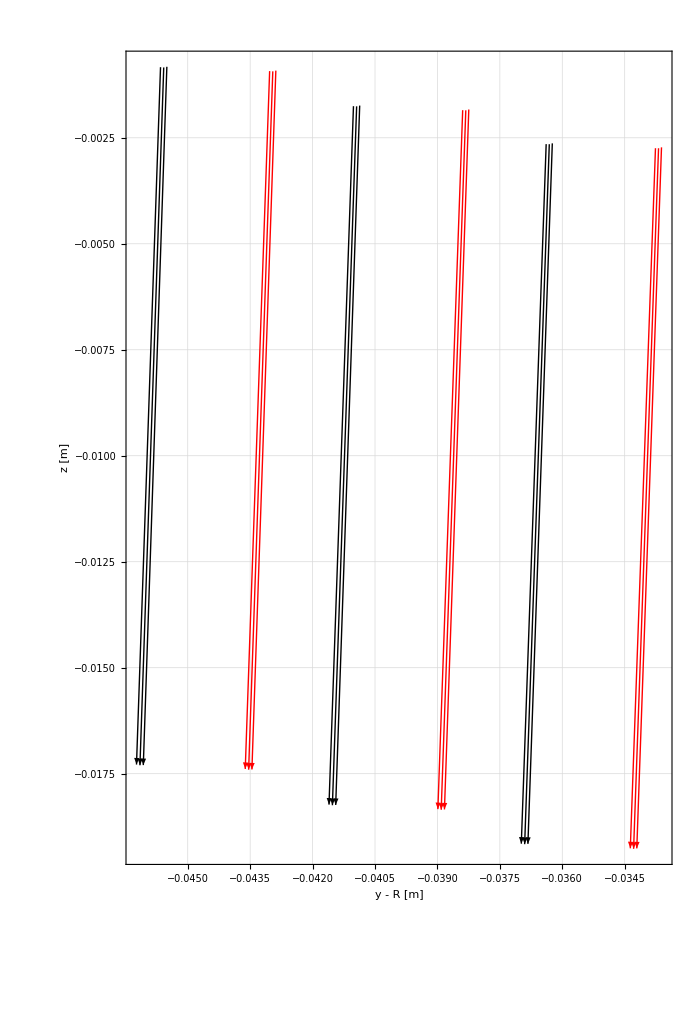

```mathematica
EndVector=Show[Table[
Graphics[
{
Black,
Arrow[
{
{RxBEndData[[i,2]]+R1,RxBEndData[[i,3]]},
{RxBEndData[[i,2]]+R1,RxBEndData[[i,3]]}+0.1*RxBEndData[[i,8;;9]]
}
]
}],{i,1,horilines*vertilines}],
Table[
Graphics[
{
Red,
Arrow[
{
{RxBEndData[[i,11]]+R1,RxBEndData[[i,12]]},
{RxBEndData[[i,11]]+R1,RxBEndData[[i,12]]}+0.1*RxBEndData[[i,14;;15]]
}
]
}],{i,1,horilines*vertilines}],
Axes->True,Frame->True,GridLines->Automatic,FrameLabel->{{"z [m]",None},{"y - R [m]","Byz Vector at RxBEnd"}},FrameStyle->20,ImageSize->700]
```

```mathematica
EndAngles=Table[ArcTan[-RxBEndData[[i,8]]/RxBEndData[[i,9]]]/Pi*180.,{i,1,horilines*vertilines}]
```

{-2.03197,-2.00217,-1.96728,-2.05325,-2.02365,-1.98902,-2.07348,-2.04406,-2.00966}

```mathematica
EndAnglesGuid=Table[ArcTan[-RxBEndData[[i,14]]/RxBEndData[[i,15]]]/Pi*180.,{i,1,horilines*vertilines}]
```

{-2.05589,-2.02892,-1.99694,-2.07703,-2.05025,-2.0185,-2.09715,-2.07053,-2.03899}

### XZ vector at RxBEnd

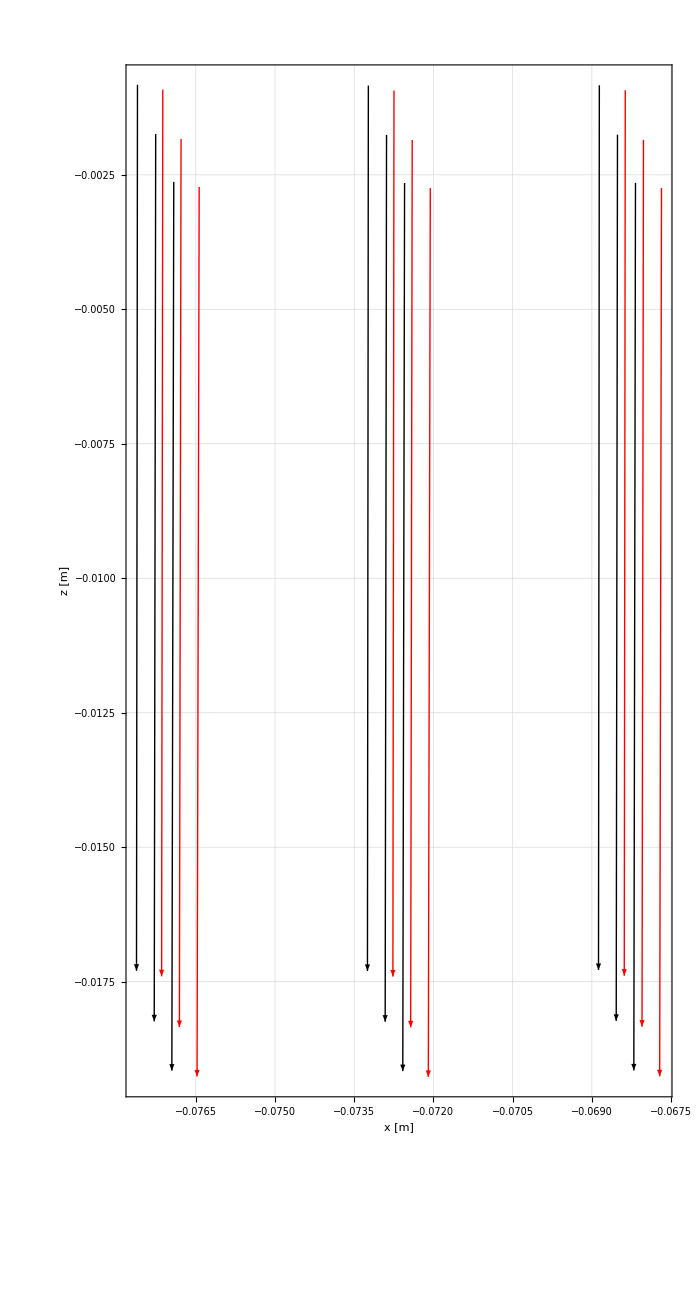

```mathematica
EndVectorXZ=Show[Table[
Graphics[
{
Black,
Arrow[
{
{RxBEndData[[i,1]],RxBEndData[[i,3]]},
{RxBEndData[[i,1]],RxBEndData[[i,3]]}+0.1*RxBEndData[[i,{7,9}]]
}
]
}],{i,1,horilines*vertilines}],
Table[
Graphics[
{
Red,
Arrow[
{
{RxBEndData[[i,10]],RxBEndData[[i,12]]},
{RxBEndData[[i,10]],RxBEndData[[i,12]]}+0.1*RxBEndData[[i,{13,15}]]
}
]
}],{i,1,horilines*vertilines}],
Axes->True,Frame->True,GridLines->Automatic,FrameLabel->{{"z [m]",None},{"x [m]","Bxz Vector at RxBEnd"}},FrameStyle->20,ImageSize->700]
```

## Shielding Investigations

```mathematica
SH10=Import["/home/dmoser/NoMoS_SH_mu10k_B-map.txt","Table"];
SH30=Import["/home/dmoser/NoMoS_SH_mu30k_B-map.txt","Table"];
Air=Import["/home/dmoser/NoMoS_SH_B-map_AIR.txt","Table"];
```

```mathematica
SH10Inter=Interpolation[Transpose[{SH10[[All,1;;3]],SH10[[All,4;;6]]}]];
SH30Inter=Interpolation[Transpose[{SH30[[All,1;;3]],SH30[[All,4;;6]]}]];
AirInter=Interpolation[Transpose[{Air[[All,1;;3]],Air[[All,4;;6]]}]];
```

```mathematica
AufM10[x_,y_,z_]:=SH10Inter[x,y,z]-AirInter[x,y,z]
AufM30[x_,y_,z_]:=SH30Inter[x,y,z]-AirInter[x,y,z]
Diff1030[x_,y_,z_]:=SH10Inter[x,y,z]-SH30Inter[x,y,z]
```

```mathematica
TubePlot=ListLinePlot[{
Table[{(R1-0.15/Sqrt[2])*Sin[th],(R1-0.15/Sqrt[2])*Cos[th]},{th,0,Pi,Pi/100}],
Table[{(R1+0.15/Sqrt[2])*Sin[th],(R1+0.15/Sqrt[2])*Cos[th]},{th,0,Pi,Pi/100}],
Table[{(R1)*Sin[th],(R1)*Cos[th]},{th,0,Pi,Pi/100}],
Table[{z,R1},{z,-1.475,0,0.01}],
Table[{z,R1-0.15/Sqrt[2]},{z,-1.475,0,0.01}],
Table[{z,R1+0.15/Sqrt[2]},{z,-1.475,0,0.01}],
Table[{z,-R1},{z,-0.5,0,0.01}]
},PlotStyle->Black,AspectRatio->Automatic];
```

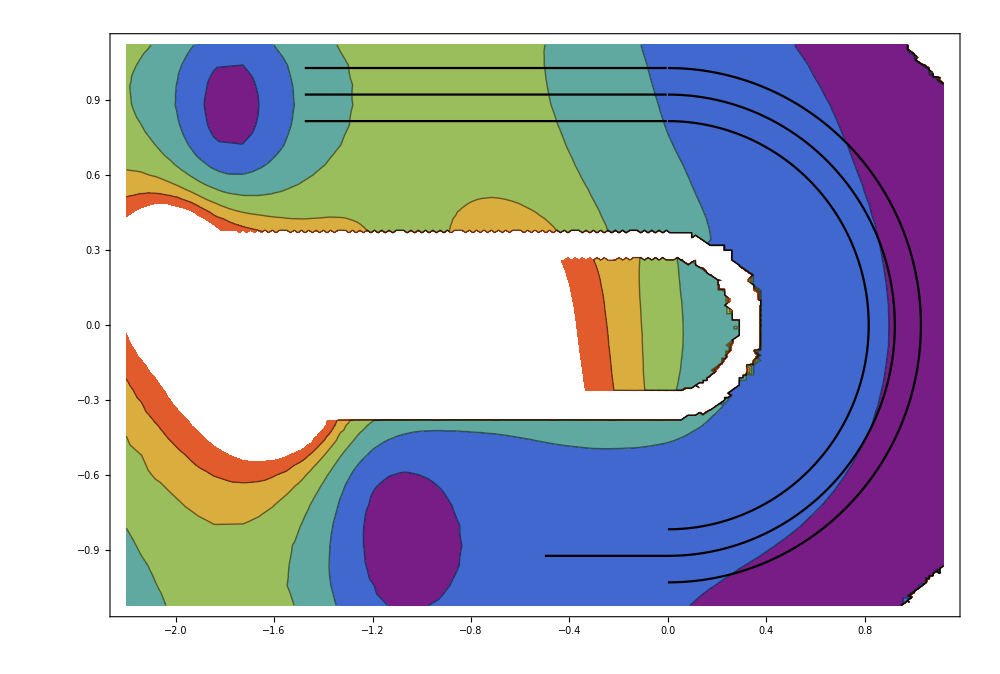

```mathematica
Show[
ContourPlot[Norm[Diff1030[0,y,z]],{z,-2.2,1.12},{y,-1.12,1.12},AspectRatio->Automatic,ImageSize->1000,ColorFunction->"Rainbow",PlotRange->{0,0.03}],
TubePlot]
```

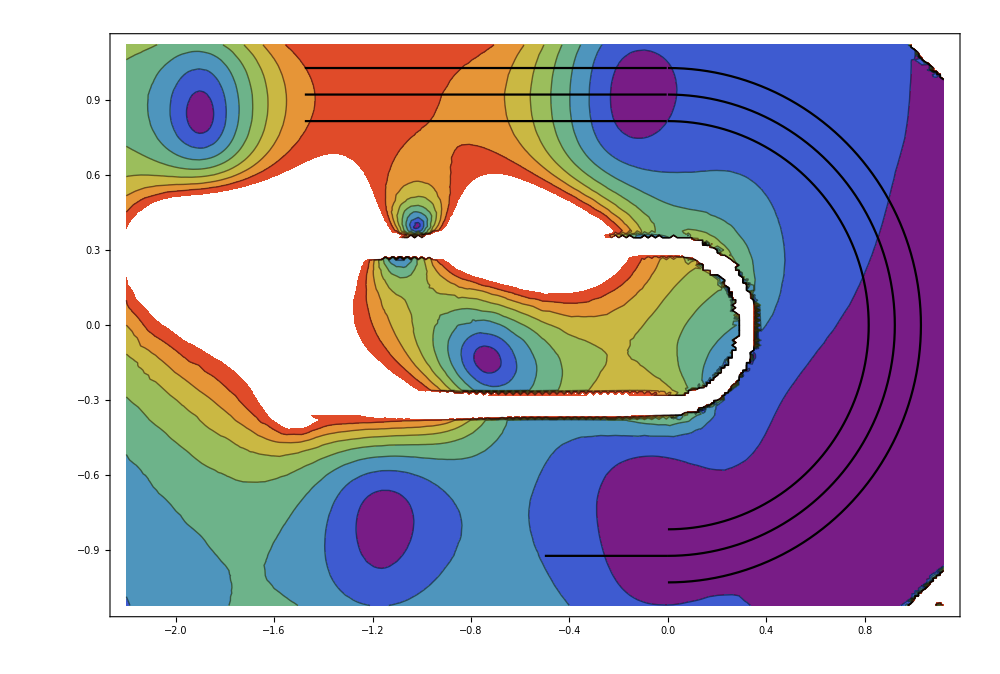

```mathematica
MiddleSHContourPlot=Show[
ContourPlot[Norm[AufM10[0,y,z]],{z,-2.2,1.12},{y,1.12,-1.12},AspectRatio->Automatic,ImageSize->1000,ColorFunction->"Rainbow",PlotRange->{0,8}],
TubePlot]
```

```mathematica
ContourLegend=BarLegend[{"Rainbow",{0,8}}];
```

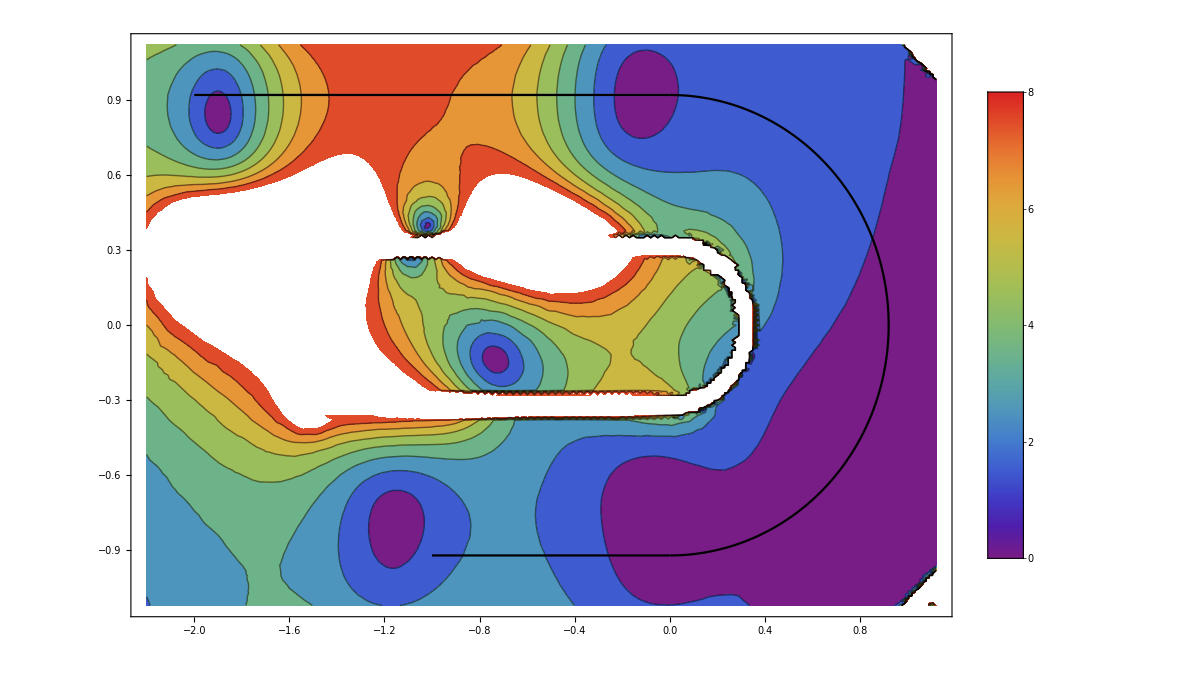

```mathematica
AufmPlot=Legended[Show[MiddleSHContourPlot,Plot[0.92,{x,-2,0}],Plot[0.92,{x,-2,0},PlotStyle->Black],ListLinePlot[Table[{0.92*Sin[th],0.92*Cos[th]},{th,0,Pi,0.01}],PlotStyle->Black],Plot[-0.92,{x,-1,0},PlotStyle->Black]],ContourLegend]
```

```mathematica
Export["/home/dmoser/AufmPlot.png",AufmPlot,ImageResolution->500]
```

/home/dmoser/AufmPlot.png

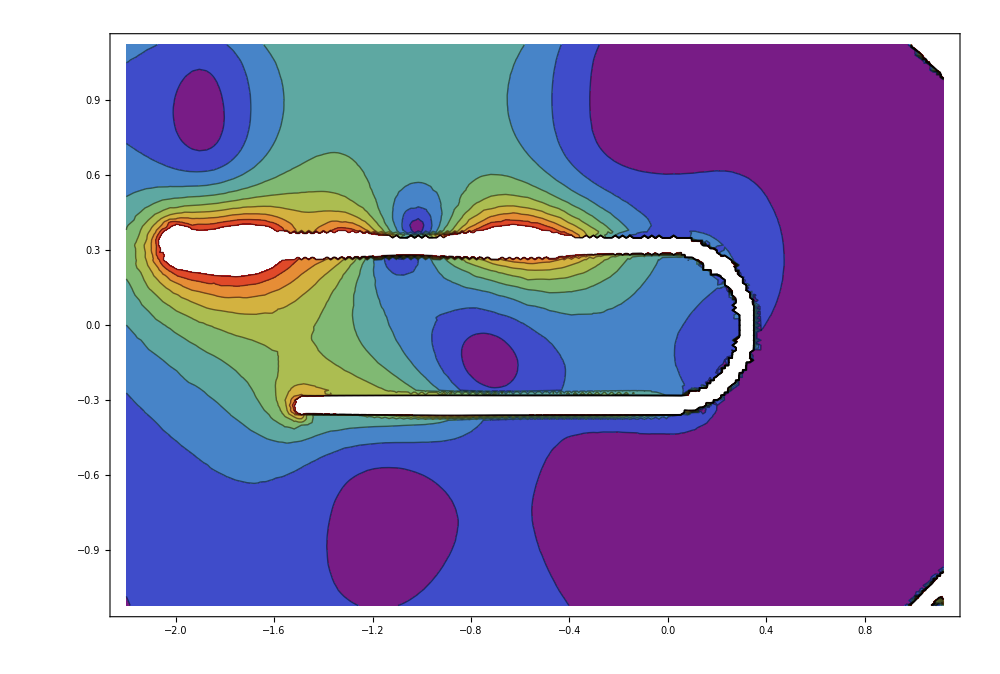

```mathematica
ContourPlot[Norm[AufM10[0.1,y,z]],{z,-2.2,1.12},{y,1.12,-1.12},AspectRatio->Automatic,ImageSize->1000,ColorFunction->"Rainbow"]
```

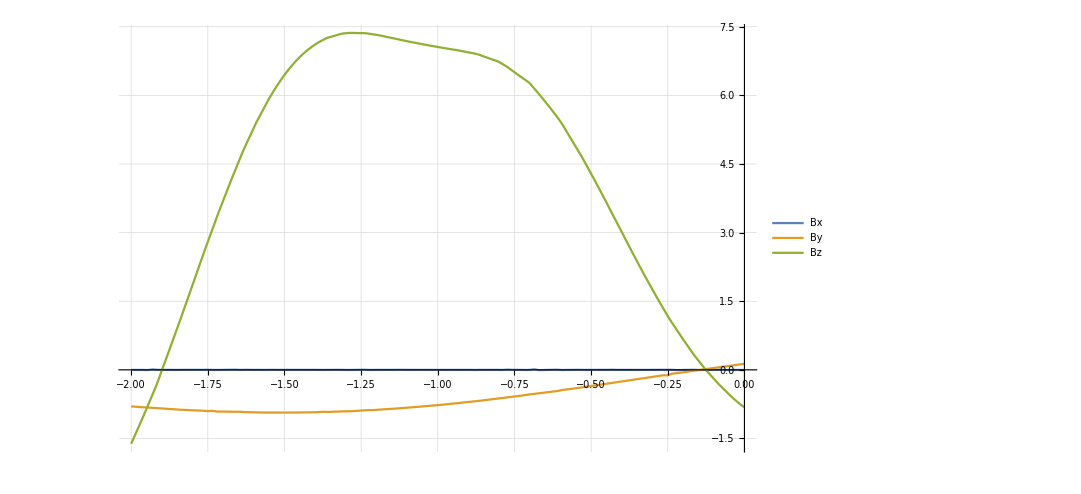

```mathematica
Plot[{AufM10[0,R1,z][[1]],AufM10[0,R1,z][[2]],AufM10[0,R1,z][[3]]},{z,-2,0},PlotLegends->{"Bx","By","Bz"},ImageSize->800,GridLines->Automatic]
```

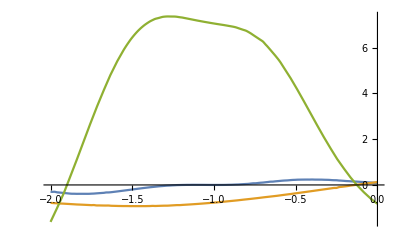

```mathematica
Plot[{AufM10[0.05,0.92+0.05,z][[1]],AufM10[0,0.92,z][[2]],AufM10[0,0.92,z][[3]]},{z,-2,0}]
```

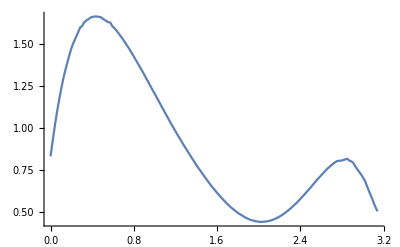

```mathematica
Plot[Norm[AufM10[0,0.92*Cos[th],0.92*Sin[th]]],{th,0,Pi}]
```

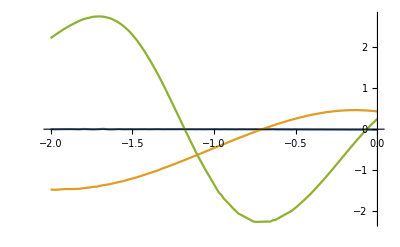

```mathematica
Plot[{AufM10[0,-0.92,z][[1]],AufM10[0,-0.92,z][[2]],AufM10[0,-0.92,z][[3]]},{z,-2,0}]
```

## Comparisons Traj

additional investigations (gyration radius)

### gyration radius along lines for different θ

```mathematica
ListLinePlot[
Table[
GuidingCenter[{#[[1]],#[[2]],#[[3]]},{#[[4]],#[[5]],#[[6]]},{#[[7]],#[[8]],#[[9]]}][[3,2]]&/@testtraj[[8,th,2,1]],{th,1,2}],PlotRange->All]
```

Part::partw: Part 8 of {«1»,«1»,{«1»},{«1»,«1»,{{{{0.025,0.875893,-1.475,-1.05624×10^8,733135.,1.25916×10^8,0.00002617,0.000979135,0.168144,0.025,0.871622,-1.47498,0.0000273427,0.000980498,0.168107,700000.,0.,1.85942×10^-8,0.,0.},{0.024332,0.875845,-1.4742,-1.04323×10^8,-1.57927×10^7,1.26012×10^8,0.0000219334,0.000985921,0.168146,0.0250003,0.871627,-1.47418,0.0000236845,0.000987885,0.168106,100000.,0.,6.35082×10^-12,0.336032,39.9987},«48»,«6677»},{{0.0207292,0.871622,-1.475,16783.1,-1.04907×10^8,1.26516×10^8,0.0000223027,0.00098149,«4»,0.0000274588,0.000980263,0.168107,100000.,0.,3.91284×10^-8,0.,0.},«49»,«6676»},{«1»},{«1»}},«1»}},{«1»},{«1»}} does not exist.

Part::partw: Part 7 of {«1»,«1»,{«1»},{«1»,«1»,{{{{0.025,0.875893,-1.475,-1.05624×10^8,733135.,1.25916×10^8,0.00002617,0.000979135,0.168144,0.025,0.871622,-1.47498,0.0000273427,0.000980498,0.168107,700000.,0.,1.85942×10^-8,0.,0.},{0.024332,0.875845,-1.4742,-1.04323×10^8,-1.57927×10^7,1.26012×10^8,0.0000219334,0.000985921,0.168146,0.0250003,0.871627,-1.47418,0.0000236845,0.000987885,0.168106,100000.,0.,6.35082×10^-12,0.336032,39.9987},«48»,«6677»},{{0.0207292,0.871622,-1.475,16783.1,-1.04907×10^8,1.26516×10^8,0.0000223027,0.00098149,«4»,0.0000274588,0.000980263,0.168107,100000.,0.,3.91284×10^-8,0.,0.},«49»,«6676»},{«1»},{«1»}},«1»}},{«1»},{«1»}} does not exist.

Part::partw: Part 8 of {«1»,«1»,{«1»},{«1»,«1»,{{{{0.025,0.875893,-1.475,-1.05624×10^8,733135.,1.25916×10^8,0.00002617,0.000979135,0.168144,0.025,0.871622,-1.47498,0.0000273427,0.000980498,0.168107,700000.,0.,1.85942×10^-8,0.,0.},{0.024332,0.875845,-1.4742,-1.04323×10^8,-1.57927×10^7,1.26012×10^8,0.0000219334,0.000985921,0.168146,0.0250003,0.871627,-1.47418,0.0000236845,0.000987885,0.168106,100000.,0.,6.35082×10^-12,0.336032,39.9987},«48»,«6677»},{{0.0207292,0.871622,-1.475,16783.1,-1.04907×10^8,1.26516×10^8,0.0000223027,0.00098149,«4»,0.0000274588,0.000980263,0.168107,100000.,0.,3.91284×10^-8,0.,0.},«49»,«6676»},{«1»},{«1»}},«1»}},{«1»},{«1»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Norm::nvm: The first Norm argument should be a number, vector, or matrix.

Dot::rect: Nonrectangular tensor encountered.

Cross::nonn1: The arguments are expected to be vectors of equal length, and the number of arguments is expected to be 1 less than their length.

Part::partd: Part specification 8⟦1⟧ is longer than depth of object.

Part::partd: Part specification 8⟦2⟧ is longer than depth of object.

Part::partd: Part specification 8⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression (5.68602×10^-12 √(Abs[8⟦4⟧]^2+Abs[8⟦5⟧]^2+Abs[8⟦6⟧]^2-(Part[«2»] Part[«2»]+Part[«2»] Part[«2»]+Part[«2»] Part[«2»])^2/(Abs[«1»]^2+Abs[«1»]^2+Abs[«1»]^2)))/(√(1+(-Abs[«1»]^2-Abs[«1»]^2-Abs[«1»]^2)/89875517873681764) √(Abs[8⟦7⟧]^2+Abs[8⟦8⟧]^2+Abs[8⟦9⟧]^2)) cannot be used as a part specification.

Norm::nvm: The first Norm argument should be a number, vector, or matrix.

Dot::rect: Nonrectangular tensor encountered.

Cross::nonn1: The arguments are expected to be vectors of equal length, and the number of arguments is expected to be 1 less than their length.

Part::pkspec1: The expression (5.68602×10^-12 √(Abs[8⟦4⟧]^2+Abs[8⟦5⟧]^2+Abs[8⟦6⟧]^2-(Part[«2»] Part[«2»]+Part[«2»] Part[«2»]+Part[«2»] Part[«2»])^2/(Abs[«1»]^2+Abs[«1»]^2+Abs[«1»]^2)))/(√(1+(-Abs[«1»]^2-Abs[«1»]^2-Abs[«1»]^2)/89875517873681764) √(Abs[8⟦7⟧]^2+Abs[8⟦8⟧]^2+Abs[8⟦9⟧]^2)) cannot be used as a part specification.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

Part::pkspec1: The expression (5.68602×10^-12 √(Abs[8⟦4⟧]^2+Abs[8⟦5⟧]^2+Abs[8⟦6⟧]^2-(Part[«2»] Part[«2»]+Part[«2»] Part[«2»]+Part[«2»] Part[«2»])^2/(Abs[«1»]^2+Abs[«1»]^2+Abs[«1»]^2)))/(√(1+(-Abs[«1»]^2-Abs[«1»]^2-Abs[«1»]^2)/89875517873681764) √(Abs[8⟦7⟧]^2+Abs[8⟦8⟧]^2+Abs[8⟦9⟧]^2)) cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

-Graphics-

Comparison with Field lines

### End and start Positions of Field lines VS Guiding centers

### guiding center Start position (theta=3 (20°),Ekin=2 (400keV),phi=1 (0°))

```mathematica
FirstGuidXYAll=Flatten[Table[Transpose[{testtraj[[All,3,2,phi,1,11]]-R1,testtraj[[All,3,2,phi,1,10]]}],{phi,1,4}],1];
```

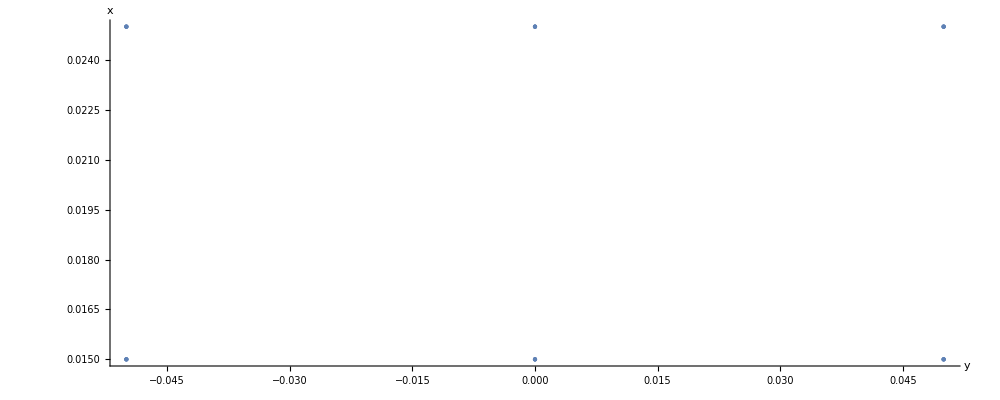

```mathematica
ListPlot[FirstGuidXYAll,ImageSize->1000,AxesLabel->{"y","x"},AspectRatio->Automatic,PlotStyle->PointSize->Medium]
```

```mathematica
Flatten[Table[testtraj[[All,3,2,phi,1,12]],{phi,1,4}],1]
```

{-1.47492,-1.47492,-1.47492,-1.47492,-1.47492,-1.47492,-1.475,-1.475,-1.475,-1.475,-1.475,-1.475,-1.47508,-1.47508,-1.47508,-1.47508,-1.47508,-1.47508,-1.475,-1.475,-1.475,-1.475,-1.475,-1.475}

### Bline Import, format = x,y,z,b,bx,by,bz,btang,brad

```mathematica
NamePart="bline_DOn_BxDOn_";
```

```mathematica
FileNamesB=Flatten[Table[Table[
NamePart<>XSteps[[x]]<>"_"<>YSteps[[y]]<>".txt",
{y,1,vertilines}],
{x,1,horilines}]];
```

```mathematica
FileB=Table[Cases[Import[Folder<>SubFolder<>FileNamesB[[i]],"Table"],{_,_,_,_,_,_,_,_,_}],{i,1,horilines*vertilines}];
```

Import::nffil: File not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

### Bline start position

```mathematica
BlineStart=Transpose[{FileB[[All,1,2]]-R1,FileB[[All,1,1]]}];
```

Part::partw: Part 1 of {} does not exist.

Transpose::nmtx: The first two levels of {-0.921622+{{},{},{},{},{},{}}⟦All,1,2⟧,{{},{},{},{},{},{}}⟦All,1,1⟧} cannot be transposed.

```mathematica
FileB[[All,1,3]]
```

Part::partw: Part 1 of {} does not exist.

{{},{},{},{},{},{}}⟦All,1,3⟧

### Plot both

```mathematica
ListPlot[{FirstGuidXYAll,BlineStart},ImageSize->1500,AxesLabel->{"y","x"},AspectRatio->Automatic,PlotStyle->PointSize->Medium]
```

ListPlot::lpn: {{{-0.0499998,0.015},{2.×10^-7,0.015},{0.0500002,0.015},{-0.0499998,0.025},{2.×10^-7,0.025},{0.0500002,0.025},{-0.05,0.015},{0.,0.015},{0.05,0.015},{-0.05,0.025},{0.,0.025},{0.05,«6»},«1»,{-2.×10^-7,0.015},{0.0499998,0.015},{-0.0500002,0.025},{-2.×10^-7,0.025},{0.0499998,0.025},{-0.05,0.015},{0.,0.015},{0.05,0.015},{-0.05,0.025},{0.,0.025},{0.05,0.025}},«1»} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[{{{-0.0499998,0.015},{2.×10^-7,0.015},{0.0500002,0.015},{-0.0499998,0.025},{2.×10^-7,0.025},{0.0500002,0.025},{-0.05,0.015},{0.,0.015},{0.05,0.015},{-0.05,0.025},{0.,0.025},{0.05,0.025},{-0.0500002,0.015},{-2.×10^-7,0.015},{0.0499998,0.015},{-0.0500002,0.025},{-2.×10^-7,0.025},{0.0499998,0.025},{-0.05,0.015},{0.,0.015},{0.05,0.015},{-0.05,0.025},{0.,0.025},{0.05,0.025}},Transpose[{-0.921622+{{},{},{},{},{},{}}⟦All,1,2⟧,{{},{},{},{},{},{}}⟦All,1,1⟧}]},ImageSize→1500,AxesLabel→{y,x},AspectRatio→Automatic,PlotStyle→PointSize→Medium]

### Now check at the end of the RxB

```mathematica
ThetaEndPos=3;EkinEndPos=4;
```

```mathematica
LastRxBPos=Table[Table[
Last[Flatten[Position[testtraj[[line,ThetaEndPos,EkinEndPos,phi,All,11;;12]],{_?(#<0&),_?(#>=0&)}]]],
{phi,1,4}],
{line,1,15}]
```

Part::partw: Part 4 of {{{{0.015,0.875893,-1.475,-1.05633×10^8,734730.,1.25909×10^8,0.0000150052,0.000981471,0.168179,0.015,0.871622,-1.47498,0.0000157188,0.000983001,0.168143,700000.,0.,1.8592×10^-8,0.,0.},«49»,«6675»},{«1»},{«1»},{{0.0192708,0.871622,-1.475,15353.5,1.06377×10^8,1.25282×10^8,0.0000206046,0.000981856,0.16813,0.015,0.871622,-1.475,0.0000157839,0.000982782,0.168143,100000.,0.,3.90977×10^-8,0.,0.},{0.0192183,0.872295,-1.4742,-1.65108×10^7,1.05077×10^8,1.25292×10^8,0.0000176445,0.000988809,0.168136,0.0149997,0.871627,-1.4742,0.0000136465,0.000989974,0.168143,100000.,0.,6.35136×10^-12,0.337008,39.9976},«48»,«6672»}},{«1»}} does not exist.

Last::nolast: {} has zero length and no last element.

Part::partw: Part 4 of {{{{0.015,0.875893,-1.475,-1.05633×10^8,734730.,1.25909×10^8,0.0000150052,0.000981471,0.168179,0.015,0.871622,-1.47498,0.0000157188,0.000983001,0.168143,700000.,0.,1.8592×10^-8,0.,0.},«49»,«6675»},{«1»},{«1»},{{0.0192708,0.871622,-1.475,15353.5,1.06377×10^8,1.25282×10^8,0.0000206046,0.000981856,0.16813,0.015,0.871622,-1.475,0.0000157839,0.000982782,0.168143,100000.,0.,3.90977×10^-8,0.,0.},{0.0192183,0.872295,-1.4742,-1.65108×10^7,1.05077×10^8,1.25292×10^8,0.0000176445,0.000988809,0.168136,0.0149997,0.871627,-1.4742,0.0000136465,0.000989974,0.168143,100000.,0.,6.35136×10^-12,0.337008,39.9976},«48»,«6672»}},{«1»}} does not exist.

Last::nolast: {} has zero length and no last element.

Part::partw: Part 4 of {{{{0.015,0.875893,-1.475,-1.05633×10^8,734730.,1.25909×10^8,0.0000150052,0.000981471,0.168179,0.015,0.871622,-1.47498,0.0000157188,0.000983001,0.168143,700000.,0.,1.8592×10^-8,0.,0.},«49»,«6675»},{«1»},{«1»},{{0.0192708,0.871622,-1.475,15353.5,1.06377×10^8,1.25282×10^8,0.0000206046,0.000981856,0.16813,0.015,0.871622,-1.475,0.0000157839,0.000982782,0.168143,100000.,0.,3.90977×10^-8,0.,0.},{0.0192183,0.872295,-1.4742,-1.65108×10^7,1.05077×10^8,1.25292×10^8,0.0000176445,0.000988809,0.168136,0.0149997,0.871627,-1.4742,0.0000136465,0.000989974,0.168143,100000.,0.,6.35136×10^-12,0.337008,39.9976},«48»,«6672»}},{«1»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

{{Last[{}],Last[{}],Last[{}],Last[{}]},{Last[{}],Last[{}],Last[{}],Last[{}]},{Last[{}],Last[{}],Last[{}],Last[{}]},{Last[{}],Last[{}],Last[{}],Last[{}]},{Last[{}],Last[{}],Last[{}],Last[{}]},{Last[{}],Last[{}],Last[{}],Last[{}]},{Last[{}],Last[{}],Last[{}],Last[{}]},{Last[{}],Last[{}],Last[{}],Last[{}]},{Last[{}],Last[{}],Last[{}],Last[{}]},{Last[{}],Last[{}],Last[{}],Last[{}]},{Last[{}],Last[{}],Last[{}],Last[{}]},{Last[{}],Last[{}],Last[{}],Last[{}]},{Last[{}],Last[{}],Last[{}],Last[{}]},{Last[{}],Last[{}],Last[{}],Last[{}]},{Last[{}],Last[{}],Last[{}],Last[{}]}}

```mathematica
ListPlot[Table[
Table[
{testtraj[[line,ThetaEndPos,EkinEndPos,phi,LastRxBPos[[line,phi]],11]]+R1,testtraj[[line,ThetaEndPos,EkinEndPos,phi,LastRxBPos[[line,phi]],10]]},
{line,1,15}],
{phi,1,4}],ImageSize->1400,Frame->True,FrameLabel->{{"x [m]",None},{"y [m]","EndXY of GuidCenter for each line and phi (y - R1)"}},GridLines->Automatic,FrameStyle->15,AspectRatio->Automatic,PlotStyle->PointSize->Small
]
```

Part::pkspec1: The expression Last[{}] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

$Aborted

## Compare two same calculation types of 2 set-ups, File1, File2

### Set Folder

```mathematica
Folder="/home/dmoser/MagSimResults";SubFolder1="/NoMoS+OutletCorr/";SubFolder2="/NoMoS_withOutCorr_Inletadapt_thinner_filtershift2/";
```

B Line Comparison

### Info Files and Names

```mathematica
InfoFiles=Which[
(OutputType[[1]]=="bline"&&OutputType[[2]]==True&&OutputType[[3]]==True),
{
Import[Folder<>SubFolder1<>"bline_DOn_BxDOn_info.txt","Table"],
Import[Folder<>SubFolder2<>"bline_DOn_BxDOn_info.txt","Table"]
},
!(OutputType[[1]]=="bline"&&OutputType[[1]]==True&&OutputType[[1]]==True),
InfoFiles="meh"
]
```

{{{R_1,horilines,vertilines,apertsizeX,apertsizeY,driftOn,BxDrift},{0.901622,3,5,0.01,0.1,1,1}},{{R_1,horilines,vertilines,apertsizeX,apertsizeY,driftOn,BxDrift},{0.901622,3,5,0.01,0.1,1,1}}}

```mathematica
If[InfoFiles[[1,2,2;;-1]]≠InfoFiles[[2,2,2;;-1]],"MEEEEP"]
```

```mathematica
horilines=InfoFiles[[1,2,2]];vertilines=InfoFiles[[1,2,3]];ApertX=InfoFiles[[1,2,4]];ApertY=InfoFiles[[1,2,5]];R1=InfoFiles[[1,2,1]];R2=InfoFiles[[2,2,1]];
```

```mathematica
XStep=ApertX/(horilines-1);YStep=ApertY/(vertilines-1);
```

```mathematica
XSteps=Table["X"<>ToString[If[-ApertX/2+XStep*x==0.,0,-ApertX/2+XStep*x]],{x,0,horilines-1}];
YSteps=Table["Y"<>ToString[If[-ApertY/2+YStep*x==0.,0,-ApertY/2+YStep*x]],{x,0,vertilines-1}];
```

```mathematica
XYNames=Flatten[Table[Table[
XSteps[[x]]<>"_"<>YSteps[[y]],
{y,1,vertilines}],
{x,1,horilines}]]
```

{X-0.005_Y-0.05,X-0.005_Y-0.025,X-0.005_Y0,X-0.005_Y0.025,X-0.005_Y0.05,X0_Y-0.05,X0_Y-0.025,X0_Y0,X0_Y0.025,X0_Y0.05,X0.005_Y-0.05,X0.005_Y-0.025,X0.005_Y0,X0.005_Y0.025,X0.005_Y0.05}

### Names further

```mathematica
NamePart=Which[
(OutputType[[1]]=="bline"&&OutputType[[2]]==True&&OutputType[[3]]==True),
"bline_DOn_BxDOn_",
!(OutputType[[1]]=="bline"&&OutputType[[2]]==True&&OutputType[[3]]==True),
"meh"
]
```

bline_DOn_BxDOn_

```mathematica
FileNames12=Flatten[Table[Table[
NamePart<>XSteps[[x]]<>"_"<>YSteps[[y]]<>".txt",
{y,1,vertilines}],
{x,1,horilines}]]
```

{bline_DOn_BxDOn_X-0.005_Y-0.05.txt,bline_DOn_BxDOn_X-0.005_Y-0.025.txt,bline_DOn_BxDOn_X-0.005_Y0.txt,bline_DOn_BxDOn_X-0.005_Y0.025.txt,bline_DOn_BxDOn_X-0.005_Y0.05.txt,bline_DOn_BxDOn_X0_Y-0.05.txt,bline_DOn_BxDOn_X0_Y-0.025.txt,bline_DOn_BxDOn_X0_Y0.txt,bline_DOn_BxDOn_X0_Y0.025.txt,bline_DOn_BxDOn_X0_Y0.05.txt,bline_DOn_BxDOn_X0.005_Y-0.05.txt,bline_DOn_BxDOn_X0.005_Y-0.025.txt,bline_DOn_BxDOn_X0.005_Y0.txt,bline_DOn_BxDOn_X0.005_Y0.025.txt,bline_DOn_BxDOn_X0.005_Y0.05.txt}

### import. format = x,y,z,b,bx,by,bz,btang,brad (variable for type of comparison)

```mathematica
File1=Table[Cases[Import[Folder<>SubFolder1<>FileNames12[[i]],"Table"],{_,_,_,_,_,_,_,_,_}],{i,1,horilines*vertilines}];
File2=Table[Cases[Import[Folder<>SubFolder2<>FileNames12[[i]],"Table"],{_,_,_,_,_,_,_,_,_}],{i,1,horilines*vertilines}];
```

### length of datasets and areas

```mathematica
Data1RxBStart=Table[First[Position[File1[[ii]],{_,_,_?(#≥0.&),_,_,_,_,_,_}]][[1]],{ii,1,horilines*vertilines}]
Data2RxBStart=Table[First[Position[File2[[ii]],{_,_,_?(#≥0.&),_,_,_,_,_,_}]][[1]],{ii,1,horilines*vertilines}]
```

{202,202,202,202,202,202,202,202,202,202,202,202,202,202,202}

{202,202,202,202,202,202,202,202,202,202,202,202,202,202,202}

```mathematica
File1[[1,190]]
```

{-0.00447731,0.856595,-0.0606814,0.164498,0.0000359916,-0.00534598,0.164411,0.164411,0.0053461}

```mathematica
Data1OutletStart=Table[First[Position[File1[[ii]],{_,_?(#<0&),_?(#<=0.&),_,_,_,_,_,_}]][[1]],{ii,1,horilines*vertilines}]
Data2OutletStart=Table[First[Position[File2[[ii]],{_,_?(#<0&),_?(#<=0.&),_,_,_,_,_,_}]][[1]],{ii,1,horilines*vertilines}]
```

{689,701,714,728,741,689,701,714,728,741,689,701,714,728,741}

{687,701,715,729,744,687,701,715,729,744,687,701,715,729,744}

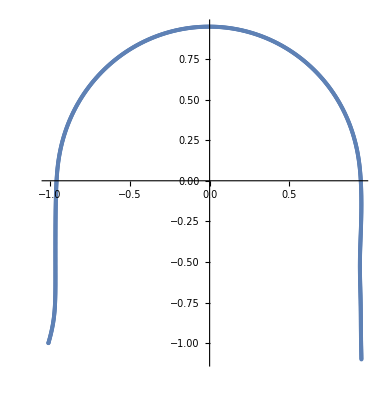

```mathematica
ListPlot[File2[[5,All,2;;3]],AspectRatio->Automatic]
```

### Angles

```mathematica
Angle1=
Table[
Table[
Which[File1[[i,ii,2]]>0,
ArcTan[File1[[i,ii,3]]/File1[[i,ii,2]]],
File1[[i,ii,2]]<0&&File1[[i,ii,3]]>0,
ArcTan[-File1[[i,ii,2]]/File1[[i,ii,3]]]+Pi/2,
File1[[i,ii,2]]<0&&File1[[i,ii,3]]<0,
ArcTan[File1[[i,ii,3]]/File1[[i,ii,2]]]+Pi
],{ii,Data1RxBStart[[i]],Data1OutletStart[[i]]-1}],
{i,1,horilines*vertilines}];
Angle2=
Table[
Table[
Which[File2[[i,ii,2]]>0,
ArcTan[File2[[i,ii,3]]/File2[[i,ii,2]]],
File2[[i,ii,2]]<0&&File2[[i,ii,3]]>0,
ArcTan[-File2[[i,ii,2]]/File2[[i,ii,3]]]+Pi/2,
File2[[i,ii,2]]<0&&File2[[i,ii,3]]<0,
ArcTan[File2[[i,ii,3]]/File2[[i,ii,2]]]+Pi
],{ii,Data2RxBStart[[i]],Data2OutletStart[[i]]-1}],
{i,1,horilines*vertilines}];
```

```mathematica
File1End=Table[File1[[ii]]//Length,{ii,1,horilines*vertilines}]
File2End=Table[File2[[ii]]//Length,{ii,1,horilines*vertilines}]
```

{872,884,897,911,924,872,884,897,911,925,872,884,897,911,925}

{870,883,898,912,928,870,884,898,912,928,870,884,898,913,928}

### X Plot in RxB

```mathematica
XPlot1=ListLinePlot[Table[Transpose[{Angle1[[i]]/Pi*180.,File1[[i,Data1RxBStart[[i]];;Data1OutletStart[[i]]-1,1]]}],{i,1,horilines*vertilines}],ImageSize->700,PlotStyle->Blue];
XPlot2=ListLinePlot[Table[Transpose[{Angle2[[i]]/Pi*180.,File2[[i,Data2RxBStart[[i]];;Data2OutletStart[[i]]-1,1]]}],{i,1,horilines*vertilines}],ImageSize->700,PlotStyle->Red];
```

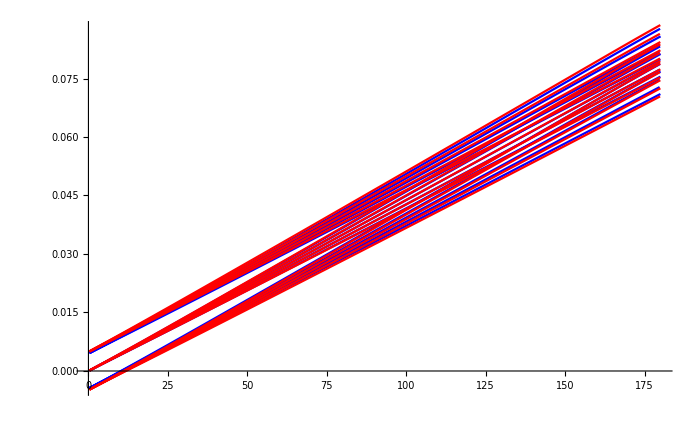

```mathematica
Show[XPlot1,XPlot2]
```

### XZ position

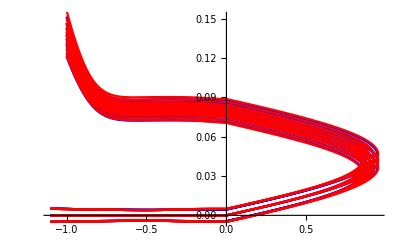

```mathematica
XZPlot1=ListLinePlot[Table[Transpose[{File1[[i,All,3]],File1[[i,All,1]]}],{i,1,horilines*vertilines}],PlotStyle->Blue];
XZPlot2=ListLinePlot[Table[Transpose[{File2[[i,All,3]],File2[[i,All,1]]}],{i,1,horilines*vertilines}],PlotStyle->Red];
Show[XZPlot1,XZPlot2]
```

### YZ Position

```mathematica
PipeDiag=300/1000;Pipea=PipeDiag/Sqrt[2];
```

```mathematica
YZPlot1=ListLinePlot[Table[File1[[i,All,2;;3]],{i,1horilines*vertilines}],ImageSize->700,PlotStyle->Blue];
YZPlot2=ListLinePlot[Table[File2[[i,All,2;;3]],{i,1horilines*vertilines}],ImageSize->700,PlotStyle->Red];
RConst=ListLinePlot[Table[{-Cos[th]*R1,Sin[th]*R1},{th,0,Pi,Pi/100.}],PlotStyle->Directive[Thickness[0.01],Orange]];
PipePlot=ListLinePlot[{Table[{-Cos[th]*(R1+Pipea/2),Sin[th]*(R1+Pipea/2)},{th,0,Pi,Pi/100.}],Table[{-Cos[th]*(R1-Pipea/2),Sin[th]*(R1-Pipea/2)},{th,0,Pi,Pi/100.}]},PlotStyle->Directive[Thickness[0.005],Black]];
```

```mathematica
YZ12=Show[YZPlot1,YZPlot2,RConst,PipePlot,ImageSize->900,AspectRatio->Automatic,GridLines->Automatic,Frame->True,FrameLabel->{{"z [m]",None},{"y [m]","YZ pos."}},FrameStyle->20,PlotRange->{{-1.05,1.05},Automatic},Epilog->Inset[Style[Text["350 pipe, /Sqrt[2]"],20],Scaled[{0.15,0.95}]]]
```

-Graphics-

```mathematica
(*Export["/home/dmoser/MagSimResults/STD_PERC05/YZ_pos_vsSTD.png",YZ12,ImageResolution->500];*)
```

### |B| along the field lines

```mathematica
(*ListLinePlot[Table[Transpose[{Angle1[[ii]]/Pi*180.,File1[[ii,All,4]]}],{ii,1,horilines*vertilines}],ImageSize->900,(*PlotRange->{0,0.4},*)Frame->True,FrameLabel->{{None,None},{"θ [°]","RxB |B|"}},FrameStyle->15,GridLines->Automatic]*)
```

```mathematica
Inlet1Bline=ListLinePlot[Table[Transpose[{File1[[ii,1;;Data1RxBStart[[ii]]-1,3]],File1[[ii,1;;Data1RxBStart[[ii]]-1,4]]}],{ii,1,horilines*vertilines}],ImageSize->900,(*PlotRange->{0,0.4},*)Frame->True,FrameLabel->{{None,None},{"z [m]","Inlet |B|"}},FrameStyle->15,GridLines->Automatic,PlotRange->{{-1.1,0},{-0.01,0.35}},PlotStyle->Directive[Blue,Opacity[0.4]],PlotRangePadding->{None,None},ImagePadding->{{60, 1},{50,40}}];
Inlet2Bline=ListLinePlot[Table[Transpose[{File2[[ii,1;;Data2RxBStart[[ii]]-1,3]],File2[[ii,1;;Data2RxBStart[[ii]]-1,4]]}],{ii,1,horilines*vertilines}],ImageSize->900,(*PlotRange->{0,0.4},*)Frame->True,FrameLabel->{{None,None},{"z [m]","Inlet |B|"}},FrameStyle->15,GridLines->Automatic,PlotRange->{{-1.1,0},{-0.01,0.35}},PlotStyle->Directive[Red,Opacity[0.4]],PlotRangePadding->{None,None},ImagePadding->{{60, 1},{50,40}}];
InletBlines=Show[Inlet1Bline,Inlet2Bline,ImageSize->510];
```

```mathematica
RxB1BLine=ListLinePlot[Table[Transpose[{Angle1[[ii]]/Pi*180.,File1[[ii,Data1RxBStart[[ii]];;Data1OutletStart[[ii]]-1,4]]}],{ii,1,horilines*vertilines}],Frame->True,FrameLabel->{{None,None},{"θ [°]","RxB |B|"}},FrameStyle->15,GridLines->Automatic,PlotStyle->Opacity[0.4,Blue],PlotRange->{-0.01,0.35},PlotRangePadding->{None,None},ImagePadding->{{0, 1},{50,40}}];
RxB2BLine=ListLinePlot[Table[Transpose[{Angle2[[ii]]/Pi*180.,File2[[ii,Data2RxBStart[[ii]];;Data2OutletStart[[ii]]-1,4]]}],{ii,1,horilines*vertilines}],Frame->True,FrameLabel->{{None,None},{"θ [°]","RxB |B|"}},FrameStyle->15,GridLines->Automatic,PlotStyle->Opacity[0.4,Red],PlotRange->{-0.01,0.35},PlotRangePadding->{None,None},ImagePadding->{{0, 1},{50,40}}];
```

```mathematica
RxBBLines=Show[RxB1BLine,RxB2BLine,ImageSize->450];
```

```mathematica
Outlet1Bline=ListLinePlot[Table[Transpose[{-File1[[ii,Data1OutletStart[[ii]];;-1,3]],File1[[ii,Data1OutletStart[[ii]];;-1,4]]}],{ii,1,horilines*vertilines}],ImageSize->900,(*PlotRange->{0,0.4},*)Frame->True,FrameLabel->{{None,None},{"-z [m]","Outlet |B|"}},FrameStyle->15,GridLines->Automatic,PlotRange->{-0.01,0.35},PlotStyle->Directive[Blue,Opacity[0.4]],PlotRangePadding->{None,None},ImagePadding->{{0, 1},{50,40}}];
Outlet2Bline=ListLinePlot[Table[Transpose[{-File2[[ii,Data2OutletStart[[ii]];;-1,3]],File2[[ii,Data2OutletStart[[ii]];;-1,4]]}],{ii,1,horilines*vertilines}],ImageSize->900,(*PlotRange->{0,0.4},*)Frame->True,FrameLabel->{{None,None},{"-z [m]","Outlet |B|"}},FrameStyle->15,GridLines->Automatic,PlotRange->{-0.01,0.35},PlotStyle->Directive[Red,Opacity[0.4]],PlotRangePadding->{None,None},ImagePadding->{{0, 1},{50,40}}];
OutletBLines=Show[Outlet1Bline,Outlet2Bline,ImageSize->450];
```

```mathematica
Row[{InletBlines,RxBBLines,OutletBLines}]
```

-Graphics--Graphics--Graphics-

### “Detector” positions. If “artificial” drift is added, again removed at results for comparison

```mathematica
DetPosPlot1=ListPlot[Table[{File1[[i,Data1OutletStart[[i]],2]]+R1,File1[[i,Data1OutletStart[[i]],1]]-If[InfoFiles[[1,2,6]]==1,0.085,0]},{i,1,horilines*vertilines}],AspectRatio->Automatic,PlotStyle->Blue];
DetPosPlot2=ListPlot[Table[{File2[[i,Data2OutletStart[[i]],2]]+R2,File2[[i,Data2OutletStart[[i]],1]]-If[InfoFiles[[1,2,6]]==1,0.085,0]},{i,1,horilines*vertilines}],AspectRatio->Automatic,PlotStyle->Red];
```

```mathematica
Show[DetPosPlot1,DetPosPlot2,Frame->True,PlotRange->All,Frame->True,FrameLabel->{{"x shift w/o RxBDrift [m]",None},{"y shift [m]","XY Positions at RxB end"}},FrameStyle->20,ImageSize->1300]
```

-Graphics-

### start vector at RxB

```mathematica
StartVector1=Table[Graphics[{Blue,Arrow[{{File1[[i,Data1RxBStart[[i]],2]]-R1,File1[[i,Data1RxBStart[[i]],3]]},{File1[[i,Data1RxBStart[[i]],2]]-R1,File1[[i,Data1RxBStart[[i]],3]]}+0.1*File1[[i,Data1RxBStart[[i]],6;;7]]}]}],{i,1,horilines*vertilines}];
StartVector2=Table[Graphics[{Red,Arrow[{{File2[[i,Data2RxBStart[[i]],2]]-R2,File2[[i,Data2RxBStart[[i]],3]]},{File2[[i,Data2RxBStart[[i]],2]]-R2,File2[[i,Data2RxBStart[[i]],3]]}+0.1*File2[[i,Data2RxBStart[[i]],6;;7]]}]}],{i,1,horilines*vertilines}];
```

```mathematica
Show[StartVector1,StartVector2,Axes->True,Frame->True,GridLines->Automatic,FrameLabel->{{"z [m]",None},{"y - R [m]","Byz Vector at RxBStart"}},FrameStyle->20]
```

-Graphics-

```mathematica
StartAngles1=Table[ArcTan[-File1[[i,Data1RxBStart[[i]],6]]/File1[[i,Data2RxBStart[[i]],7]]]/Pi*180.,{i,1,horilines*vertilines}]
StartAngles2=Table[ArcTan[-File2[[i,Data2RxBStart[[i]],6]]/File2[[i,Data2RxBStart[[i]],7]]]/Pi*180.,{i,1,horilines*vertilines}]
```

{3.58744,3.64824,3.62455,3.52293,3.34681,3.58808,3.6488,3.62511,3.52344,3.34733,3.58734,3.64817,3.62448,3.52287,3.34675}

{3.5432,3.65404,3.65702,3.56488,3.38642,3.54407,3.65481,3.65771,3.56551,3.38701,3.54313,3.65397,3.65695,3.56481,3.38637}

### YZ Vectors at end of RxB

```mathematica
(*YZVector1=ListStreamPlot[Table[{File1[[i,-1,2;;3]],File1[[i,-1,6;;7]]},{i,1,horilines*vertilines}],VectorStyle->Blue];
YZVector2=ListStreamPlot[Table[{File2[[i,-1,2;;3]],File2[[i,-1,6;;7]]},{i,1,horilines*vertilines}],VectorStyle->Red];*)
```

```mathematica
(*Show[YZVector1,YZVector2]*)
```

```mathematica
EndVector1=Table[Graphics[{Blue,Arrow[{{File1[[i,Data1OutletStart[[i]],2]]+R1,File1[[i,Data1OutletStart[[i]],3]]},{File1[[i,Data1OutletStart[[i]],2]]+R1,File1[[i,Data1OutletStart[[i]],3]]}+0.1*File1[[i,Data1OutletStart[[i]],6;;7]]}]}],{i,1,horilines*vertilines}];
EndVector2=Table[Graphics[{Red,Arrow[{{File2[[i,Data2OutletStart[[i]],2]]+R2,File2[[i,Data2OutletStart[[i]],3]]},{File2[[i,Data2OutletStart[[i]],2]]+R2,File2[[i,Data2OutletStart[[i]],3]]}+0.1*File2[[i,Data2OutletStart[[i]],6;;7]]}]}],{i,1,horilines*vertilines}];
```

```mathematica
Show[EndVector1,EndVector2,Axes->True,Frame->True,GridLines->Automatic,FrameLabel->{{"z [m]",None},{"y + R [m]","Byz Vector at RxBEnd"}},FrameStyle->20]
```

-Graphics-

```mathematica
EndAngles1=Table[ArcTan[-File1[[i,Data1OutletStart[[i]],6]]/File1[[i,Data1OutletStart[[i]],7]]]/Pi*180.,{i,1,horilines*vertilines}]
EndAngles2=Table[ArcTan[-File2[[i,Data2OutletStart[[i]],6]]/File2[[i,Data2OutletStart[[i]],7]]]/Pi*180.,{i,1,horilines*vertilines}]
```

{-3.32422,-3.48286,-3.41908,-3.1549,-2.99516,-3.30324,-3.46238,-3.39835,-3.1335,-2.97163,-3.2816,-3.44119,-3.3768,-3.11109,-2.94681}

{-3.37403,-3.42201,-3.42912,-3.37974,-3.11205,-3.35009,-3.3988,-3.40602,-3.35559,-3.08577,-3.32547,-3.37478,-3.38194,-3.33024,-3.05789}

Center line comparison

```mathematica
OS="Linux";Folder="/home/dmoser/MagSimResults";
SubFolder1="/4thCompare_trajVSBlines/";
SubFolder2="/NoMoS+OutletCorr/";
SetUp="NoMoSOnly";
RxBN=39;OutletN=8;InletN=8;HelmN=2;FilterN=1;ConnecN=4;
```

### filenames

```mathematica
Which[OS=="Linux",
SetDirectory["/home/dmoser/MagSimResults"<>SubFolder1];,
OS=="Mac",
"meh"
]
```

```mathematica
InfoFileCenter=Import["center_info.txt","Table"]
```

{{R_1,horilines,vertilines,apertsizeX,apertsizeY},{0.901622,3,5,0.01,0.1}}

```mathematica
R1=InfoFileCenter[[2,1]];horilines=InfoFileCenter[[2,2]];vertilines=InfoFileCenter[[2,3]];apertX=InfoFileCenter[[2,4]];apertY=InfoFileCenter[[2,5]];
```

```mathematica
XStep=apertX/(horilines-1);YStep=apertY/(vertilines-1);
```

```mathematica
XSteps=Table["X"<>ToString[If[-apertX/2+XStep*x==0.,0,-apertX/2+XStep*x]],{x,0,horilines-1}]
YSteps=Table["Y"<>ToString[If[-apertY/2+YStep*x==0.,0,-apertY/2+YStep*x]],{x,0,vertilines-1}]
```

{X-0.005,X0,X0.005}

{Y-0.05,Y-0.025,Y0,Y0.025,Y0.05}

```mathematica
CenterXY=Flatten[Table[Table[
XSteps[[x]]<>"_"<>YSteps[[y]],
{y,1,vertilines}],
{x,1,horilines}]]
```

{X-0.005_Y-0.05,X-0.005_Y-0.025,X-0.005_Y0,X-0.005_Y0.025,X-0.005_Y0.05,X0_Y-0.05,X0_Y-0.025,X0_Y0,X0_Y0.025,X0_Y0.05,X0.005_Y-0.05,X0.005_Y-0.025,X0.005_Y0,X0.005_Y0.025,X0.005_Y0.05}

```mathematica
CenterFileNames=Flatten[Table[Table[
"center_"<>XSteps[[x]]<>"_"<>YSteps[[y]]<>".txt",
{y,1,vertilines}],
{x,1,horilines}]]
```

{center_X-0.005_Y-0.05.txt,center_X-0.005_Y-0.025.txt,center_X-0.005_Y0.txt,center_X-0.005_Y0.025.txt,center_X-0.005_Y0.05.txt,center_X0_Y-0.05.txt,center_X0_Y-0.025.txt,center_X0_Y0.txt,center_X0_Y0.025.txt,center_X0_Y0.05.txt,center_X0.005_Y-0.05.txt,center_X0.005_Y-0.025.txt,center_X0.005_Y0.txt,center_X0.005_Y0.025.txt,center_X0.005_Y0.05.txt}

### get info of helmholtz coils so we can approx. illustrate pumpport position in inlet plot (Pos in data has to be set manually)

```mathematica
CoilData=Import[Folder<>SubFolder2<>"inputcoil_RxB.dat","Table"];
```

```mathematica
HelmHoltzPos=1+RxBN+OutletN+InletN+1;
```

```mathematica
A1=CoilData[[HelmHoltzPos,4]]
```

-0.806

```mathematica
B2=CoilData[[HelmHoltzPos+1,7]]
```

-0.811

```mathematica
FirstNoMoSCoilZ=CoilData[[63,4]]
```

-1.345

### import

```mathematica
CoilCenter1=Table[Cases[Import[Folder<>SubFolder1<>CenterFileNames[[ii]],"Table"],{_,_,_,_,_,_,_}],{ii,1,horilines*vertilines}];
CoilCenter2=Table[Cases[Import[Folder<>SubFolder2<>CenterFileNames[[ii]],"Table"],{_,_,_,_,_,_,_}],{ii,1,horilines*vertilines}];
```

### check of data + Inlet

```mathematica
SetUpRange[SetUp_]:=If[SetUp=="NoMoSOnly",{0.025,0.25},{0.025,0.35}]
```

```mathematica
RxBStart1=(First[Position[CoilCenter1[[1]],{_,_,_?(#>=0&),_,_,_,_}]])[[1]]
RxBStart2=(First[Position[CoilCenter2[[1]],{_,_,_?(#>=0&),_,_,_,_}]])[[1]]
OutletStart1=(First[Position[CoilCenter1[[1]],{_,_?(#<=0&),_?(#<=0&),_,_,_,_}]])[[1]]
OutletStart2=(First[Position[CoilCenter2[[1]],{_,_?(#<=0&),_?(#<=0&),_,_,_,_}]])[[1]]
```

201

201

1201

1201

```mathematica
Inlet1=ListLinePlot[Table[
Transpose[{CoilCenter1[[ii,1;;RxBStart1-1,3]],CoilCenter1[[ii,1;;RxBStart1-1,7]]}],
{ii,1,horilines*vertilines}],
ImageSize->460,PlotStyle->Directive[Opacity[0.4],Blue],PlotRange->SetUpRange[SetUp],Frame->True,PlotRangePadding->{None,None},ImagePadding->{{60, 1}, {50,40}},FrameLabel->{{"[T]",None},{"z [m]","Inlet Bz"}},FrameStyle->15,GridLines->Automatic];
Inlet2=ListLinePlot[Table[
Transpose[{CoilCenter2[[ii,1;;RxBStart2-1,3]],CoilCenter2[[ii,1;;RxBStart2-1,7]]}],
{ii,1,horilines*vertilines}],
ImageSize->460,PlotStyle->Directive[Opacity[0.4],Red],PlotRange->SetUpRange[SetUp],Frame->True,PlotRangePadding->{None,None},ImagePadding->{{60, 1}, {50,40}},FrameLabel->{{"[T]",None},{"z [m]","Inlet Bz"}},FrameStyle->15,GridLines->Automatic];
```

```mathematica
HelmHoltzPlot=ListLinePlot[{{{A1,-1},{A1,1}},{{B2,-1},{B2,1}},{{FirstNoMoSCoilZ,-1},{FirstNoMoSCoilZ,1}}},PlotStyle->Directive[Thick,Black](*,Epilog->Inset[Style[Text["Pumpport"],20],Scaled[{0.75,0.6}]]*),PlotRange->All];
```

```mathematica
RegionHelm=RegionPlot[B2<x<A1,{x,-2,0},{y,-0.01,0.4},Mesh->10,MeshFunctions->{#2+1/2*#1&}];
```

```mathematica
GeoInlets=Show[Inlet1,Inlet2,RegionHelm,HelmHoltzPlot];
```

### RxB + Outlet

```mathematica
RxBAngle1=Table[
If[CoilCenter1[[1,ii,2]]>0,
ArcTan[CoilCenter1[[1,ii,3]]/CoilCenter1[[1,ii,2]]],
(ArcTan[-CoilCenter1[[1,ii,2]]/CoilCenter1[[1,ii,3]]]+Pi/2)
],{ii,RxBStart1,OutletStart1-1}];
RxBAngle2=Table[
If[CoilCenter2[[1,ii,2]]>0,
ArcTan[CoilCenter2[[1,ii,3]]/CoilCenter2[[1,ii,2]]],
(ArcTan[-CoilCenter2[[1,ii,2]]/CoilCenter2[[1,ii,3]]]+Pi/2)
],{ii,RxBStart2,OutletStart2-1}];
```

```mathematica
TangVectorRxB1=Table[{-Sin[RxBAngle1[[ii-RxBStart1+1]]],Cos[RxBAngle1[[ii-RxBStart1+1]]]},{ii,RxBStart1,OutletStart1-1}];
TangVectorRxB2=Table[{-Sin[RxBAngle2[[ii-RxBStart2+1]]],Cos[RxBAngle2[[ii-RxBStart2+1]]]},{ii,RxBStart2,OutletStart2-1}];
```

```mathematica
RxBTanB1=Table[
Table[{CoilCenter1[[j,ii,6]],CoilCenter1[[j,ii,7]]}.TangVectorRxB1[[ii-RxBStart1+1]],
{ii,RxBStart1,OutletStart1-1}],
{j,1,horilines*vertilines}];
RxBTanB2=Table[
Table[{CoilCenter2[[j,ii,6]],CoilCenter2[[j,ii,7]]}.TangVectorRxB2[[ii-RxBStart2+1]],
{ii,RxBStart2,OutletStart2-1}],
{j,1,horilines*vertilines}];
```

```mathematica
RxB1=ListLinePlot[Table[
Table[{RxBAngle1[[ii-RxBStart1+1]]/Pi*180,RxBTanB1[[j,ii-RxBStart1+1]]},{ii,RxBStart1,OutletStart1-1}],
{j,1,horilines*vertilines}],
PlotStyle->Directive[Opacity[0.4],Blue],ImageSize->400,PlotRange->SetUpRange[SetUp],Frame->True,PlotRangePadding->{None,None},ImagePadding->{{0, 1},{50,40}},FrameLabel->{{None,None},{"θ [°]","RxB Bt"}},FrameStyle->15,GridLines->Automatic];
RxB2=ListLinePlot[Table[
Table[{RxBAngle2[[ii-RxBStart2+1]]/Pi*180,RxBTanB2[[j,ii-RxBStart2+1]]},{ii,RxBStart2,OutletStart2-1}],
{j,1,horilines*vertilines}],
PlotStyle->Directive[Opacity[0.4],Red],ImageSize->400,PlotRange->SetUpRange[SetUp],Frame->True,PlotRangePadding->{None,None},ImagePadding->{{0, 1},{50,40}},FrameLabel->{{None,None},{"θ [°]","RxB Bt"}},FrameStyle->15,GridLines->Automatic];
GeoRxBs=Show[RxB1,RxB2]
```

-Graphics-

```mathematica
Outlet1=ListLinePlot[Table[
Transpose[{-CoilCenter1[[j,OutletStart1;;-1,3]],-CoilCenter1[[j,OutletStart1;;-1,7]]}],
{j,1,horilines*vertilines}],
PlotStyle->Directive[Opacity[0.4],Blue],ImageSize->400,PlotRange->SetUpRange[SetUp],Frame->True,PlotRangePadding->{None,None},ImagePadding->{{0, 1},{50,40}},FrameLabel->{{None,None},{"-z [m]","Outlet -Bz"}},FrameStyle->15,GridLines->Automatic];
Outlet2=ListLinePlot[Table[
Transpose[{-CoilCenter2[[j,OutletStart2;;-1,3]],-CoilCenter2[[j,OutletStart2;;-1,7]]}],
{j,1,horilines*vertilines}],
PlotStyle->Directive[Opacity[0.4],Red],ImageSize->400,PlotRange->SetUpRange[SetUp],Frame->True,PlotRangePadding->{None,None},ImagePadding->{{0, 1},{50,40}},FrameLabel->{{None,None},{"-z [m]","Outlet -Bz"}},FrameStyle->15,GridLines->Automatic];
GeoOutlets=Show[Outlet1,Outlet2]
```

-Graphics-

### Plot

```mathematica
Row[{Show[GeoInlets,Epilog->Inset[Rotate[Style[Text["Pumpport"],20],Pi/2],Scaled[{0.5,0.75}]]],GeoRxBs,GeoOutlets},ImageSize->{1*^6}]
```

-Graphics--Graphics--Graphics-

### beam diagonal at connector

```mathematica
Starta=0.06;StartB=1.5;
```

```mathematica
BeamDiagonal[PERCB_,PERCa_,Blocal_]:=Module[
{localArea=PERCa*PERCa*PERCB/Blocal},
Sqrt[2]*Sqrt[localArea]
]
```

```mathematica
BeamDiagPlot1=ListPlot[{#[[3]],BeamDiagonal[StartB,Starta,#[[7]]]}&/@CoilCenter1[[5,1;;RxBStart1-1]],PlotStyle->Blue];
BeamDiagPlot2=ListPlot[{#[[3]],BeamDiagonal[StartB,Starta,#[[7]]]}&/@CoilCenter2[[5,1;;RxBStart2-1]],PlotStyle->Red];
```

```mathematica
Show[BeamDiagPlot1,BeamDiagPlot2,RegionHelm,HelmHoltzPlot,GridLines->Automatic,Frame->True,FrameLabel->{{"beam diag. [m]",None},{"z [m]",None}},FrameStyle->20,ImageSize->600]
```

-Graphics-

2 Trajectories

### Info File (parameters should all be the same → use config info only from 1 file)

```mathematica
TrajInfoFile=Import[Folder<>SubFolder1<>"info.txt","Table"]
```

{{R1,0.901622},{PERCEnd,-1.882}}

```mathematica
ConfigFile=Flatten[Import[Folder<>SubFolder<>"*.config","Table"],1];
```

```mathematica
ParticleN=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="ParticleN"&),_,_}],1],3]][[1]];
EStep=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="ESTEP"&),_,_}],1],3]][[1]];EMin=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="EMIN"&),_,_}],1],3]][[1]];EMax=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="EMAX"&),_,_}],1],3]][[1]];ThetaStep=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="thetastep"&),_,_}],1],3]][[1]]/180*Pi;ThetaMin=0.;ThetaMax=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="thetamax"&),_,_}],1],3]][[1]]/180*Pi;
PhiMin=0;
PhiMax=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="phimax"&),_,_}],1],3]][[1]]/180*Pi;
PhiStep=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="phistep"&),_,_}],1],3]][[1]]/180*Pi;
horilines=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="horilines"&),_,_}],1],3]][[1]];vertilines=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="vertilines"&),_,_}],1],3]][[1]];apertX=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="ApertX"&),_,_}],1],3]][[1]];apertY=ConfigFile[[Flatten[Position[ConfigFile,{_?(#=="ApertY"&),_,_}],1],3]][[1]];R1=TrajInfoFile[[1,2]];
```

```mathematica
XStep=apertX/(horilines-1);YStep=apertY/(vertilines-1);
```

```mathematica
XSteps=Table["X"<>ToString[If[-apertX/2+XStep*x==0.,0,-apertX/2+XStep*x]],{x,0,horilines-1}]
YSteps=Table["Y"<>ToString[If[-apertY/2+YStep*x==0.,0,-apertY/2+YStep*x]],{x,0,vertilines-1}]
```

{X-0.025,X0,X0.025}

{Y-0.025,Y0,Y0.025}

```mathematica
CenterXY=Flatten[Table[Table[
XSteps[[x]]<>"_"<>YSteps[[y]],
{y,1,vertilines}],
{x,1,horilines}]]
```

{X-0.025_Y-0.025,X-0.025_Y0,X-0.025_Y0.025,X0_Y-0.025,X0_Y0,X0_Y0.025,X0.025_Y-0.025,X0.025_Y0,X0.025_Y0.025}

### import. Format: x,y,z, vx,vy,vz, Bx,By,Bz, Gx,Gy,Gz, Gbx,Gby,Gbz, Ekin, Eerr, time, Btheta, theta

```mathematica
testtraj1=
Table[
Table[
Table[
Table[
Import[
Folder<>SubFolder1<>"trajectories/"<>
CenterXY[[line]]<>"_th"<>If[theta==0,"0",ToString[N[theta]]]<>
"_Ekin"<>ToString[IntegerPart[Ekin]]<>"keV_"<>
"phi"<>If[phi==0,"0",ToString[N[phi]]]<>"_1.txt","Table"
],
{phi,PhiMin,PhiMax,PhiStep}],
{Ekin,EMin,EMax,EStep}],
{theta,ThetaMin,ThetaMax,ThetaStep}],
{line,1,horilines*vertilines}];
```

```mathematica
testtraj2=
Table[
Table[
Table[
Table[
Import[
Folder<>SubFolder2<>"trajectories/"<>
CenterXY[[line]]<>"_th"<>If[theta==0,"0",ToString[N[theta]]]<>
"_Ekin"<>ToString[IntegerPart[Ekin]]<>"keV_"<>
"phi"<>If[phi==0,"0",ToString[N[phi]]]<>"_1.txt","Table"
],
{phi,PhiMin,PhiMax,PhiStep}],
{Ekin,EMin,EMax,EStep}],
{theta,ThetaMin,ThetaMax,ThetaStep}],
{line,1,horilines*vertilines}];
```